# Dynamics of Radiation, Pressureless Dark Matter and Dark Energy with a Non-Linear Quadratic EoS

In this notebook, a system of differential equations describing standard dark matter and radiation, the Hubble expansion, and dark energy with a non-linear quadratic equation of state (EoS) is analysed.

Copyright © 2023 Molly Burkmar

This program is free software : you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or (at your option) any later version . This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE . See the GNU General Public License for more details . You should have received a copy of the GNU General Public License along with this program . If not, see https://www.gnu.org/licenses/. 

The author can be contacted at molly.burkmar@port.ac.uk

## Fixed Points

## Fixed Points of the Full System

### Non-Compact Variables

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the Hubble expansion, y, dark matter, z, and  radiation, r*)
de1:=x'=-3*y*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z+2*r-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*y*z
de4:=r'=-4*y*r
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,y,z,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,r→1/2 (-x+3 x^2-z+3 ℛ-3 x ℛ)},{x→1,y→-1/(√3),z→0,r→0},{x→1,y→1/(√3),z→0,r→0},{x→ℛ,y→-(√ℛ)/(√3),z→0,r→0},{x→ℛ,y→(√ℛ)/(√3),z→0,r→0}}

```mathematica
(*Remove arrows from fixed points*)
fp[1]={x,y/.FPs[[1,1]],z,r/.FPs[[1,2]]};
fp[2]={x/.FPs[[2,1]],y/.FPs[[2,2]],z/.FPs[[2,3]],r/.FPs[[2,4]]};
fp[3]={x/.FPs[[3,1]],y/.FPs[[3,2]],z/.FPs[[3,3]],r/.FPs[[3,4]]};
fp[4]={x/.FPs[[4,1]],y/.FPs[[4,2]],z/.FPs[[4,3]],r/.FPs[[4,4]]};
fp[5]={x/.FPs[[5,1]],y/.FPs[[5,2]],z/.FPs[[5,3]],r/.FPs[[5,4]]};
```

```mathematica
(*Put fixed points into a table*)
fps=Table[fp[i],{i,1,5}];
```

```mathematica
(*Find the 4D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,y],D[de1,z],D[de1,r]}, {D[de2,x],D[de2,y],D[de2,z],D[de2,r]},{D[de3,x],D[de3,y],D[de3,z],D[de3,r]},{D[de4,x],D[de4,y],D[de4,z],D[de4,r]}}];
J//MatrixForm
```

(3 y (-1+2 x-ℛ) | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | -2 y | -1/6 | -1/3
0 | -3 z | -3 y | 0
0 | -4 r | 0 | -4 y)

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
fpTable=TableForm[Table[{fps[[i]]//MatrixForm,Simplify[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->fps[[i,1]],y->fps[[i,2]],z->fps[[i,3]],r->fps[[i,4]]}]]//MatrixForm},{i,1,5}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
z
1/2 (-x+3 x^2-z+3 ℛ-3 x ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 | -1/3
0 | -3 z | 0 | 0
0 | 2 (x-3 x^2+z-3 ℛ+3 x ℛ) | 0 | 0) | (0
0
-(√(18 x^3-z-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6)
(√(18 x^3-z-9 (-1+ℛ) ℛ-9 x^2 (1+3 ℛ)+x (-1+18 ℛ+9 ℛ^2)))/(√6))
(1
-1/(√3)
0
0) | (√3 (-1+ℛ) | 0 | 0 | 0
1/6 (5-3 ℛ) | 2/(√3) | -1/6 | -1/3
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+ℛ))
(1
1/(√3)
0
0) | (-√3 (-1+ℛ) | 0 | 0 | 0
1/6 (5-3 ℛ) | -2/(√3) | -1/6 | -1/3
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√3)
0
0) | (-√3 (-1+ℛ) √ℛ | 0 | 0 | 0
1/6 (-1+3 ℛ) | (2 √ℛ)/(√3) | -1/6 | -1/3
0 | 0 | √3 √ℛ | 0
0 | 0 | 0 | (4 √ℛ)/(√3)) | ((2 √ℛ)/(√3)
√3 √ℛ
(4 √ℛ)/(√3)
-√3 (-1+ℛ) √ℛ)
(ℛ
(√ℛ)/(√3)
0
0) | (√3 (-1+ℛ) √ℛ | 0 | 0 | 0
1/6 (-1+3 ℛ) | -(2 √ℛ)/(√3) | -1/6 | -1/3
0 | 0 | -√3 √ℛ | 0
0 | 0 | 0 | -(4 √ℛ)/(√3)) | (-(4 √ℛ)/(√3)
-√3 √ℛ
-(2 √ℛ)/(√3)
√3 (-1+ℛ) √ℛ)

### Compact Variables

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the compact Hubble expansion, Y, compact dark matter, Z, and compact radiation, R*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-ℛ)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+2*R/(1-R)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de4:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,Z,R}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,R→(x-3 x^2+Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)/(-2+x-3 x^2+3 Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)},{x→1,Y→0,R→(-2+3 Z)/(-4+5 Z)},{Y→0,Z→0,R→(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ)},{x→ℛ,Y→0,R→(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ)},{Y→0,Z→(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ),R→0},{x→1,Y→-1/2,Z→0,R→0},{x→1,Y→1/2,Z→0,R→0},{x→ℛ,Y→-(√ℛ)/(√(3+ℛ)),Z→0,R→0},{x→ℛ,Y→(√ℛ)/(√(3+ℛ)),Z→0,R→0},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),Y→0,Z→0,R→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),Y→0,Z→0,R→0},{x→1,Y→0,Z→0,R→1/2},{x→ℛ,Y→0,Z→0,R→ℛ/(1+ℛ)},{x→1,Y→0,Z→2/3,R→0},{x→ℛ,Y→0,Z→(2 ℛ)/(1+2 ℛ),R→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,Y/.FPs[[1,1]],Z,R/.FPs[[1,2]]};
FP[2]={x/.FPs[[2,1]],Y/.FPs[[2,2]],Z,R/.FPs[[2,3]]};
FP[3]={x,Y/.FPs[[3,1]],Z/.FPs[[3,2]],R/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],Y/.FPs[[4,2]],Z,R/.FPs[[4,3]]};
FP[5]={x,Y/.FPs[[5,1]],Z/.FPs[[5,2]],R/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]],R/.FPs[[6,4]]};
FP[7]={x/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]],R/.FPs[[7,4]]};
FP[8]={x/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]],R/.FPs[[8,4]]};
FP[9]={x/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]],R/.FPs[[9,4]]};
FP[10]={x/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]],R/.FPs[[10,4]]};
FP[11]={x/.FPs[[11,1]],Y/.FPs[[11,2]],Z/.FPs[[11,3]],R/.FPs[[11,4]]};
FP[12]={x/.FPs[[12,1]],Y/.FPs[[12,2]],Z/.FPs[[12,3]],R/.FPs[[12,4]]};
FP[13]={x/.FPs[[13,1]],Y/.FPs[[13,2]],Z/.FPs[[13,3]],R/.FPs[[13,4]]};
FP[14]={x/.FPs[[14,1]],Y/.FPs[[14,2]],Z/.FPs[[14,3]],R/.FPs[[14,4]]};
FP[15]={x/.FPs[[15,1]],Y/.FPs[[15,2]],Z/.FPs[[15,3]],R/.FPs[[15,4]]};
```

```mathematica
(*Put fixed points into a table*)
FPs=Table[FP[i],{i,1,15}];
```

```mathematica
(*Find the 4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,Y],D[de1,Z],D[de1,R]}, {D[de2,x],D[de2,Y],D[de2,Z],D[de2,R]},{D[de3,x],D[de3,Y],D[de3,Z],D[de3,R]},{D[de4,x],D[de4,Y],D[de4,Z],D[de4,R]}}];
J//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2)) | 0 | 0
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 R)/(-1+R)+x-3 x^2+Z/(1-Z)-3 ℛ+3 x ℛ)))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+R)^2)
0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 Z))/(√(1-Y^2)) | 0
0 | (4 (-1+R) R)/((1-Y^2)^(3/2)) | 0 | (4 (-1+2 R) Y)/(√(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]//MatrixForm,Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],R->FPs[[i,4]]}]//MatrixForm},{i,1,15}];
```

```mathematica
(*Use TableForm to display the fixed points with their Jacobian matrix and eigenvalues*)
FPTable=TableForm[FPTable,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
Z
(x-3 x^2+Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)/(-2+x-3 x^2+3 Z-x Z+3 x^2 Z-3 ℛ+3 x ℛ+3 Z ℛ-3 x Z ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/(6 (-1+Z)^2) | -((2-3 x^2 (-1+Z)+3 ℛ-3 Z (1+ℛ)+x (-1+Z) (1+3 ℛ))^2)/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (3 x^2 (-1+Z)+Z-3 ℛ+3 Z ℛ-x (-1+Z) (1+3 ℛ)))/((2-3 x^2 (-1+Z)+3 ℛ-3 Z (1+ℛ)+x (-1+Z) (1+3 ℛ))^2) | 0 | 0) | (0
0
-(√(x+9 x^2-18 x^3+Z-x Z-9 x^2 Z+18 x^3 Z-9 ℛ-18 x ℛ+27 x^2 ℛ+9 Z ℛ+18 x Z ℛ-27 x^2 Z ℛ+9 ℛ^2-9 x ℛ^2-9 Z ℛ^2+9 x Z ℛ^2))/(√6 √(-1+Z))
(√(x+9 x^2-18 x^3+Z-x Z-9 x^2 Z+18 x^3 Z-9 ℛ-18 x ℛ+27 x^2 ℛ+9 Z ℛ+18 x Z ℛ-27 x^2 Z ℛ+9 ℛ^2-9 x ℛ^2-9 Z ℛ^2+9 x Z ℛ^2))/(√6 √(-1+Z)))
(1
0
Z
(-2+3 Z)/(-4+5 Z)) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -1/(6 (-1+Z)^2) | -(4-5 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (-2+3 Z))/(4-5 Z)^2 | 0 | 0) | (0
0
-(√(-8+9 Z))/(√6 √(-1+Z))
(√(-8+9 Z))/(√6 √(-1+Z)))
(x
0
0
(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ)) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 | -1/12 (2+3 x^2+3 ℛ-x (1+3 ℛ))^2
0 | 0 | 0 | 0
0 | -(8 (3 x^2+3 ℛ-x (1+3 ℛ)))/((2+3 x^2+3 ℛ-x (1+3 ℛ))^2) | 0 | 0) | (0
0
-(√(-x-9 x^2+18 x^3+9 ℛ+18 x ℛ-27 x^2 ℛ-9 ℛ^2+9 x ℛ^2))/(√6)
(√(-x-9 x^2+18 x^3+9 ℛ+18 x ℛ-27 x^2 ℛ-9 ℛ^2+9 x ℛ^2))/(√6))
(ℛ
0
Z
(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ)) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/(6 (-1+Z)^2) | -(-2 (1+ℛ)+Z (3+2 ℛ))^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (Z-2 ℛ+2 Z ℛ))/(-2 (1+ℛ)+Z (3+2 ℛ))^2 | 0 | 0) | (0
0
-(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z))
(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z)))
(x
0
(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ)
0) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
-1/6+x-ℛ/2 | 0 | -1/6 (1+3 x^2+3 ℛ-x (1+3 ℛ))^2 | -1/3
0 | (-9 x^2-9 ℛ+x (3+9 ℛ))/((1+3 x^2+3 ℛ-x (1+3 ℛ))^2) | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-4 x^2+6 x^3+2 ℛ+7 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2)
(√(-4 x^2+6 x^3+2 ℛ+7 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2))
(1
-1/2
0
0) | (√3 (-1+ℛ) | 0 | 0 | 0
1/16 √3 (5-3 ℛ) | 2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+ℛ))
(1
1/2
0
0) | (-√3 (-1+ℛ) | 0 | 0 | 0
1/16 √3 (5-3 ℛ) | -2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√(3+ℛ))
0
0) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0 | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | -1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2)
0 | 0 | √3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
0 | 0 | 0 | (4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
(√ℛ)/(√(3+ℛ))
0
0) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0 | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | -1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2)
0 | 0 | -√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
0 | 0 | 0 | -(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2))
0
0
0) | (0 | 1/3 (-1-3 ℛ+√(1-30 ℛ+9 ℛ^2)) | 0 | 0
-1/6 √(1-30 ℛ+9 ℛ^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1+30 ℛ-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2)
(√(-1+30 ℛ-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2))
(1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2))
0
0
0) | (0 | 1/3 (-1-3 ℛ-√(1-30 ℛ+9 ℛ^2)) | 0 | 0
1/6 √(1-30 ℛ+9 ℛ^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1+30 ℛ-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2)
(√(-1+30 ℛ-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2))
(1
0
0
1/2) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -1/6 | -4/3
0 | 0 | 0 | 0
0 | -1 | 0 | 0) | (-2/(√3)
2/(√3)
0
0)
(ℛ
0
0
ℛ/(1+ℛ)) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/6 | -1/3 (1+ℛ)^2
0 | 0 | 0 | 0
0 | -(4 ℛ)/(1+ℛ)^2 | 0 | 0) | (0
0
-(2 √ℛ)/(√3)
(2 √ℛ)/(√3))
(1
0
2/3
0) | (0 | 0 | 0 | 0
1/6 (5-3 ℛ) | 0 | -3/2 | -1/3
0 | -2/3 | 0 | 0
0 | 0 | 0 | 0) | (-1
1
0
0)
(ℛ
0
(2 ℛ)/(1+2 ℛ)
0) | (0 | 0 | 0 | 0
1/6 (-1+3 ℛ) | 0 | -1/6 (1+2 ℛ)^2 | -1/3
0 | -(6 ℛ)/(1+2 ℛ)^2 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-√ℛ
√ℛ)

## Fixed points of the sub-manifolds

### x = ℛ, R = 0

```mathematica
(*Define the differential equations for the x=ℛ, R=0 sub-manifold*)
de1:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(Z/(1-Z)-2*ℛ)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsxℛR0=Solve[{de1==0,de2==0},{Z,Y}]
```

{{Z→0,Y→-(√ℛ)/(√(3+ℛ))},{Z→0,Y→(√ℛ)/(√(3+ℛ))},{Z→(2 ℛ)/(1+2 ℛ),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPxℛR0[1]={Z/.FPsxℛR0[[1,1]],Y/.FPsxℛR0[[1,2]]};
FPxℛR0[2]={Z/.FPsxℛR0[[2,1]],Y/.FPsxℛR0[[2,2]]};
FPxℛR0[3]={Z/.FPsxℛR0[[3,1]],Y/.FPsxℛR0[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsxℛR0=Table[FPxℛR0[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the Z-Y system. D[] differentiates each expression*)
JxℛR0=Simplify[{{D[de1,Z],D[de1,Y]}, {D[de2,Z],D[de2,Y]}}];
JxℛR0//MatrixForm
```

((3 Y (-1+2 Z))/(√(1-Y^2)) | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(6 (-1+Z)^2) | (Y (4-5 Z+2 ℛ-2 Z ℛ+Y^2 (-2 (3+ℛ)+Z (7+2 ℛ))))/(2 √(1-Y^2) (-1+Z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablexℛR0=Table[{FPsxℛR0[[i]]//MatrixForm,Simplify[JxℛR0/.{Z->FPsxℛR0[[i,1]],Y->FPsxℛR0[[i,2]]}]//MatrixForm,Simplify[Eigenvalues[JxℛR0/.{Z->FPsxℛR0[[i,1]],Y->FPsxℛR0[[i,2]]}]]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablexℛR0=TableForm[FPTablexℛR0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(0
-(√ℛ)/(√(3+ℛ))) | (√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
-1/2 √3 (1/(3+ℛ))^(3/2) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ))
(0
(√ℛ)/(√(3+ℛ))) | (-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
-1/2 √3 (1/(3+ℛ))^(3/2) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3))
((2 ℛ)/(1+2 ℛ)
0) | (0 | -(6 ℛ)/(1+2 ℛ)^2
-1/6 (1+2 ℛ)^2 | 0) | (-√ℛ
√ℛ)

### x = ℛ, Z = 0

```mathematica
(*Define differential equations for the x=ℛ, Z=0 sub-manifold*)
de1:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(2*R/(1-R)-2*ℛ)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsxℛZ0=Solve[{de1==0,de2==0},{R,Y}]
```

{{R→0,Y→-(√ℛ)/(√(3+ℛ))},{R→0,Y→(√ℛ)/(√(3+ℛ))},{R→ℛ/(1+ℛ),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPxℛZ0[1]={R/.FPsxℛZ0[[1,1]],Y/.FPsxℛZ0[[1,2]]};
FPxℛZ0[2]={R/.FPsxℛZ0[[2,1]],Y/.FPsxℛZ0[[2,2]]};
FPxℛZ0[3]={R/.FPsxℛZ0[[3,1]],Y/.FPsxℛZ0[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsxℛZ0=Table[FPxℛZ0[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the R-Y system. D[] differentiates each expression*)
JxℛZ0=Simplify[{{D[de1,R],D[de1,Y]}, {D[de2,R],D[de2,Y]}}];
JxℛZ0//MatrixForm
```

((4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(3 (-1+R)^2) | (Y (2+ℛ-Y^2 (3+ℛ)+R (-3-ℛ+Y^2 (4+ℛ))))/((-1+R) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablexℛZ0=Table[{FPsxℛZ0[[i]]//MatrixForm,Simplify[JxℛZ0/.{R->FPsxℛZ0[[i,1]],Y->FPsxℛZ0[[i,2]]}]//MatrixForm,Eigenvalues[JxℛZ0/.{R->FPsxℛZ0[[i,1]],Y->FPsxℛZ0[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablexℛZ0=TableForm[FPTablexℛZ0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(0
-(√ℛ)/(√(3+ℛ))) | ((4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
-√3 (1/(3+ℛ))^(3/2) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3))
(0
(√ℛ)/(√(3+ℛ))) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
-√3 (1/(3+ℛ))^(3/2) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3))
(ℛ/(1+ℛ)
0) | (0 | -(4 ℛ)/(1+ℛ)^2
-1/3 (1+ℛ)^2 | 0) | (-(2 √ℛ)/(√3)
(2 √ℛ)/(√3))

### x = ℛ

```mathematica
(*Define differential equations for the x=ℛ sub-manifold*)
de1:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de2:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de3:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(Z/(1-Z)+2*R/(1-R)-2*ℛ)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsxℛ=Solve[{de1==0,de2==0,de3==0},{Z,R,Y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{R→(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ),Y→0},{Z→0,R→0,Y→-(√ℛ)/(√(3+ℛ))},{Z→0,R→0,Y→(√ℛ)/(√(3+ℛ))},{Z→0,R→ℛ/(1+ℛ),Y→0},{Z→(2 ℛ)/(1+2 ℛ),R→0,Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPxℛ[1]={Z,R/.FPsxℛ[[1,1]],Y/.FPsxℛ[[1,2]]};
FPxℛ[2]={Z/.FPsxℛ[[2,1]],R/.FPsxℛ[[2,2]],Y/.FPsxℛ[[2,3]]};
FPxℛ[3]={Z/.FPsxℛ[[3,1]],R/.FPsxℛ[[3,2]],Y/.FPsxℛ[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsxℛ=Table[FPxℛ[i],{i,1,3}];
```

```mathematica
(*Find the 3D Jacobian matrix for the Z-R-Y system. D[] differentiates each expression*)
Jxℛ=Simplify[{{D[de1,Z],D[de1,R],D[de1,Y]}, {D[de2,Z],D[de2,R],D[de2,Y]}, {D[de3,Z],D[de3,R],D[de3,Y]}}];
Jxℛ//MatrixForm
```

((3 Y (-1+2 Z))/(√(1-Y^2)) | 0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
0 | (4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+R)^2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 R)/(-1+R)+Z/(1-Z)-2 ℛ)))/(2 √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablexℛ=Table[{FPsxℛ[[i]]//MatrixForm,Simplify[Jxℛ/.{Z->FPsxℛ[[i,1]],R->FPsxℛ[[i,2]],Y->FPsxℛ[[i,3]]}]//MatrixForm,Eigenvalues[Jxℛ/.{Z->FPsxℛ[[i,1]],R->FPsxℛ[[i,2]],Y->FPsxℛ[[i,3]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablexℛ=TableForm[FPTablexℛ,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(Z
(Z-2 ℛ+2 Z ℛ)/(-2+3 Z-2 ℛ+2 Z ℛ)
0) | (0 | 0 | 3 (-1+Z) Z
0 | 0 | -(8 (-1+Z) (Z-2 ℛ+2 Z ℛ))/(-2 (1+ℛ)+Z (3+2 ℛ))^2
-1/(6 (-1+Z)^2) | -(-2 (1+ℛ)+Z (3+2 ℛ))^2/(12 (-1+Z)^2) | 0) | (0
-(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z))
(√(Z-8 ℛ+8 Z ℛ))/(√6 √(-1+Z)))
(0
0
-(√ℛ)/(√(3+ℛ))) | (√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | (4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
-1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3))
(0
0
(√ℛ)/(√(3+ℛ))) | (-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | -(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
-1/2 √3 (1/(3+ℛ))^(3/2) | -√3 (1/(3+ℛ))^(3/2) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3))

### x = 1, R = 0

```mathematica
(*Define differential equations for the x=1, R=0 sub-manifold*)
de1:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(Z/(1-Z)-2)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsx1R0=Solve[{de1==0,de2==0},{Z,Y}]
```

{{Z→0,Y→-1/2},{Z→0,Y→1/2},{Z→2/3,Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPx1R0[1]={Z/.FPsx1R0[[1,1]],Y/.FPsx1R0[[1,2]]};
FPx1R0[2]={Z/.FPsx1R0[[2,1]],Y/.FPsx1R0[[2,2]]};
FPx1R0[3]={Z/.FPsx1R0[[3,1]],Y/.FPsx1R0[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsx1R0=Table[FPx1R0[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the Z-Y system. D[] differentiates each expression*)
Jx1R0=Simplify[{{D[de1,Z],D[de1,Y]}, {D[de2,Z],D[de2,Y]}}];
Jx1R0//MatrixForm
```

((3 Y (-1+2 Z))/(√(1-Y^2)) | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(6 (-1+Z)^2) | (Y (6-7 Z+Y^2 (-8+9 Z)))/(2 √(1-Y^2) (-1+Z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablex1R0=Table[{FPsx1R0[[i]]//MatrixForm,Simplify[Jx1R0/.{Z->FPsx1R0[[i,1]],Y->FPsx1R0[[i,2]]}]//MatrixForm,Eigenvalues[Jx1R0/.{Z->FPsx1R0[[i,1]],Y->FPsx1R0[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablex1R0=TableForm[FPTablex1R0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(0
-1/2) | (√3 | 0
-(√3)/16 | 2/(√3)) | (√3
2/(√3))
(0
1/2) | (-√3 | 0
-(√3)/16 | -2/(√3)) | (-√3
-2/(√3))
(2/3
0) | (0 | -2/3
-3/2 | 0) | (-1
1)

### x = 1, Z = 0

```mathematica
(*Define differential equations for the x=1, Z=0 sub-manifold*)
de1:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(2*R/(1-R)-2)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsx1Z0=Solve[{de1==0,de2==0},{R,Y}]
```

{{R→0,Y→-1/2},{R→0,Y→1/2},{R→1/2,Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPx1Z0[1]={R/.FPsx1Z0[[1,1]],Y/.FPsx1Z0[[1,2]]};
FPx1Z0[2]={R/.FPsx1Z0[[2,1]],Y/.FPsx1Z0[[2,2]]};
FPx1Z0[3]={R/.FPsx1Z0[[3,1]],Y/.FPsx1Z0[[3,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsx1Z0=Table[FPx1Z0[i],{i,1,3}];
```

```mathematica
(*Find the 2D Jacobian matrix for the R-Y system. D[] differentiates each expression*)
Jx1Z0=Simplify[{{D[de1,R],D[de1,Y]}, {D[de2,R],D[de2,Y]}}];
Jx1Z0//MatrixForm
```

((4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(3 (-1+R)^2) | (Y (3-4 Y^2+R (-4+5 Y^2)))/((-1+R) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablex1Z0=Table[{FPsx1Z0[[i]]//MatrixForm,Simplify[Jx1Z0/.{R->FPsx1Z0[[i,1]],Y->FPsx1Z0[[i,2]]}]//MatrixForm,Eigenvalues[Jx1Z0/.{R->FPsx1Z0[[i,1]],Y->FPsx1Z0[[i,2]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablex1Z0=TableForm[FPTablex1Z0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(0
-1/2) | (4/(√3) | 0
-(√3)/8 | 2/(√3)) | (4/(√3)
2/(√3))
(0
1/2) | (-4/(√3) | 0
-(√3)/8 | -2/(√3)) | (-4/(√3)
-2/(√3))
(1/2
0) | (0 | -1
-4/3 | 0) | (-2/(√3)
2/(√3))

### x = 1

```mathematica
(*Define differential equations for the x=1 sub-manifold*)
de1:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de2:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de3:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(Z/(1-Z)+2*R/(1-R)-2)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsx1=Solve[{de1==0,de2==0,de3==0},{Z,R,Y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{R→(-2+3 Z)/(-4+5 Z),Y→0},{Z→0,R→0,Y→-1/2},{Z→0,R→0,Y→1/2},{Z→0,R→1/2,Y→0},{Z→2/3,R→0,Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPx1[1]={Z,R/.FPsx1[[1,1]],Y/.FPsx1[[1,2]]};
FPx1[2]={Z/.FPsx1[[2,1]],R/.FPsx1[[2,2]],Y/.FPsx1[[2,3]]};
FPx1[3]={Z/.FPsx1[[3,1]],R/.FPsx1[[3,2]],Y/.FPsx1[[3,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsx1=Table[FPx1[i],{i,1,3}];
```

```mathematica
(*Find the 3D Jacobian matrix for the Z-R-Y system. D[] differentiates each expression*)
Jx1=Simplify[{{D[de1,Z],D[de1,R],D[de1,Y]}, {D[de2,Z],D[de2,R],D[de2,Y]}, {D[de3,Z],D[de3,R],D[de3,Y]}}];
Jx1//MatrixForm
```

((3 Y (-1+2 Z))/(√(1-Y^2)) | 0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
0 | (4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
-((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+R)^2) | (Y (-6+Y^2 (8-9 Z)+7 Z+R (8-9 Z+Y^2 (-10+11 Z))))/(2 (-1+R) √(1-Y^2) (-1+Z)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablex1=Table[{FPsx1[[i]]//MatrixForm,Simplify[Jx1/.{Z->FPsx1[[i,1]],R->FPsx1[[i,2]],Y->FPsx1[[i,3]]}]//MatrixForm,Eigenvalues[Jx1/.{Z->FPsx1[[i,1]],R->FPsx1[[i,2]],Y->FPsx1[[i,3]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablex1=TableForm[FPTablex1,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(Z
(-2+3 Z)/(-4+5 Z)
0) | (0 | 0 | 3 (-1+Z) Z
0 | 0 | -(8 (-1+Z) (-2+3 Z))/(4-5 Z)^2
-1/(6 (-1+Z)^2) | -(4-5 Z)^2/(12 (-1+Z)^2) | 0) | (0
-(√(-8+9 Z))/(√6 √(-1+Z))
(√(-8+9 Z))/(√6 √(-1+Z)))
(0
0
-1/2) | (√3 | 0 | 0
0 | 4/(√3) | 0
-(√3)/16 | -(√3)/8 | 2/(√3)) | (4/(√3)
√3
2/(√3))
(0
0
1/2) | (-√3 | 0 | 0
0 | -4/(√3) | 0
-(√3)/16 | -(√3)/8 | -2/(√3)) | (-4/(√3)
-√3
-2/(√3))

### Z = 0

```mathematica
(*Define differential equations for the Z=0 sub-manifold*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/((1-Y^2)^(1/2))
de2:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de3:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(2*R/(1-R)-3*x^2-3*ℛ+x*(1+3*ℛ))
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsZ0=Solve[{de1==0,de2==0,de3==0},{x,R,Y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{R→(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ),Y→0},{x→1,R→0,Y→-1/2},{x→1,R→0,Y→1/2},{x→ℛ,R→0,Y→-(√ℛ)/(√(3+ℛ))},{x→ℛ,R→0,Y→(√ℛ)/(√(3+ℛ))},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),R→0,Y→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),R→0,Y→0},{x→1,R→1/2,Y→0},{x→ℛ,R→ℛ/(1+ℛ),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPZ0[1]={x,R/.FPsZ0[[1,1]],Y/.FPsZ0[[1,2]]};
FPZ0[2]={x/.FPsZ0[[4,1]],R/.FPsZ0[[4,2]],Y/.FPsZ0[[4,3]]};
FPZ0[3]={x/.FPsZ0[[5,1]],R/.FPsZ0[[5,2]],Y/.FPsZ0[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsZ0=Table[FPZ0[i],{i,3}];
```

```mathematica
(*Find the 3D Jacobian matrix for the x-R-Y system. D[] differentiates each expression*)
JZ0=Simplify[{{D[de1,x],D[de1,R],D[de1,Y]}, {D[de2,x],D[de2,R],D[de2,Y]}, {D[de3,x],D[de3,R],D[de3,Y]}}];
JZ0//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | 0 | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2))
0 | (4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | -((1-Y^2)^(3/2))/(3 (-1+R)^2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 R)/(-1+R)+x-3 x^2-3 ℛ+3 x ℛ)))/(2 √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTableZ0=Table[{FPsZ0[[i]]//MatrixForm,Simplify[JZ0/.{x->FPsZ0[[i,1]],R->FPsZ0[[i,2]],Y->FPsZ0[[i,3]]}]//MatrixForm,Eigenvalues[JZ0/.{x->FPsZ0[[i,1]],R->FPsZ0[[i,2]],Y->FPsZ0[[i,3]]}]//MatrixForm},{i,3}];
```

```mathematica
(*Display the table with headings*)
FPTableZ0=TableForm[FPTableZ0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
(-x+3 x^2+3 ℛ-3 x ℛ)/(2-x+3 x^2+3 ℛ-3 x ℛ)
0) | (0 | 0 | 3 (-1+x) (x-ℛ)
0 | 0 | -(8 (3 x^2+3 ℛ-x (1+3 ℛ)))/((2+3 x^2+3 ℛ-x (1+3 ℛ))^2)
-1/6+x-ℛ/2 | -1/12 (2+3 x^2+3 ℛ-x (1+3 ℛ))^2 | 0) | (0
-(√(-x-9 x^2+18 x^3+9 ℛ+18 x ℛ-27 x^2 ℛ-9 ℛ^2+9 x ℛ^2))/(√6)
(√(-x-9 x^2+18 x^3+9 ℛ+18 x ℛ-27 x^2 ℛ-9 ℛ^2+9 x ℛ^2))/(√6))
(ℛ
0
-(√ℛ)/(√(3+ℛ))) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | (4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -√3 (1/(3+ℛ))^(3/2) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
0
(√ℛ)/(√(3+ℛ))) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | -(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -√3 (1/(3+ℛ))^(3/2) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))

### R = 0

```mathematica
(*Define differential equations for the R=0 sub-manifold*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/((1-Y^2)^(1/2))
de2:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de3:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(Z/(1-Z)-3*x^2-3*ℛ+x*(1+3*ℛ))
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsR0=Solve[{de1==0,de2==0,de3==0},{x,Z,Y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Z→(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ),Y→0},{x→1,Z→0,Y→-1/2},{x→1,Z→0,Y→1/2},{x→ℛ,Z→0,Y→-(√ℛ)/(√(3+ℛ))},{x→ℛ,Z→0,Y→(√ℛ)/(√(3+ℛ))},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),Z→0,Y→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),Z→0,Y→0},{x→1,Z→2/3,Y→0},{x→ℛ,Z→(2 ℛ)/(1+2 ℛ),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPR0[1]={x,Z/.FPsR0[[1,1]],Y/.FPsR0[[1,2]]};
FPR0[2]={x/.FPsR0[[4,1]],Z/.FPsR0[[4,2]],Y/.FPsR0[[4,3]]};
FPR0[3]={x/.FPsR0[[5,1]],Z/.FPsR0[[5,2]],Y/.FPsR0[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsR0=Table[FPR0[i],{i,3}];
```

```mathematica
(*Find the 3D Jacobian matrix for the x-Z-Y system. D[] differentiates each expression*)
JR0=Simplify[{{D[de1,x],D[de1,Z],D[de1,Y]}, {D[de2,x],D[de2,Z],D[de2,Y]}, {D[de3,x],D[de3,Z],D[de3,Y]}}];
JR0//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | 0 | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2))
0 | (3 Y (-1+2 Z))/(√(1-Y^2)) | (3 (-1+Z) Z)/((1-Y^2)^(3/2))
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (x-3 x^2+Z/(1-Z)-3 ℛ+3 x ℛ)))/(2 √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTableR0=Table[{FPsR0[[i]]//MatrixForm,Simplify[JR0/.{x->FPsR0[[i,1]],Z->FPsR0[[i,2]],Y->FPsR0[[i,3]]}]//MatrixForm,Eigenvalues[JR0/.{x->FPsR0[[i,1]],Z->FPsR0[[i,2]],Y->FPsR0[[i,3]]}]//MatrixForm},{i,3}];
```

```mathematica
(*Display the table with headings*)
FPTableR0=TableForm[FPTableR0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
(-x+3 x^2+3 ℛ-3 x ℛ)/(1-x+3 x^2+3 ℛ-3 x ℛ)
0) | (0 | 0 | 3 (-1+x) (x-ℛ)
0 | 0 | (-9 x^2-9 ℛ+x (3+9 ℛ))/((1+3 x^2+3 ℛ-x (1+3 ℛ))^2)
-1/6+x-ℛ/2 | -1/6 (1+3 x^2+3 ℛ-x (1+3 ℛ))^2 | 0) | (0
-(√(-4 x^2+6 x^3+2 ℛ+7 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2)
(√(-4 x^2+6 x^3+2 ℛ+7 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2))
(ℛ
0
-(√ℛ)/(√(3+ℛ))) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | √3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -1/2 √3 (1/(3+ℛ))^(3/2) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
0
(√ℛ)/(√(3+ℛ))) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | -√3 √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -1/2 √3 (1/(3+ℛ))^(3/2) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))

### Z = 0, R = 0

```mathematica
(*Define differential equations for Z=0, R=0 sub-manifolds*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-ℛ)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(-3*ℛ+x*(1+3*ℛ)-3*x^2)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsZ0R0=Solve[{de1==0,de2==0},{x,Y}]
```

{{x→1,Y→-1/2},{x→1,Y→1/2},{x→ℛ,Y→-(√ℛ)/(√(3+ℛ))},{x→ℛ,Y→(√ℛ)/(√(3+ℛ))},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),Y→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPZ0R0[1]={x/.FPsZ0R0[[1,1]],Y/.FPsZ0R0[[1,2]]};
FPZ0R0[2]={x/.FPsZ0R0[[2,1]],Y/.FPsZ0R0[[2,2]]};
FPZ0R0[3]={x/.FPsZ0R0[[3,1]],Y/.FPsZ0R0[[3,2]]};
FPZ0R0[4]={x/.FPsZ0R0[[4,1]],Y/.FPsZ0R0[[4,2]]};
FPZ0R0[5]={x/.FPsZ0R0[[5,1]],Y/.FPsZ0R0[[5,2]]};
FPZ0R0[6]={x/.FPsZ0R0[[6,1]],Y/.FPsZ0R0[[6,2]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsZ0R0=Table[FPZ0R0[i],{i,1,6}];
```

```mathematica
(*Find the 2D Jacobian matrix for the x-Y system. D[] differentiates each expression*)
JZ0R0=Simplify[{{D[de1,x],D[de1,Y]}, {D[de2,x],D[de2,Y]}}];
JZ0R0//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2))
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | (Y (-4+3 x^2 (-1+Y^2)-3 ℛ+3 Y^2 (2+ℛ)-x (-1+Y^2) (1+3 ℛ)))/(2 √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTableZ0R0=Table[{FPsZ0R0[[i]]//MatrixForm,Simplify[JZ0R0/.{x->FPsZ0R0[[i,1]],Y->FPsZ0R0[[i,2]]}]//MatrixForm,Eigenvalues[JZ0R0/.{x->FPsZ0R0[[i,1]],Y->FPsZ0R0[[i,2]]}]//MatrixForm},{i,1,6}];
```

```mathematica
(*Display the table with headings*)
FPTableZ0R0=TableForm[FPTableZ0R0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(1
-1/2) | (√3 (-1+ℛ) | 0
1/16 √3 (5-3 ℛ) | 2/(√3)) | (2/(√3)
√3 (-1+ℛ))
(1
1/2) | (-√3 (-1+ℛ) | 0
1/16 √3 (5-3 ℛ) | -2/(√3)) | (-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√(3+ℛ))) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | (2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
(√ℛ)/(√(3+ℛ))) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0
1/2 √3 (1/(3+ℛ))^(3/2) (-1+3 ℛ) | -(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)) | (-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2))
0) | (0 | 1/3 (-1-3 ℛ+√(1-30 ℛ+9 ℛ^2))
-1/6 √(1-30 ℛ+9 ℛ^2) | 0) | (-(√(-1+30 ℛ-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2)
(√(-1+30 ℛ-9 ℛ^2+√(1-30 ℛ+9 ℛ^2)+3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2))
(1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2))
0) | (0 | 1/3 (-1-3 ℛ-√(1-30 ℛ+9 ℛ^2))
1/6 √(1-30 ℛ+9 ℛ^2) | 0) | (-(√(-1+30 ℛ-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2)
(√(-1+30 ℛ-9 ℛ^2-√(1-30 ℛ+9 ℛ^2)-3 ℛ √(1-30 ℛ+9 ℛ^2)))/(3 √2))

### k = 0

```mathematica
(*Define differential equations for the k=0 sub-manifold in terms of x, Y and R*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/((1-Y^2)^(1/2))
de2:=R'=-4*Y*R*(1-R)/((1-Y^2)^(1/2))
de3:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(3*Y^2/(1-Y^2)+R/(1-R)-3*x^2-3*ℛ+3*x*ℛ)
```

```mathematica
(*Find the fixed points of the sub-manifold*)
FPsk0=Solve[{de1==0,de2==0,de3==0},{x,R,Y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{R→(3 (x^2+ℛ-x ℛ))/(1+3 x^2+3 ℛ-3 x ℛ),Y→0},{x→1,R→0,Y→-1/2},{x→1,R→0,Y→1/2},{x→ℛ,R→0,Y→-(√ℛ)/(√(3+ℛ))},{x→ℛ,R→0,Y→(√ℛ)/(√(3+ℛ))},{x→1/2 (-√(-4+ℛ) √ℛ+ℛ),R→0,Y→0},{x→1/2 (√(-4+ℛ) √ℛ+ℛ),R→0,Y→0},{x→1,R→3/4,Y→0},{x→ℛ,R→(3 ℛ)/(1+3 ℛ),Y→0}}

```mathematica
(*Remove the arrows from the fixed points*)
FPk0[1]={x,R/.FPsk0[[1,1]],Y/.FPsk0[[1,2]]};
FPk0[2]={x/.FPsk0[[4,1]],R/.FPsk0[[4,2]],Y/.FPsk0[[4,3]]};
FPk0[3]={x/.FPsk0[[5,1]],R/.FPsk0[[5,2]],Y/.FPsk0[[5,3]]};
```

```mathematica
(*Put the fixed points into a table*)
FPsk0=Table[FPk0[i],{i,1,3}];
```

```mathematica
(*Find the 3D Jacobian matrix for the x-R-Y system. D[] differentiates each expression*)
Jk0=Simplify[{{D[de1,x],D[de1,R],D[de1,Y]}, {D[de2,x],D[de2,R],D[de2,Y]}, {D[de3,x],D[de3,R],D[de3,Y]}}];
Jk0//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | 0 | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2))
0 | (4 (-1+2 R) Y)/(√(1-Y^2)) | (4 (-1+R) R)/((1-Y^2)^(3/2))
1/2 (1-Y^2)^(3/2) (2 x-ℛ) | -((1-Y^2)^(3/2))/(6 (-1+R)^2) | (Y (3 (2-x^2 (-1+Y^2)+ℛ+x (-1+Y^2) ℛ-Y^2 (3+ℛ))+R (-7+3 x^2 (-1+Y^2)-3 ℛ-3 x (-1+Y^2) ℛ+Y^2 (10+3 ℛ))))/(2 (-1+R) √(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point, and put them into a table*)
FPTablek0=Table[{FPsk0[[i]]//MatrixForm,Simplify[Jk0/.{x->FPsk0[[i,1]],R->FPsk0[[i,2]],Y->FPsk0[[i,3]]}]//MatrixForm,Eigenvalues[Jk0/.{x->FPsk0[[i,1]],R->FPsk0[[i,2]],Y->FPsk0[[i,3]]}]//MatrixForm},{i,1,3}];
```

```mathematica
(*Display the table with headings*)
FPTablek0=TableForm[FPTablek0,TableHeadings->{None,{"Fixed Point","Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
(3 (x^2+ℛ-x ℛ))/(1+3 x^2+3 ℛ-3 x ℛ)
0) | (0 | 0 | 3 (-1+x) (x-ℛ)
0 | 0 | -(12 (x^2+ℛ-x ℛ))/((1+3 x^2+3 ℛ-3 x ℛ)^2)
x-ℛ/2 | -1/6 (1+3 x^2+3 ℛ-3 x ℛ)^2 | 0) | (0
-(√(-2 x^2+6 x^3+4 ℛ+5 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2)
(√(-2 x^2+6 x^3+4 ℛ+5 x ℛ-9 x^2 ℛ-3 ℛ^2+3 x ℛ^2))/(√2))
(ℛ
0
-(√ℛ)/(√(3+ℛ))) | (-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | (4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
3/2 √3 ℛ (1/(3+ℛ))^(3/2) | -1/2 √3 (1/(3+ℛ))^(3/2) | √3 √ℛ √(1/(3+ℛ)) √(3+ℛ)) | (√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
0
(√ℛ)/(√(3+ℛ))) | (√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ) | 0 | 0
0 | -(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3) | 0
3/2 √3 ℛ (1/(3+ℛ))^(3/2) | -1/2 √3 (1/(3+ℛ))^(3/2) | -√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))

## Find c for the Limiting Cases with 2 Einstein Points

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (r) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-ℛ)/(1-x))^(1/(1-ℛ));

r[x_,cr_]=cr*((x-ℛ)/(1-x))^(4/(3*(1-ℛ)));
```

```mathematica
(*Define compact Z and R variables to range between 0 and 1*)
Z[x_,c_]=Simplify[z[x,c]/(1+z[x,c])]
```

(c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))/(1+c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))

```mathematica
R[x_,cr_]=Simplify[r[x,cr]/(1+r[x,cr])]
```

(cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))/(1+cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))

```mathematica
(*Define f, the resulting term left in Y' when Y = 0, which needs to be solved to find the Einstein fixed points*)
(*When f = 0, there is an Einstein fixed point*)
f[x_,c_,cr_]=z[x,c]+2*r[x,cr]-3*ℛ+x*(1+3*ℛ)-3*x^2
```

-3 x^2+c ((x-ℛ)/(1-x))^(1/(1-ℛ))+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ)

```mathematica
(*Find the limit of f when x -> 1*)
Limit[f[x,c,cr],x->1, Assumptions->{c>0,cr>0,0<ℛ<1}]
```

∞

```mathematica
(*Find the limit of f when x -> 0*)
(*Here, ℛ -> 0 too as ℛ < x < 1*)
Limit[f[x,c,cr],x->0, Assumptions->{c>0,cr>0,0<ℛ<1}]
```

ConditionalExpression[c (-ℛ)^(1/(1-ℛ))+2 cr (-ℛ)^(4/(3 (1-ℛ)))-3 ℛ, 1/(1-ℛ)∈ℤ&&4/(3 (1-ℛ))∈ℤ]

```mathematica
(*Find the limit of f when x -> ℛ*)
(*The limit is negative when x -> ℛ and positive when x -> 1*)
(*Therefore there is always at least 1 Einstein point as f must cross the x-axis at least once between ℛ < x < 1*)
Limit[f[x,c,cr],x->ℛ,Assumptions->{c>0,cr>0,0<ℛ<1}]
```

-2 ℛ

```mathematica
(*Calculate the first derivative of f with respect to x*)
(*These limiting cases occur when f = df/dx = 0*)
fDeriv[x_,c_,cr_]=Simplify[D[f[x,c,cr],x]]
```

1/(3 (-1+x) (x-ℛ))(-18 x^3+3 ℛ+9 ℛ^2+3 x^2 (7+9 ℛ)-3 x (1+10 ℛ+3 ℛ^2)-((-x+ℛ)/(-1+x))^(1/(1-ℛ)) (3 c+8 cr ((-x+ℛ)/(-1+x))^(1/(3-3 ℛ))))

```mathematica
(*Rearrange df/dx = 0 to find the expression for c in the limiting case*)
cSol[c_]=Simplify[Solve[fDeriv[x,c,cr]==0,c]];
```

```mathematica
(*Remove arrow from solution above*)
c=c/.cSol[c]
```

{1/3 ((-x+ℛ)/(-1+x))^(1/(-1+ℛ)) (-18 x^3+3 ℛ+9 ℛ^2-8 cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ))+3 x^2 (7+9 ℛ)-3 x (1+10 ℛ+3 ℛ^2))}

```mathematica
(*Substitute c found above back into f*)
f[x,c,cr]
```

{-3 x^2+2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ)))-3 ℛ+x (1+3 ℛ)+1/3 ((x-ℛ)/(1-x))^(1/(1-ℛ)) ((-x+ℛ)/(-1+x))^(1/(-1+ℛ)) (-18 x^3+3 ℛ+9 ℛ^2-8 cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ))+3 x^2 (7+9 ℛ)-3 x (1+10 ℛ+3 ℛ^2))}

```mathematica
(*Define ℛ*)
(*This value for ℛ was chosen as it shows all possible dynamical behaviour*)
ℛ=0.05;
```

```mathematica
(*Calculate cr using the Planck density parameters*)
```

```mathematica
(*Define data from Planck 2018*)
H0=67.66;
Ωm=0.3111;
ΩΛ=0.6889;
zEq=3387;
```

```mathematica
(*Rearrange r for cr*)
cr=cr/.Simplify[Solve[r0==r[x0,cr],cr]]
```

{(1. r0)/((-0.05+x0)/(1.-1. x0))^1.40351}

```mathematica
(*Define r0*)
r0=ρr0/ρc;
```

```mathematica
(*Calculate Ωr0*)
(*At matter-radiation equality: Ωm0/aEq^3==Ωr0/aEq^4*)
(*First removes {} from the solution*)
aEq=1/(1+zEq);
Ωr=Ωr/.First[Solve[Ωm/aEq^3==Ωr/aEq^4,Ωr]]
```

0.0000918241

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Calculate ρx0*)
ρx0=3*H0^2*ΩΛ
```

9461.1

```mathematica
(*Calculate ρc*)
(*In this model, the dark energy density has already reached its asymptotic limit, therefore ρΛ is the same order of magnitude of ρx0*)
(*By definition, ℛ = ρΛ/ρc*)

α=0.5;
ρΛ=α*ρx0;
ρc=ρΛ/ℛ
```

94611.

```mathematica
(*Calculate x0*)
x0=N[ρx0/ρc,12]
```

0.1

```mathematica
(*Value of cr using parameters above*)
(*First removes {} wrapping the solution*)
cr=First[cr]
```

0.00077017

```mathematica
(*Clear x0 and r0*)
Clear[x0,r0];
```

```mathematica
(*f with ℛ, c and cr found above substituted in*)
f[x,c,cr]
```

{-0.15+0.00154034 ((-0.05+x)/(1-x))^1.40351+1.15 x-3 x^2+(((-0.05+x)/(1-x))^1.05263 (0.1725-0.00616136 ((0.05-x)/(-1+x))^1.40351-4.5225 x+22.35 x^2-18 x^3))/(3 ((0.05-x)/(-1+x))^1.05263)}

```mathematica
(*Numerically solve f for x*)
x1=FindRoot[f[x,c,cr]==0,{x,0.1}];
x2=FindRoot[f[x,c,cr]==0,{x,0.6}];
```

```mathematica
(*Remove arrows from solutions above*)
x1=x/.x1
x2=x/.x2
```

0.246739

0.598794

```mathematica
(*Clear the value of c*)
Clear[c];
```

```mathematica
(*Find the corresponding values of c for the x values found above*)
(*These values of c correspond to the limiting cases where the system admits two Einstein points*)
(*Flatten removes the extra {} from the output*)
cLimitingCase1=Flatten[Solve[f[x1,c,cr]==0,c]]
```

{c→0.199932}

```mathematica
cLimitingCase2=Flatten[Solve[f[x2,c,cr]==0,c]]
```

{c→0.384481}

```mathematica
(*Remove arrows from solutions above*)
cLimitingCase1=c/.cLimitingCase1
cLimitingCase2=c/.cLimitingCase2
```

0.199932

0.384481

## Find c for the limiting case for the general case with 3 Einstein points

```mathematica
(*Give an estimate of c in this case*)
cThreeEinsteinPointsLim=0.3180623543015309;
```

```mathematica
(*Find the Einstein points using the estimate of c*)
(*FindRoot searches for a numerical root*)
ThreeEinsteinPointsc4i=FindRoot[f[x,cThreeEinsteinPointsLim,cr]==0,{x,0.1}]
ThreeEinsteinPointsc4ii=FindRoot[f[x,cThreeEinsteinPointsLim,cr]==0,{x,0.4}]
ThreeEinsteinPointsc4iii=FindRoot[f[x,cThreeEinsteinPointsLim,cr]==0,{x,0.9}]
```

{x→0.169206}

{x→0.426181}

{x→0.762176}

```mathematica
(*Remove arrows from solutions above*)
ThreeEinsteinPointsc4={x/.ThreeEinsteinPointsc4i,x/.ThreeEinsteinPointsc4ii,x/.ThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*Define the scale factor (a) in terms of x*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-ℛ);
a[x_,x0_]=(ca[x0]*((x-ℛ)/(1-x)))^((-1)/(3*(1-ℛ)));
```

```mathematica
(*In this limiting case, the two Closed Friedmann Separatrix (CFS) curves are the same*)
(*Calculate a new value of c by equating the two CFS curves using the first and third Einstein points calculated above*)
(*This is an iterative process*)
cLimIter=Flatten[Solve[(ThreeEinsteinPointsc4[[1]]+z[ThreeEinsteinPointsc4[[1]],c]+r[ThreeEinsteinPointsc4[[1]],cr])/(a[x,ThreeEinsteinPointsc4[[1]]]^2)==(ThreeEinsteinPointsc4[[3]]+z[ThreeEinsteinPointsc4[[3]],c]+r[ThreeEinsteinPointsc4[[3]],cr])/(a[x,ThreeEinsteinPointsc4[[3]]]^2),c]]
```

{c→0.318062}

```mathematica
(*Remove arrow from solution above*)
cLimIter=c/.cLimIter
```

0.318062

```mathematica
(*Check if the new value of c is close to the original estimate*)
cLimIter-cThreeEinsteinPointsLim
```

1.97087×10^-11

## Plots to Show the Number of Einstein Points in Each Case

```mathematica
(*Define values of c above and below each of the limiting cases to show the full range of dynamical behaviour*)
(*There are 7 cases in total to consider*)
c={0.05,cLimitingCase1,0.25,cThreeEinsteinPointsLim,0.35,cLimitingCase2,0.5}
```

{0.05,0.199932,0.25,0.318062,0.35,0.384481,0.5}

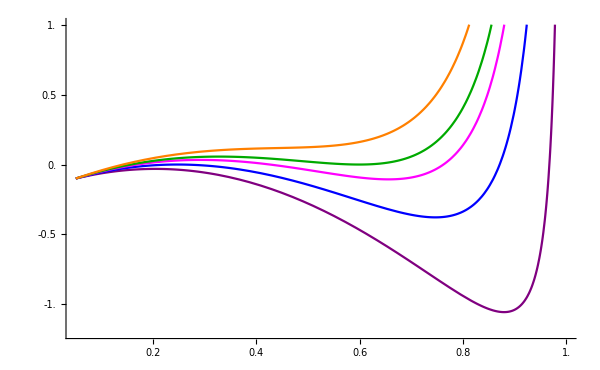

```mathematica
(*Plot f vs x to show the different cases admitted by the system*)
(*Where f = 0 is where Einstein points exist*)
fplot=Plot[{f[x,c[[1]],cr],f[x,c[[2]],cr],f[x,c[[4]],cr],f[x,c[[6]],cr],f[x,c[[7]],cr]},{x,0,1},PlotStyle->{Purple,Blue, Magenta,Darker[Green],Orange},AxesLabel->{MaTeX["x",FontSize->20],MaTeX["f(x)",FontSize->20]},Ticks->{{0.,0.2,0.4,0.6,0.8,1.},{-1.,-0.5,0.,0.5,1.}},PlotRange->{{ℛ,1},{-1.2,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

## Calculate the Einstein Points

### One Einstein Point: c1

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x value of the Einstein fixed point*)
xOneEinsteinPointc1=FindRoot[f[x,c[[1]],cr]==0,{x,0.9}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc1=x/.xOneEinsteinPointc1
```

0.967421

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc1=Z[xOneEinsteinPointc1,c[[1]]]
```

0.62664

```mathematica
(*Calculate the R value of the Einstein point*)
ROneEinsteinPointc1=R[xOneEinsteinPointc1,cr]
```

0.0769768

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[1]={xOneEinsteinPointc1,0,ZOneEinsteinPointc1,ROneEinsteinPointc1}
```

{0.967421,0,0.62664,0.0769768}

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x values of the Einstein fixed points*)
xTwoEinsteinPointsc2i=FindRoot[f[x,c[[2]],cr]==0,{x,0.1}];
xTwoEinsteinPointsc2ii=FindRoot[f[x,c[[2]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc2={x/.xTwoEinsteinPointsc2i,x/.xTwoEinsteinPointsc2ii}
```

{0.246738,0.871103}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc2=Z[xTwoEinsteinPointsc2,c[[2]]]
```

{0.0463988,0.584023}

```mathematica
(*Calculate the R values of the Einstein points*)
RTwoEinsteinPointsc2=R[xTwoEinsteinPointsc2,cr]
```

{0.000117007,0.0102506}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[2]={xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]],RTwoEinsteinPointsc2[[1]]}
EinsteinFP[3]={xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]],RTwoEinsteinPointsc2[[2]]}
```

{0.246738,0,0.0463988,0.000117007}

{0.871103,0,0.584023,0.0102506}

### Three Einstein Points: c3

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x values of the Einstein fixed points*)
xThreeEinsteinPointsc3i=FindRoot[f[x,c[[3]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc3ii=FindRoot[f[x,c[[3]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc3iii=FindRoot[f[x,c[[3]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc3={x/.xThreeEinsteinPointsc3i,x/.xThreeEinsteinPointsc3ii,x/.xThreeEinsteinPointsc3iii}
```

{0.190763,0.339647,0.8311}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc3=Z[xThreeEinsteinPointsc3,c[[3]]]
```

{0.0381488,0.0950237,0.556187}

```mathematica
(*Calculate the R values of the Einstein points*)
RThreeEinsteinPointsc3=R[xThreeEinsteinPointsc3,cr]
```

{0.0000661406,0.000242189,0.00656399}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[4]={xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]],RThreeEinsteinPointsc3[[1]]}
EinsteinFP[5]={xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]],RThreeEinsteinPointsc3[[2]]}
EinsteinFP[6]={xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]],RThreeEinsteinPointsc3[[3]]}
```

{0.190763,0,0.0381488,0.0000661406}

{0.339647,0,0.0950237,0.000242189}

{0.8311,0,0.556187,0.00656399}

### Three Einstein Points: c4

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x values of the Einstein fixed points*)
xThreeEinsteinPointsc4i=FindRoot[f[x,c[[4]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc4ii=FindRoot[f[x,c[[4]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc4iii=FindRoot[f[x,c[[4]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc4={x/.xThreeEinsteinPointsc4i,x/.xThreeEinsteinPointsc4ii,x/.xThreeEinsteinPointsc4iii}
```

{0.169206,0.426181,0.762176}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc4=Z[xThreeEinsteinPointsc4,c[[4]]]
```

{0.0395735,0.169387,0.502254}

```mathematica
(*Calculate the R values of the Einstein points*)
RThreeEinsteinPointsc4=R[xThreeEinsteinPointsc4,cr]
```

{0.0000504818,0.000425625,0.00357739}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[7]={xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]],RThreeEinsteinPointsc4[[1]]}
EinsteinFP[8]={xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]],RThreeEinsteinPointsc4[[2]]}
EinsteinFP[9]={xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]],RThreeEinsteinPointsc4[[3]]}
```

{0.169206,0,0.0395735,0.0000504818}

{0.426181,0,0.169387,0.000425625}

{0.762176,0,0.502254,0.00357739}

### Three Einstein Points: c5

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x values of the Einstein fixed points*)
xThreeEinsteinPointsc5i=FindRoot[f[x,c[[5]],cr]==0,{x,0.1}];
xThreeEinsteinPointsc5ii=FindRoot[f[x,c[[5]],cr]==0,{x,0.4}];
xThreeEinsteinPointsc5iii=FindRoot[f[x,c[[5]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc5={x/.xThreeEinsteinPointsc5i,x/.xThreeEinsteinPointsc5ii,x/.xThreeEinsteinPointsc5iii}
```

{0.162421,0.476643,0.716724}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc5=Z[xThreeEinsteinPointsc5,c[[5]]]
```

{0.0405517,0.220133,0.462864}

```mathematica
(*Calculate the R values of the Einstein points*)
RThreeEinsteinPointsc5=R[xThreeEinsteinPointsc5,cr]
```

{0.0000459683,0.000577826,0.00255394}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[10]={xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]],RThreeEinsteinPointsc5[[1]]}
EinsteinFP[11]={xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]],RThreeEinsteinPointsc5[[2]]}
EinsteinFP[12]={xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]],RThreeEinsteinPointsc5[[3]]}
```

{0.162421,0,0.0405517,0.0000459683}

{0.476643,0,0.220133,0.000577826}

{0.716724,0,0.462864,0.00255394}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x values of the Einstein fixed points*)
xTwoEinsteinPointsc6i=FindRoot[f[x,c[[6]],cr]==0,{x,0.1}];
xTwoEinsteinPointsc6ii=FindRoot[f[x,c[[6]],cr]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc6={x/.xTwoEinsteinPointsc6i,x/.xTwoEinsteinPointsc6ii}
```

{0.156331,0.598794}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc6=Z[xTwoEinsteinPointsc6,c[[6]]]
```

{0.0416437,0.348389}

```mathematica
(*Calculate the R values of the Einstein points*)
RTwoEinsteinPointsc6=R[xTwoEinsteinPointsc6,cr]
```

{0.0000420821,0.001194}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[13]={xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]],RTwoEinsteinPointsc6[[1]]}
EinsteinFP[14]={xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]],RTwoEinsteinPointsc6[[2]]}
```

{0.156331,0,0.0416437,0.0000420821}

{0.598794,0,0.348389,0.001194}

### One Einstein Point: c7

```mathematica
(*Numerically solve f(x) = 0 using FindRoot to find the x value of the Einstein fixed point*)
xOneEinsteinPointc7=FindRoot[f[x,c[[7]],cr]==0,{x,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc7=x/.xOneEinsteinPointc7
```

0.141399

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc7=Z[xOneEinsteinPointc7,c[[7]]]
```

0.0451691

```mathematica
(*Calculate the R value of the Einstein point*)
ROneEinsteinPointc7=R[xOneEinsteinPointc7,cr]
```

0.0000332021

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[15]={xOneEinsteinPointc7,0,ZOneEinsteinPointc7,ROneEinsteinPointc7}
```

{0.141399,0,0.0451691,0.0000332021}

```mathematica
(*Find the eigenvalues of the Einstein fixed points*)
```

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPs=Table[EinsteinFP[i],{i,1,15}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each Einstein fixed point*)
TableForm[Table[{EinsteinFPs[[i]]//MatrixForm,Simplify[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],R->EinsteinFPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],R->EinsteinFPs[[i,4]]}]]//MatrixForm},{i,1,15}],TableHeadings->{{"c1","c2","","c3","","","c4","","","c5","","","c6","","c7"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues
c1 | (0.967421
0
0.62664
0.0769768) | (0. | -0.0896672 | 0 | 0
0.775754 | 0. | -1.19562 | -0.391249
0 | -0.701887 | 0. | 0
0 | -0.284205 | 0 | 0.) | (0.938523
-0.938523
7.96254×10^-17
0.)
c2 | (0.246738
0
0.0463988
0.000117007) | (0. | -0.444587 | 0 | 0
0.0550718 | 0. | -0.18328 | -0.333411
0 | -0.132738 | 0. | 0
0 | -0.000467972 | 0 | 0.) | (-0.00005637
0.0000563699
1.33882×10^-10
0.)
 | (0.871103
0
0.584023
0.0102506) | (0. | -0.317514 | 0 | 0
0.679436 | 0. | -0.963185 | -0.340274
0 | -0.728821 | 0. | 0
0 | -0.040582 | 0 | 0.) | (0.707154
-0.707154
5.36455×10^-17
0.)
c3 | (0.190763
0
0.0381488
0.0000661406) | (0. | -0.341731 | 0 | 0
-0.000904133 | 0. | -0.180149 | -0.333377
0 | -0.11008 | 0. | 0
0 | -0.000264545 | 0 | 0.) | (-0.142225
0.142225
8.12045×10^-18
0.)
 | (0.339647
0
0.0950237
0.000242189) | (0. | -0.573807 | 0 | 0
0.14798 | 0. | -0.203505 | -0.333495
0 | -0.257982 | 0. | 0
0 | -0.00096852 | 0 | 0.) | (-6.01468×10^-17+0.179132 ⅈ
-6.01468×10^-17-0.179132 ⅈ
1.03856×10^-16+0. ⅈ
0.+0. ⅈ)
 | (0.8311
0
0.556187
0.00656399) | (0. | -0.395783 | 0 | 0
0.639433 | 0. | -0.846153 | -0.337753
0 | -0.740529 | 0. | 0
0 | -0.0260836 | 0 | 0.) | (0.618331
-0.618331
-6.67169×10^-17
0.)
c4 | (0.169206
0
0.0395735
0.0000504818) | (0. | -0.297108 | 0 | 0
-0.0224602 | 0. | -0.180684 | -0.333367
0 | -0.114022 | 0. | 0
0 | -0.000201917 | 0 | 0.) | (-0.165356
0.165356
-8.58732×10^-20
0.)
 | (0.426181
0
0.169387
0.000425625) | (0. | -0.647579 | 0 | 0
0.234514 | 0. | -0.241575 | -0.333617
0 | -0.422085 | 0. | 0
0 | -0.00170178 | 0 | 0.) | (5.5299×10^-17+0.222111 ⅈ
5.5299×10^-17-0.222111 ⅈ
-8.82802×10^-18+0. ⅈ
0.+0. ⅈ)
 | (0.762176
0
0.502254
0.00357739) | (0. | -0.508117 | 0 | 0
0.57051 | 0. | -0.672717 | -0.335731
0 | -0.749985 | 0. | 0
0 | -0.0142584 | 0 | 0.) | (0.468432
-0.468432
1.05611×10^-17
0.)
c5 | (0.162421
0
0.0405517
0.0000459683) | (0. | -0.282485 | 0 | 0
-0.0292454 | 0. | -0.181053 | -0.333364
0 | -0.116722 | 0. | 0
0 | -0.000183865 | 0 | 0.) | (-0.171626
0.171626
4.86975×10^-18
0.)
 | (0.476643
0
0.220133
0.000577826) | (0. | -0.66986 | 0 | 0
0.284976 | 0. | -0.274036 | -0.333719
0 | -0.515023 | 0. | 0
0 | -0.00230997 | 0 | 0.) | (1.25475×10^-16+0.221333 ⅈ
1.25475×10^-16-0.221333 ⅈ
4.86337×10^-17+0. ⅈ
0.+0. ⅈ)
 | (0.716724
0
0.462864
0.00255394) | (0. | -0.566601 | 0 | 0
0.525057 | 0. | -0.577671 | -0.335043
0 | -0.745863 | 0. | 0
0 | -0.0101897 | 0 | 0.) | (0.369837
-0.369837
-2.60869×10^-16
0.)
c6 | (0.156331
0
0.0416437
0.0000420821) | (0. | -0.269126 | 0 | 0
-0.0353352 | 0. | -0.181466 | -0.333361
0 | -0.119728 | 0. | 0
0 | -0.000168322 | 0 | 0.) | (0.176896
-0.176896
1.49757×10^-18
0.)
 | (0.598794
0
0.348389
0.001194) | (0. | -0.660538 | 0 | 0
0.407127 | 0. | -0.392529 | -0.334131
0 | -0.681043 | 0. | 0
0 | -0.00477029 | 0 | 0.) | (-0.000100137
0.000100136
1.23469×10^-9
0.)
c7 | (0.141399
0
0.0451691
0.0000332021) | (0. | -0.235425 | 0 | 0
-0.0502681 | 0. | -0.182808 | -0.333355
0 | -0.129387 | 0. | 0
0 | -0.000132804 | 0 | 0.) | (-0.188498
0.188498
9.76266×10^-18
0.)

## Analyse the Dark Energy EoS

```mathematica
(*Define the pressure for x*)
Px[x_,ℛ_]=-ℛ+ℛ*x-x^2;
```

```mathematica
(*Define the equations of state for x*)
wEffx[x_,ℛ_]=Px[x,ℛ]/x;
```

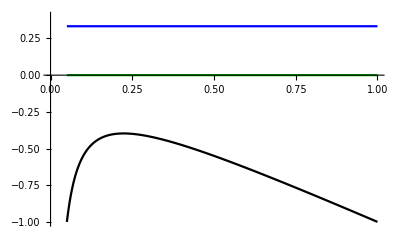

```mathematica
(*Plot the equations of state for dark energy, dark matter (w = 0) and radiation (w = 1/3)*)
(*The dashed line (w = -1/3) shows the boundary between the accelerating (w < -1/3) and decelerating (w > -1/3) regions*)
Plot[{wEffx[x,ℛ],0,1/3},{x,ℛ,1},PlotStyle->{Black, Darker[Green],Blue},GridLines->{{},{-1/3}},GridLinesStyle->Directive[Thick,Dashed],PlotRange->{-1,0.4}]
```

## Submanifolds

## Set-up

```mathematica
(*Define format of phase spaces*)
PhaseSpaceFormatxY={FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}};
```

```mathematica
PhaseSpaceFormatZY={FrameLabel->{MaTeX["Z",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[0,5]}],None}}};
```

```mathematica
PhaseSpaceFormatRY={FrameLabel->{MaTeX["R",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{0,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{R,MaTeX[R,"DisplayStyle"->False,FontSize->18]},{R,0.2Range[0,5]}],None}}};
```

```mathematica
(*Define compact radiation (R) and the scale factor (a) in terms of compact dark matter (Z)*)
rz[z_,crz_]=crz*z^(4/3);
RZ[Z_,crz_]=rz[Z/(1-Z),crz]/(1+rz[Z/(1-Z),crz]);

aZ[Z_,Z0_]=(((1-Z)/Z)(Z0/(1-Z0)))^(1/3);
```

```mathematica
(*Define compact dark matter (Z) and the scale factor (a) in terms of compact radiation (R)*)
zr[r_,crz_]=(r/crz)^(3/4);
ZR[R_,crz_]=zr[R/(1-R),crz]/(1+zr[R/(1-R),crz]);

aR[R_,R0_]=(((1-R)/R)(R0/(1-R0)))^(1/4);
```

```mathematica
(*Calculate the first integral of r(z), crz*)
(*Rearrange z for crz*)
crz=crz/.Simplify[Solve[z0==zr[r0,crz],crz][[1]]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

r0/z0^(4/3)

```mathematica
(*Define z0*)
z0=ρ0/ρc;
```

```mathematica
(*Calculate ρ0*)
ρ0=3*H0^2*Ωm
```

4272.53

```mathematica
(*Define r0*)
r0=ρr0/ρc
```

0.0000133291

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Value of crz*)
crz=crz
```

0.000828849

```mathematica
(*Clear z0 and r0*)
Clear[z0,r0]
```

```mathematica
(*Define f, the the RHS of y', for the submanifolds*)
fSubMan[x_,z_,r_]=-(1/6)*(z+2r-3*ℛ+x*(1+3*ℛ)-3*x^2);
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS) for the submanifolds in terms of Y^2/(1-Y^2)*)
ffsSubMan[x_,Z_,R_]=x/3+Z/(3*(1-Z))+R/(3*(1-R));
```

```mathematica
(*Rearrange the FFS for Y*)
(*Note that when plotting the FFS, +FFSSubMan and -FFSSubMan needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSSubMan[x_,Z_,R_]=Sqrt[ffsSubMan[x,Z,R]/(1+ffsSubMan[x,Z,R])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) for the submanifolds using a(x) in terms of Y^2/(1-Y^2)*)
cfsSubManx[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/a[x,x0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
(*Note that when plotting CFS, +CFSSubManx and -CFSSubManx needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFSSubManx[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManx[x,x0,Z,Z0,R,R0]/(1+cfsSubManx[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) for the submanifolds using a(Z) in terms of Y^2/(1-Y^2)*)
cfsSubManZ[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/aZ[Z,Z0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
(*Note that when plotting CFS, +CFSSubManZ and -CFSSubManZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFSSubManZ[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManZ[x,x0,Z,Z0,R,R0]/(1+cfsSubManZ[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) for the submanifolds using a(R) in terms of Y^2/(1-Y^2)*)
cfsSubManR[x_,x0_,Z_,Z0_,R_,R0_]= x/3+Z/(3*(1-Z))+R/(3*(1-R))-(1/aR[R,R0]^2)*(x0/3+Z0/(3*(1-Z0))+R0/(3*(1-R0)));
```

```mathematica
(*Rearrange above equation for Y*)
(*Note that when plotting CFS, +CFSSubManR and -CFSSubManR needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFSSubManR[x_,x0_,Z_,Z0_,R_,R0_]=Sqrt[cfsSubManR[x,x0,Z,Z0,R,R0]/(1+cfsSubManR[x,x0,Z,Z0,R,R0])];
```

```mathematica
(*Set up plot for x = ℛ and x = 1 separatrices*)
Sepx=ContourPlot[{x==ℛ,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
(*Set up the plots for the first integral cr surface and the first integral crz surface*)
Surfacecr=ParametricPlot3D[{x,Y,R[x,cr]},{x,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
Surfacecrz=ParametricPlot3D[{Z,Y,RZ[Z,crz]},{Z,0,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

### Potentials

```mathematica
(*Define the potential in terms of a, x, Z and R*)
USubMan[a_,x_,Z_,R_]=-a^2*(x/6+Z/(6*(1-Z))+R/(6*(1-R)));
```

```mathematica
(*Define the energy of the trajectories*)
EnergySubMan[x0_,Y0_,Z0_,R0_]=-(x0/6+Z0/(6*(1-Z0))+R0/(6*(1-R0))-Y0^2/(2*(1-Y0^2)));
```

```mathematica
(*Define separatrices for the plots of the potentials*)

xℛx1=ContourPlot[{x==ℛ,x==1},{x,0,1.01},{U,-1.5,1},ContourStyle->{{Black,Dashed,Thick}}];

Z0Z1=ContourPlot[{Z==0,Z==1},{Z,-0.01,1.01},{U,-1,1},ContourStyle->{{Black,Dashed,Thick}}];

R0R1=ContourPlot[{R==0,R==1},{R,-0.01,1.01},{U,-1,1},ContourStyle->{{Black,Dashed,Thick}}];
```

```mathematica
(*Define format for the plots of the potentials*)

FormatUx={ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["U",FontSize->18],270Degree]}};

FormatUZ={ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{MaTeX["Z",FontSize->18],Rotate[MaTeX["U",FontSize->18],270Degree]}};

FormatUR={ImageSize->{600,400},PlotRangePadding->{0.04,0},Frame->True,FrameLabel->{MaTeX["R",FontSize->18],Rotate[MaTeX["U",FontSize->18],270Degree]}};
```

## Qualitative ΛCDM Dynamics

```mathematica
(*These cases are analogous to ΛCDM*)
```

### x = ℛ, R = 0

#### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
(*The trajectories are plotted using the first integral (Friedmann equation) rather than the differential equations*)
trajxℛR0[Y0_,Z0_]:=Y^2/(1-Y^2)==ℛ/3+Z/(3*(1-Z))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
xℛR0traj[1]=ContourPlot[Evaluate[trajxℛR0[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[2]=ContourPlot[Evaluate[trajxℛR0[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[3]=ContourPlot[Evaluate[trajxℛR0[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[4]=ContourPlot[Evaluate[trajxℛR0[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[5]=ContourPlot[Evaluate[trajxℛR0[0.4,0.45]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[6]=ContourPlot[Evaluate[trajxℛR0[0.4,0.45]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[7]=ContourPlot[Evaluate[trajxℛR0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[8]=ContourPlot[Evaluate[trajxℛR0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[9]=ContourPlot[Evaluate[trajxℛR0[0.75,0.5]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛR0traj[10]=ContourPlot[Evaluate[trajxℛR0[0.75,0.5]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
TrajxℛR0=Table[xℛR0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
FFSxℛR0=Plot[{FFSSubMan[ℛ,Z,0],-FFSSubMan[ℛ,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSxℛR0=Plot[{{CFSSubManZ[ℛ,ℛ,Z,2*ℛ/(1+2*ℛ),0,0]},{-CFSSubManZ[ℛ,ℛ,Z,2*ℛ/(1+2*ℛ),0,0]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛR0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{2*ℛ/(1+2*ℛ),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

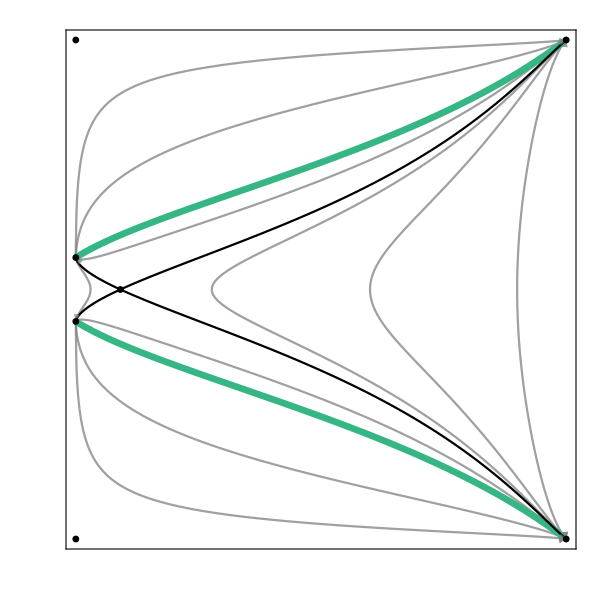

```mathematica
(*Show all components of the phase space*)
xℛR0SubMan=Show[TrajxℛR0,FFSxℛR0,CFSxℛR0,FPShowxℛR0,PhaseSpaceFormatZY]
```

#### Potential

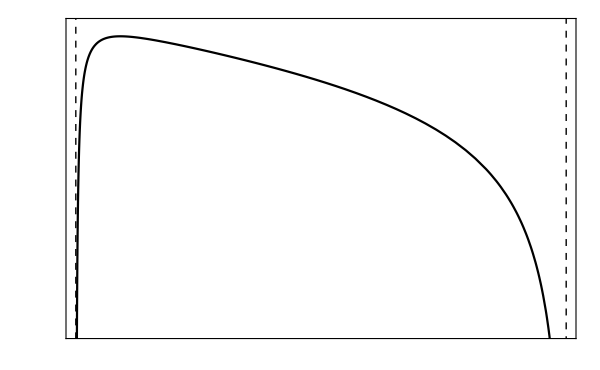

```mathematica
(*Plot the potential for this case*)
UxℛR0=Show[Plot[{USubMan[aZ[Z,0.2],ℛ,Z,0]},{Z,0,1},PlotStyle->{Black}],Z0Z1,FormatUZ,PlotRange->{-0.2,-0.04},FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False]},{U,0.02Range[-10,-2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False]},{Z,0.2Range[0,5]}],None}}]
```

#### Final Plot

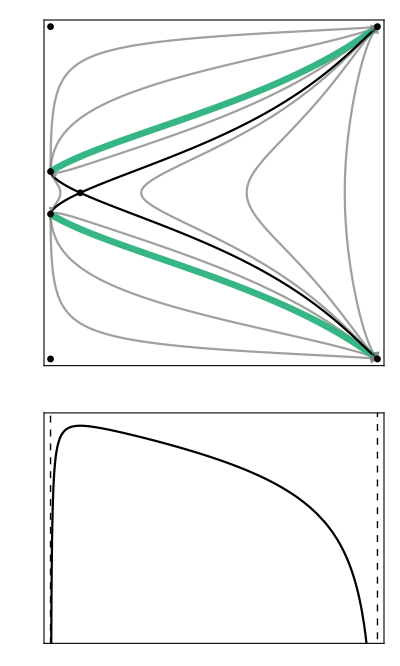

```mathematica
(*Plot the phase space and potential together*)
xℛR0=GraphicsColumn[{xℛR0SubMan,UxℛR0},Spacings->{0,0}]
```

### x = ℛ, Z = 0

#### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajxℛZ0[Y0_,R0_]:=Y^2/(1-Y^2)==ℛ/3+R/(3*(1-R))-(1/(aR[R,R0]^2))*(ℛ/3+R0/(3*(1-R0))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
xℛZ0traj[1]=ContourPlot[Evaluate[trajxℛZ0[0,0.01]],{R,0,0.1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[2]=ContourPlot[Evaluate[trajxℛZ0[0,0.01]],{R,0.1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[3]=ContourPlot[Evaluate[trajxℛZ0[0,0.6]],{R,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[4]=ContourPlot[Evaluate[trajxℛZ0[0,0.9]],{R,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[5]=ContourPlot[Evaluate[trajxℛZ0[0.4,0.45]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[6]=ContourPlot[Evaluate[trajxℛZ0[0.4,0.45]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[7]=ContourPlot[Evaluate[trajxℛZ0[0.9,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[8]=ContourPlot[Evaluate[trajxℛZ0[0.9,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[9]=ContourPlot[Evaluate[trajxℛZ0[0.75,0.5]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛZ0traj[10]=ContourPlot[Evaluate[trajxℛZ0[0.75,0.5]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
TrajxℛZ0=Table[xℛZ0traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
FFSxℛZ0=Plot[{FFSSubMan[ℛ,0,R],-FFSSubMan[ℛ,0,R]},{R,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSxℛZ0=Plot[{{CFSSubManR[ℛ,ℛ,0,0,R,ℛ/(1+ℛ)]},{-CFSSubManR[ℛ,ℛ,0,0,R,ℛ/(1+ℛ)]}},{R,0,1},PlotStyle->Black,PlotPoints->500];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛZ0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{ℛ/(1+ℛ),0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

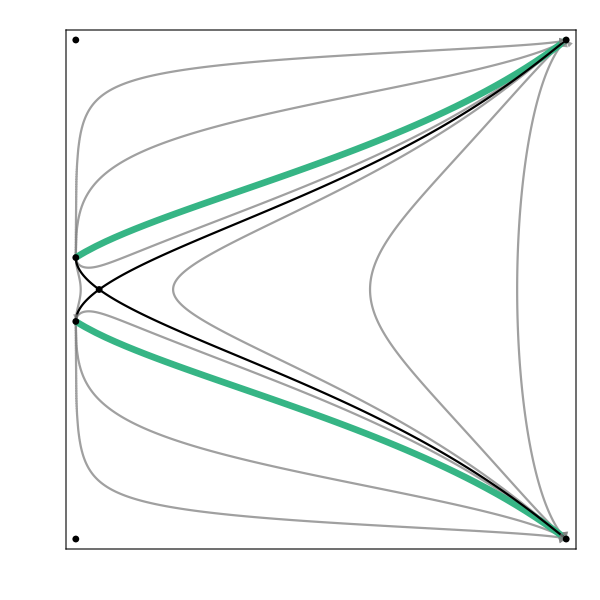

```mathematica
(*Show all components of the phase space*)
xℛZ0SubMan=Show[TrajxℛZ0,FFSxℛZ0,CFSxℛZ0,FPShowxℛZ0,PhaseSpaceFormatRY]
```

#### Potential

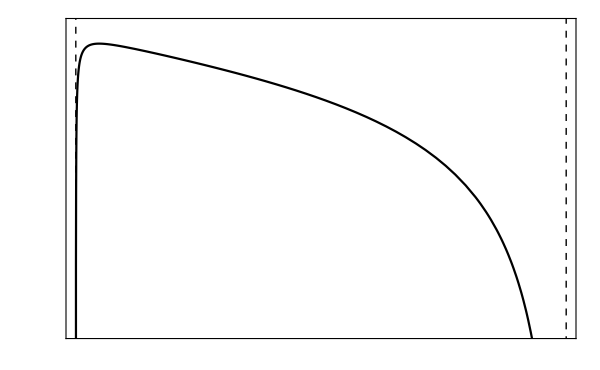

```mathematica
(*Plot the potential for this case*)
UxℛZ0=Show[Plot[{USubMan[aR[R,0.2],ℛ,0,R]},{R,0,1},PlotStyle->{Black}],R0R1,FormatUR,PlotRange->{-0.3,-0.02},FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->14]},{U,0.04Range[-7,0]}],None},{Table[{R,MaTeX[R,"DisplayStyle"->False,FontSize->14]},{R,0.2Range[0,5]}],None}}]
```

#### Final Plot

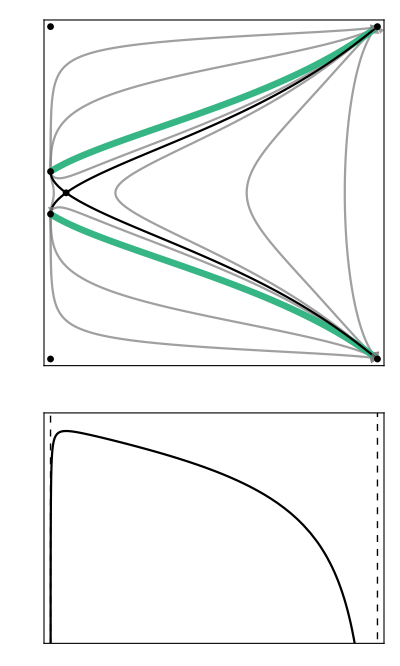

```mathematica
(*Plot the phase space and potential together*)
xℛZ0=GraphicsColumn[{xℛZ0SubMan,UxℛZ0},Spacings->{0,0}]
```

### x = ℛ

### Y = 0 fixed points

```mathematica
(*Solve f = 0 for Z to find the Einstein point*)
xℛY0=Solve[fSubMan[ℛ,Z/(1-Z),RZ[Z,crz]/(1-RZ[Z,crz])]==0,Z]
```

{{Z→0.0908456}}

```mathematica
(*Remove arrow and de-nest solution*)
xℛY0=Z/.xℛY0[[1]]
```

0.0908456

### Plot the Submanifold

```mathematica
(*Define the Friedmann equation for this case in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
traj3Dxℛ[Y0_,Z0_]=ℛ/3+Z/(3*(1-Z))+RZ[Z,crz]/(3*(1-RZ[Z,crz]))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))+RZ[Z0,crz]/(3*(1-RZ[Z0,crz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
(*Note that when plotting the trajectories, +traj3Dxℛ and -traj3Dxℛ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
traj3Dxℛ[Y0_,Z0_]=Sqrt[traj3Dxℛ[Y0,Z0]/(1+traj3Dxℛ[Y0,Z0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
xℛtraj3D[1]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.03],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[2]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.03],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[3]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.03],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->200,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[4]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.03],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->200,PlotRange->All,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[5]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.6],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[6]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.6],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[7]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.6],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[8]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.6],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[9]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.9],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[10]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.9],RZ[Z,crz]},{Z,0,xℛY0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
xℛtraj3D[11]=ParametricPlot3D[{Z,traj3Dxℛ[0,0.9],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[12]=ParametricPlot3D[{Z,-traj3Dxℛ[0,0.9],RZ[Z,crz]},{Z,xℛY0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[13]=ParametricPlot3D[{Z,traj3Dxℛ[0.4,0.45],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[14]=ParametricPlot3D[{Z,-traj3Dxℛ[0.4,0.45],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[15]=ParametricPlot3D[{Z,traj3Dxℛ[0.9,0.3],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[16]=ParametricPlot3D[{Z,-traj3Dxℛ[0.9,0.3],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[17]=ParametricPlot3D[{Z,traj3Dxℛ[0.75,0.5],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj3D[18]=ParametricPlot3D[{Z,-traj3Dxℛ[0.75,0.5],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Traj3Dxℛ=Table[xℛtraj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
FFS3Dxℛ=ParametricPlot3D[{{Z,FFSSubMan[ℛ,Z,RZ[Z,crz]],RZ[Z,crz]},{Z,-FFSSubMan[ℛ,Z,RZ[Z,crz]],RZ[Z,crz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFS3Dxℛ=ParametricPlot3D[{{Z,CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,crz],RZ[xℛY0,crz]],RZ[Z,crz]},{Z,-CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,crz],RZ[xℛY0,crz]],RZ[Z,crz]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dxℛ=ListPointPlot3D[{{0,1,0},{0,-1,0},{1,1,1},{1,-1,1},{0,Sqrt[ℛ/(3+ℛ)],0},{0,-Sqrt[ℛ/(3+ℛ)],0},{xℛY0,0,RZ[xℛY0,crz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Show all components of the phase space*)
xℛSubMan3D=Show[Traj3Dxℛ,FFS3Dxℛ,CFS3Dxℛ,FPShow3Dxℛ,Surfacecrz,AxesLabel->{"Z","Y","R"},PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

-Graphics3D-

### Plot the projection of the 3D submanifold

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajxℛ[Y0_,Z0_]:=Y^2/(1-Y^2)==ℛ/3+Z/(3*(1-Z))+RZ[Z,crz]/(3*(1-RZ[Z,crz]))-(1/aZ[Z,Z0]^2)*(ℛ/3+Z0/(3*(1-Z0))+RZ[Z0,crz]/(3*(1-RZ[Z0,crz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
xℛtraj[1]=ContourPlot[Evaluate[trajxℛ[0,0.03]],{Z,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[2]=ContourPlot[Evaluate[trajxℛ[0,0.03]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[3]=ContourPlot[Evaluate[trajxℛ[0,0.6]],{Z,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[4]=ContourPlot[Evaluate[trajxℛ[0,0.9]],{Z,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[5]=ContourPlot[Evaluate[trajxℛ[0.4,0.45]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[6]=ContourPlot[Evaluate[trajxℛ[0.4,0.45]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[7]=ContourPlot[Evaluate[trajxℛ[0.9,0.3]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[8]=ContourPlot[Evaluate[trajxℛ[0.9,0.3]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[9]=ContourPlot[Evaluate[trajxℛ[0.75,0.5]],{Z,0,1},{Y,0.1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
xℛtraj[10]=ContourPlot[Evaluate[trajxℛ[0.75,0.5]],{Z,0,1},{Y,-1,-0.1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajxℛ=Table[xℛtraj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
FFSxℛ=Plot[{FFSSubMan[ℛ,Z,RZ[Z,crz]],-FFSSubMan[ℛ,Z,RZ[Z,crz]]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSxℛ=Plot[{{CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,crz],RZ[xℛY0,crz]]},{-CFSSubManZ[ℛ,ℛ,Z,xℛY0,RZ[Z,crz],RZ[xℛY0,crz]]}},{Z,0,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowxℛ=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,Sqrt[ℛ/(3+ℛ)]},{0,-Sqrt[ℛ/(3+ℛ)]},{xℛY0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

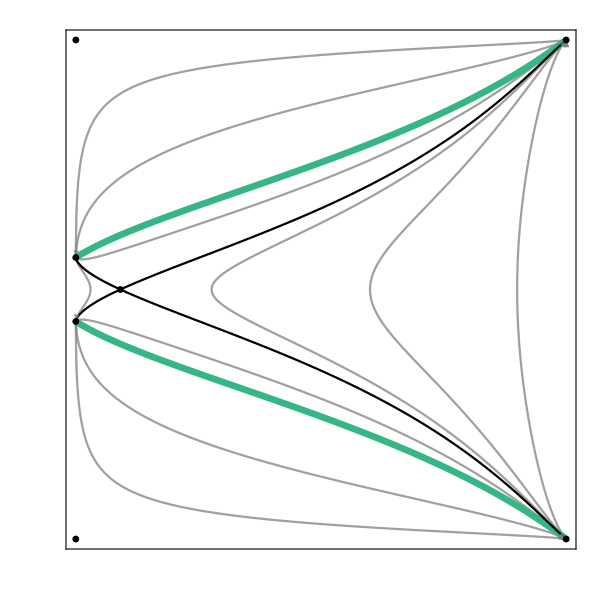

```mathematica
(*Show all components of the phase space*)
xℛSubMan=Show[Trajxℛ,FFSxℛ,CFSxℛ,FPShowxℛ,PhaseSpaceFormatZY]
```

#### Potential

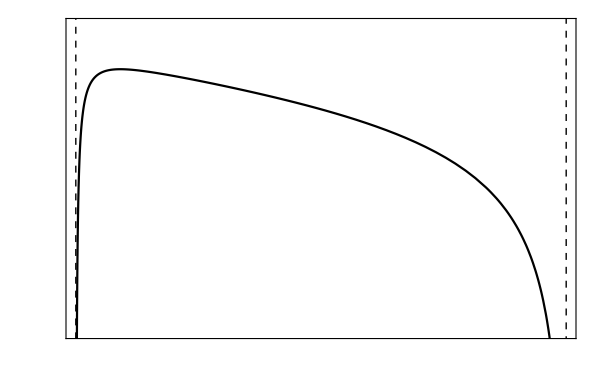

```mathematica
(*Plot the potential for this case*)
Uxℛ=Show[Plot[{USubMan[aZ[Z,0.2],ℛ,Z,RZ[Z,crz]]},{Z,0,1},PlotStyle->{Black}],Z0Z1,PlotRange->{-0.2,-0.02},FormatUZ,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False]},{U,0.02Range[-10,-2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False]},{Z,0.2Range[0,5]}],None}}]
```

#### Final Plot

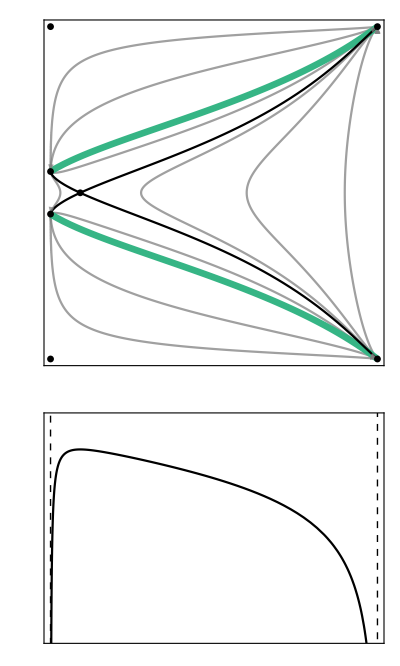

```mathematica
(*Plot the phase space and potential together*)
xℛProjection=GraphicsColumn[{xℛSubMan,Uxℛ},Spacings->{0,0}]
```

### x = 1, R = 0

#### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajx1R0[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
x1R0traj[1]=ContourPlot[Evaluate[trajx1R0[0,0.1]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[2]=ContourPlot[Evaluate[trajx1R0[0,0.1]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[3]=ContourPlot[Evaluate[trajx1R0[0,0.25]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[4]=ContourPlot[Evaluate[trajx1R0[0,0.25]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[5]=ContourPlot[Evaluate[trajx1R0[0,0.4]],{Z,0,2/3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[6]=ContourPlot[Evaluate[trajx1R0[0,0.4]],{Z,2/3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[7]=ContourPlot[Evaluate[trajx1R0[0.25,0.55]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[8]=ContourPlot[Evaluate[trajx1R0[0.25,0.55]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[9]=ContourPlot[Evaluate[trajx1R0[0.5,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[10]=ContourPlot[Evaluate[trajx1R0[0.5,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[11]=ContourPlot[Evaluate[trajx1R0[0.9,0.3]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1R0traj[12]=ContourPlot[Evaluate[trajx1R0[0.9,0.3]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajx1R0=Table[x1R0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSx1R0=Plot[{FFSSubMan[1,Z,0],-FFSSubMan[1,Z,0]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSx1R0=Plot[{CFSSubManZ[1,1,Z,2/3,0,0],-CFSSubManZ[1,1,Z,2/3,0,0]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1R0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {2/3,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

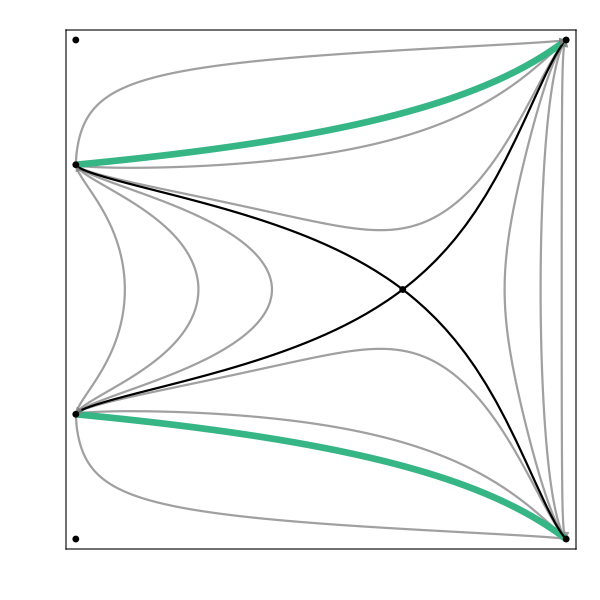

```mathematica
(*Show all components of the phase space*)
x1R0SubMan=Show[Trajx1R0,FFSx1R0,CFSx1R0,FPShowx1R0,PhaseSpaceFormatZY]
```

#### Potential

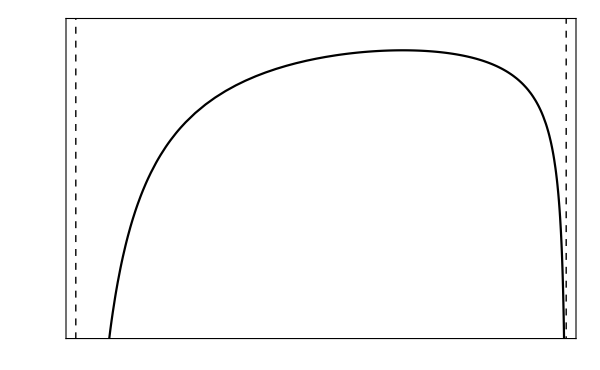

```mathematica
(*Plot the potential for this case*)
Ux1R0=Show[Plot[{USubMan[aZ[Z,0.2],1,Z,0]},{Z,0,1},PlotStyle->{Black}],Z0Z1,PlotRange->{-0.4,-0.1},FormatUZ,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False]},{U,0.05Range[-8,-2]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False]},{Z,0.2Range[0,5]}],None}}]
```

#### Final Plot

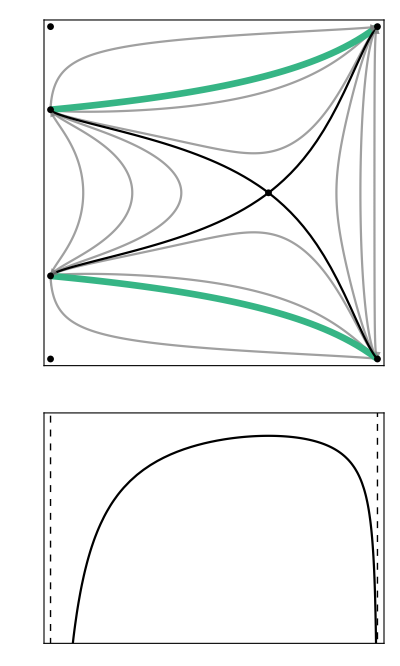

```mathematica
(*Plot the phase space and potential together*)
x1R0=GraphicsColumn[{x1R0SubMan,Ux1R0},Spacings->{0,0}]
```

### x = 1, Z = 0

#### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajx1Z0[Y0_,R0_]:=Y^2/(1-Y^2)==1/3+R/(3*(1-R))-(1/aR[R,R0]^2)*(1/3+R0/(3*(1-R0))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
x1Z0traj[1]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[2]=ContourPlot[Evaluate[trajx1Z0[0,0.1]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[3]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[4]=ContourPlot[Evaluate[trajx1Z0[0,0.25]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[5]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{R,0,1/2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[6]=ContourPlot[Evaluate[trajx1Z0[0,0.4]],{R,1/2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[7]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[8]=ContourPlot[Evaluate[trajx1Z0[0.25,0.55]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[9]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[10]=ContourPlot[Evaluate[trajx1Z0[0.5,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[11]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{R,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1Z0traj[12]=ContourPlot[Evaluate[trajx1Z0[0.9,0.3]],{R,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajx1Z0=Table[x1Z0traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSx1Z0=Plot[{FFSSubMan[1,0,R],-FFSSubMan[1,0,R]},{R,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSx1Z0=Plot[{CFSSubManR[1,1,0,0,R,1/2],-CFSSubManR[1,1,0,0,R,1/2]},{R,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShowx1Z0=ListPlot[{{0,1},{0,-1},{1,1},{1,-1},{0,1/2},{0,-1/2}, {1/2,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

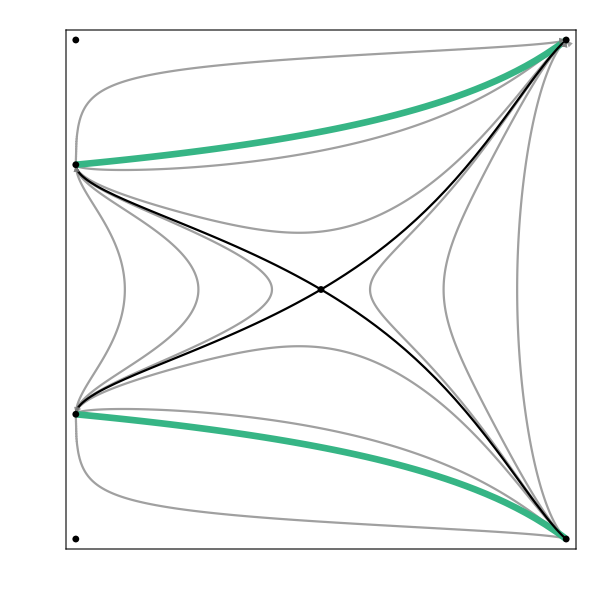

```mathematica
(*Show all components of the phase space*)
x1Z0SubMan=Show[Trajx1Z0,FFSx1Z0,CFSx1Z0,FPShowx1Z0,PhaseSpaceFormatRY]
```

#### Potential

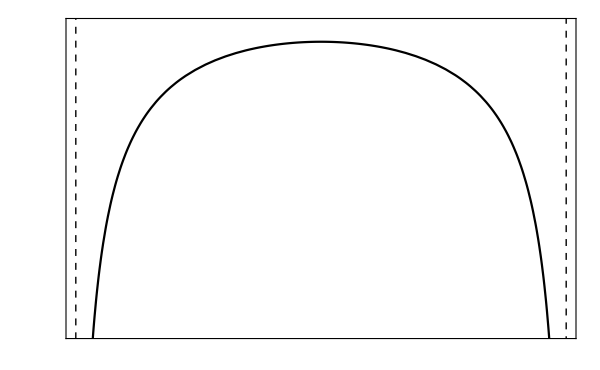

```mathematica
(*Plot the potential for this case*)
Ux1Z0=Show[Plot[{USubMan[aR[R,0.2],1,0,R]},{R,0,1},PlotStyle->{Black}],R0R1,FormatUR,PlotRange->{-0.45,-0.15},FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False]},{U,0.05Range[-8,-2]}],None},{Table[{R,MaTeX[R,"DisplayStyle"->False]},{R,0.2Range[0,5]}],None}}]
```

#### Final Plot

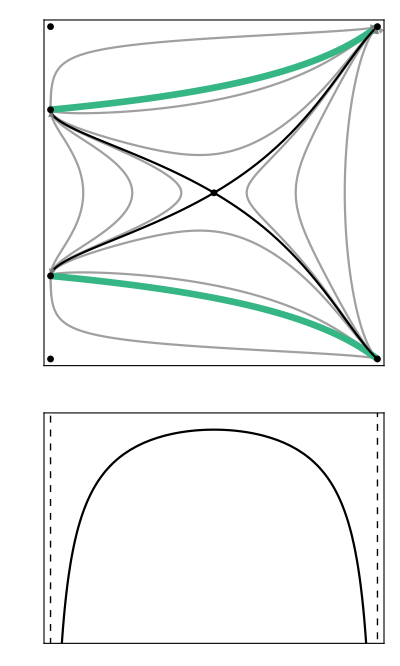

```mathematica
(*Plot the phase space and potential together*)
x1Z0=GraphicsColumn[{x1Z0SubMan,Ux1Z0},Spacings->{0,0}]
```

### x = 1

#### Y = 0 fixed points

```mathematica
(*Solve f = 0 for Z to find the Einstein point*)
x1Y0=Solve[fSubMan[1,Z/(1-Z),RZ[Z,crz]/(1-RZ[Z,crz])]==0,Z];
```

```mathematica
(*Remove arrow and de-nest solution*)
x1Y0=Z/.x1Y0[[1]]
```

0.666203

#### Plot the 3D Submanifold

```mathematica
(*Define the Friedmann equation for this case in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
traj3Dx1[Y0_,Z0_]=1/3+Z/(3*(1-Z))+RZ[Z,crz]/(3*(1-RZ[Z,crz]))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+RZ[Z0,cr]/(3*(1-RZ[Z0,cr]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange above equation for Y*)
(*Note that when plotting the trajectories, +traj3Dx1 and -traj3Dx1 needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
traj3Dx1[Y0_,Z0_]=Sqrt[traj3Dx1[Y0,Z0]/(1+traj3Dx1[Y0,Z0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
x1traj3D[1]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[2]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[3]=ParametricPlot3D[{Z,traj3Dx1[0,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[4]=ParametricPlot3D[{Z,-traj3Dx1[0,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->20000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[5]=ParametricPlot3D[{Z,traj3Dx1[0.38,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[6]=ParametricPlot3D[{Z,-traj3Dx1[0.38,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[7]=ParametricPlot3D[{Z,traj3Dx1[0.38,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[8]=ParametricPlot3D[{Z,-traj3Dx1[0.38,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->2000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[9]=ParametricPlot3D[{Z,traj3Dx1[0.41,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[10]=ParametricPlot3D[{Z,-traj3Dx1[0.41,0.1],RZ[Z,crz]},{Z,0,x1Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[11]=ParametricPlot3D[{Z,traj3Dx1[0.41,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[12]=ParametricPlot3D[{Z,-traj3Dx1[0.41,0.1],RZ[Z,crz]},{Z,x1Y0,1},PlotPoints->1000,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[13]=ParametricPlot3D[{Z,traj3Dx1[0.44,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[14]=ParametricPlot3D[{Z,-traj3Dx1[0.44,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[15]=ParametricPlot3D[{Z,traj3Dx1[0.48,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[16]=ParametricPlot3D[{Z,-traj3Dx1[0.48,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[17]=ParametricPlot3D[{Z,traj3Dx1[0.8,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0},1]]],Arrow[x]};
```

```mathematica
x1traj3D[18]=ParametricPlot3D[{Z,-traj3Dx1[0.8,0.1],RZ[Z,crz]},{Z,0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Traj3Dx1=Table[x1traj3D[i],{i,1,18}];
```

```mathematica
(*Plot the FFS*)
FFS3Dx1=ParametricPlot3D[{{Z,FFSSubMan[1,Z,RZ[Z,crz]],RZ[Z,crz]},{Z,-FFSSubMan[1,Z,RZ[Z,crz]],RZ[Z,crz]}},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFS3Dx1=ParametricPlot3D[{{Z,CFSSubManZ[1,1,Z,x1Y0,RZ[Z,crz],RZ[x1Y0,crz]],RZ[Z,crz]},{Z,-CFSSubManZ[1,1,Z,x1Y0,RZ[Z,crz],RZ[x1Y0,crz]],RZ[Z,crz]}},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points*)
FPShow3Dx1=ListPointPlot3D[{{0,1/2,0},{0,-1/2,0},{0,1,0},{0,-1,0},{1,1,1},{1,-1,1}, {x1Y0,0,RZ[x1Y0,crz]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot all components of the phase space*)
x1SubMan3D=Show[Traj3Dx1,FFS3Dx1,CFS3Dx1,FPShow3Dx1,Surfacecrz,AxesLabel->{MaTeX["Z",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["R",FontSize->20]},PlotRange->{{0,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

-Graphics3D-

### Plot the projection of the 3D submanifold

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)trajx1[Y0_,Z0_]:=Y^2/(1-Y^2)==1/3+Z/(3*(1-Z))+RZ[Z,crz]/(3*(1-RZ[Z,crz]))-(1/aZ[Z,Z0]^2)*(1/3+Z0/(3*(1-Z0))+RZ[Z0,crz]/(3*(1-RZ[Z0,crz]))-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
x1traj[1]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {Blue,Opacity[0.75]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[2]=ContourPlot[Evaluate[trajx1[0,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {Blue,Opacity[0.75]}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[3]=ContourPlot[Evaluate[trajx1[0.38,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[4]=ContourPlot[Evaluate[trajx1[0.38,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[5]=ContourPlot[Evaluate[trajx1[0.41,0.1]],{Z,0,x1Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[6]=ContourPlot[Evaluate[trajx1[0.41,0.1]],{Z,x1Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[7]=ContourPlot[Evaluate[trajx1[0.44,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[8]=ContourPlot[Evaluate[trajx1[0.44,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[9]=ContourPlot[Evaluate[trajx1[0.48,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[10]=ContourPlot[Evaluate[trajx1[0.48,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[11]=ContourPlot[Evaluate[trajx1[0.8,0.1]],{Z,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
x1traj[12]=ContourPlot[Evaluate[trajx1[0.8,0.1]],{Z,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajx1=Table[x1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSx1=Plot[{FFSSubMan[1,Z,RZ[Z,crz]/(1-RZ[Z,crz])],-FFSSubMan[1,Z,RZ[Z,crz]/(1-RZ[Z,crz])]},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSx1=Plot[{CFSSubManZ[1,1,Z,x1Y0,RZ[Z,crz],RZ[x1Y0,crz]],-CFSSubManZ[1,1,Z,x1Y0,RZ[Z,crz],RZ[x1Y0,crz]]},{Z,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the de Sitter line across Z = 0 and Z = 1*)
ZdS=ContourPlot[{Z==0,Z==1},{Z,-0.1,1.1},{Y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
(*Plot the fixed points*)
FPShowx1=ListPlot[{{0,1},{0,-1},{0,1/2},{0,-1/2},{1,1},{1,-1}, {x1Y0,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

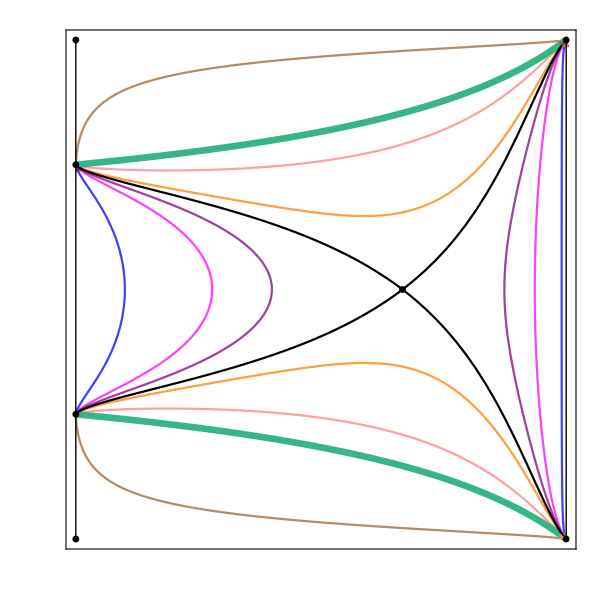

```mathematica
(*Show all components of the phase space together*)
x1SubMan=Show[Trajx1,FFSx1,CFSx1,FPShowx1,ZdS,PhaseSpaceFormatZY]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Ux1=Plot[{USubMan[aZ[Z,0.1],1,Z,RZ[Z,crz]]},{Z,0,1},PlotStyle->{Black},PlotRange->{{0,1},{-0.4,-0.05}}];
```

```mathematica
(*Plot the energies of the trajectories from above*)
```

```mathematica
x1Energy[1]=Plot[{EnergySubMan[1,0,0.1,RZ[0.1,crz]]},{Z,0,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
x1Energy[2]=Plot[{EnergySubMan[1,0,0.1,RZ[0.1,crz]]},{Z,0.99,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
x1Energy[3]=Plot[{EnergySubMan[1,0.38,0.1,RZ[0.1,crz]]},{Z,0,0.275},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
x1Energy[4]=Plot[{EnergySubMan[1,0.38,0.1,RZ[0.1,crz]]},{Z,0.935,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
x1Energy[5]=Plot[{EnergySubMan[1,0.41,0.1,RZ[0.1,crz]]},{Z,0,0.4},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
x1Energy[6]=Plot[{EnergySubMan[1,0.41,0.1,RZ[0.1,crz]]},{Z,0.875,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
x1Energy[7]=Plot[{EnergySubMan[1,0.44,0.1,RZ[0.1,crz]]},{Z,0,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
x1Energy[8]=Plot[{EnergySubMan[1,0.48,0.1,RZ[0.1,crz]]},{Z,0,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
x1Energy[9]=Plot[{EnergySubMan[1,0.8,0.1,RZ[0.1,crz]]},{Z,0,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
x1Energy[10]=Plot[{0},{Z,0,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
x1Energy[11]=Plot[{EnergySubMan[1,0,0.1,RZ[0.1,crz]]},{Z,0.1,0.99},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
x1Energy[12]=Plot[{EnergySubMan[1,0.38,0.1,RZ[0.1,crz]]},{Z,0.275,0.935},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
x1Energy[13]=Plot[{EnergySubMan[1,0.41,0.1,RZ[0.1,crz]]},{Z,0.4,0.875},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyx1=Table[x1Energy[i],{i,1,13}];
```

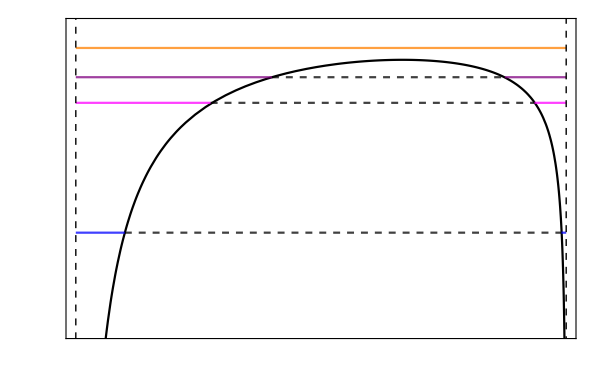

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialx1=Show[Ux1,Energyx1,Z0Z1,PlotRange->{{0,1},{-0.25,-0.05}},FormatUZ,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.05Range[-6,-1]}],None},{Table[{Z,MaTeX[Z,"DisplayStyle"->False,FontSize->18]},{Z,0.2Range[0,5]}],None}}]
```

#### Final Plot

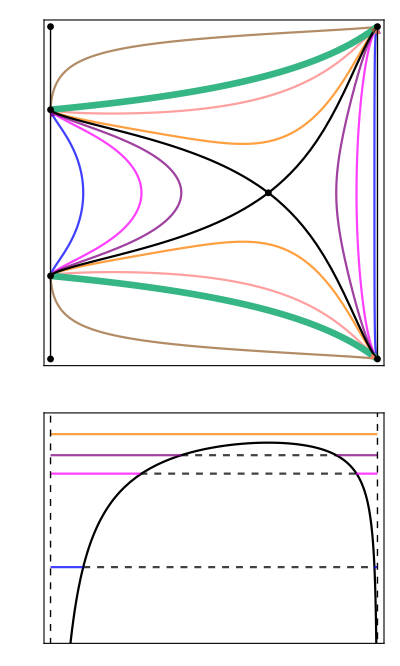

```mathematica
(*Plot the phase space and potential together*)
x1Projection=GraphicsColumn[{x1SubMan,Potentialx1},Spacings->{0,0}]
```

## Dynamic Dark Energy

### Z = 0, R = 0

```mathematica
(*There are three different cases for this sub-manifold*)
```

#### No Einstein Point Case

#### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajZ0R0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/a[x,x0]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
Z0R0traj[1]=ContourPlot[Evaluate[trajZ0R0[0,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[2]=ContourPlot[Evaluate[trajZ0R0[0.08,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[3]=ContourPlot[Evaluate[trajZ0R0[0.12,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[4]=ContourPlot[Evaluate[trajZ0R0[0.17,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[5]=ContourPlot[Evaluate[trajZ0R0[0.3,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[6]=ContourPlot[Evaluate[trajZ0R0[0.3,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[7]=ContourPlot[Evaluate[trajZ0R0[0.75,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj[8]=ContourPlot[Evaluate[trajZ0R0[0.75,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
TrajZ0R0=Table[Z0R0traj[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
FFSZ0R0=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R0=ListPlot[{{ℛ,1},{ℛ,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

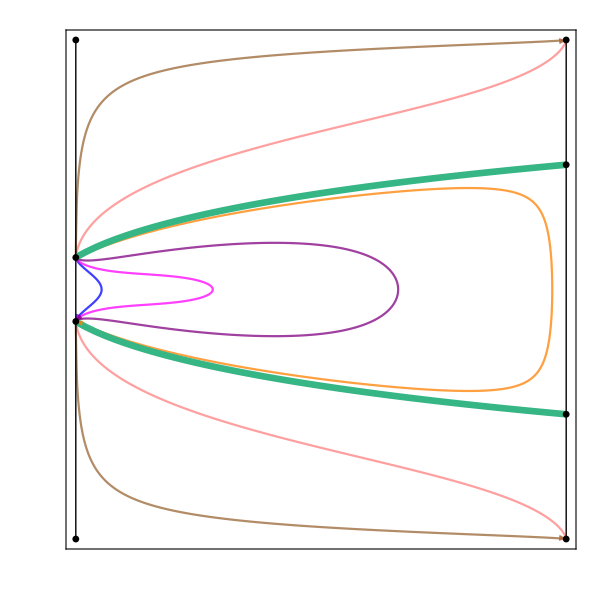

```mathematica
(*Show all components of the phase space*)
Z0R0SubMan=Show[TrajZ0R0,FFSZ0R0,FPShowZ0R0,Sepx,PhaseSpaceFormatxY]
```

#### Potential

```mathematica
(*Plot the potential for this case*)
UZ0R0=Plot[{USubMan[a[x,0.1],x,0,0]},{x,ℛ,1},PlotStyle->{Black},PlotRange->{{ℛ,1},{-0.023,0.001}}];
```

```mathematica
(*Plot the energies of the trajectories on the phase space*)
```

```mathematica
Z0R0Energy[1]=Plot[{EnergySubMan[0.1,0,0,0]},{x,ℛ,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[2]=Plot[{EnergySubMan[0.1,0.08,0,0]},{x,ℛ,0.315},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[3]=Plot[{EnergySubMan[0.1,0.12,0,0]},{x,ℛ,0.675},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[4]=Plot[{EnergySubMan[0.1,0.17,0,0]},{x,ℛ,0.975},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[5]=Plot[{EnergySubMan[0.1,0.3,0,0]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[6]=Plot[{EnergySubMan[0.1,0.75,0,0]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
Z0R0Energy[7]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
Z0R0Energy[8]=Plot[{EnergySubMan[0.1,0,0,0]},{x,0.1,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[9]=Plot[{EnergySubMan[0.1,0.08,0,0]},{x,0.315,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[10]=Plot[{EnergySubMan[0.1,0.12,0,0]},{x,0.675,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R0Energy[11]=Plot[{EnergySubMan[0.1,0.17,0,0]},{x,0.975,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
EnergyZ0R0=Table[Z0R0Energy[i],{i,1,11}];
```

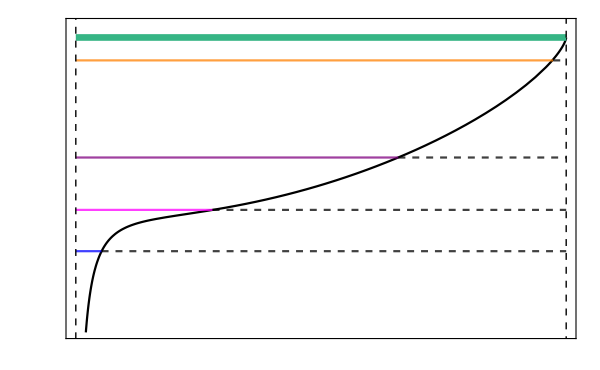

```mathematica
(*Show the potential and energy of the trajectories together*)
PotentialZ0R0=Show[UZ0R0,EnergyZ0R0,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.005Range[-5,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}]
```

#### Final Plot

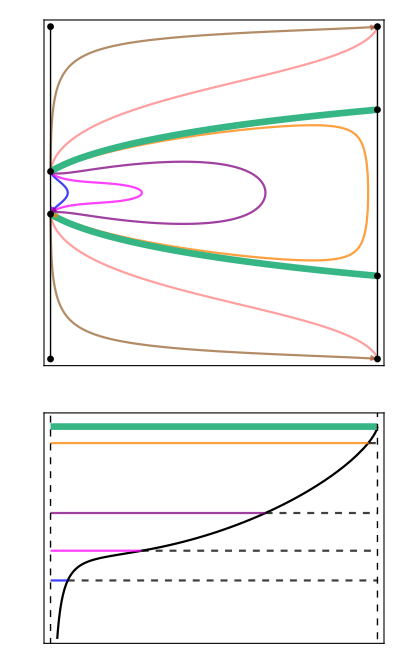

```mathematica
(*Plot the phase space and potential together*)
Z0R0=GraphicsColumn[{Z0R0SubMan,PotentialZ0R0},Spacings->{0,0}]
```

#### Limiting 1 Einstein Point Case

```mathematica
(*To illustrate the next two cases for this sub-manifold, we must change the value of ℛ*)
```

```mathematica
(*Redefine a(x) for these two cases*)
caZ0R0[x0_,ℛ2_]=(1-x0)/(x0-ℛ2);
aZ0R0[x_,x0_,ℛ2_]=(caZ0R0[x0,ℛ2]*((x-ℛ2)/(1-x)))^((-1)/(3*(1-ℛ2)));
```

```mathematica
(*Redefine the Closed Friedmann Separatrix (CFS) in terms of Y^2/(1-Y^2) for the submanifolds, using a(x) defined above*)
cfsSubManZ0R0[x_,x0_,ℛ2_]= x/3-(1/aZ0R0[x,x0,ℛ2]^2)*(x0/3);
```

```mathematica
(*Rearrange above equation for Y*)
CFSSubManZ0R0[x_,x0_,ℛ2_]=Sqrt[cfsSubManZ0R0[x,x0,ℛ2]/(1+cfsSubManZ0R0[x,x0,ℛ2])];
```

```mathematica
(*Define value of ℛ for the limiting case of this sub-manifold*)
ℛ1=5/3-2*Sqrt[6]/3;
```

#### Find the Y = 0 fixed points

```mathematica
(*Numerically solve for the Einstein fixed point*)
Z0R0Y0Lim=FindRoot[-(1/6)*(-3*ℛ1+x*(1+3*ℛ1)-3*x^2)==0,{x,0.2}];
```

```mathematica
(*Remove arrow and de-nest solution*)
Z0R0Y0Lim=x/.Z0R0Y0Lim[[1]]
```

0.183503

#### Plot the Submanifold

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajZ0R01E[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/aZ0R0[x,x0,ℛ1]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
Z0R0traj1E[1]=ContourPlot[Evaluate[trajZ0R01E[0,0.1]],{x,ℛ1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[2]=ContourPlot[Evaluate[trajZ0R01E[0.05,0.1]],{x,ℛ1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[3]=ContourPlot[Evaluate[trajZ0R01E[0.1,0.1]],{x,ℛ1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[4]=ContourPlot[Evaluate[trajZ0R01E[0.16,0.1]],{x,ℛ1,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[5]=ContourPlot[Evaluate[trajZ0R01E[0.3,0.1]],{x,ℛ1,1},{Y,0,1},PlotPoints->150,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[6]=ContourPlot[Evaluate[trajZ0R01E[0.3,0.1]],{x,ℛ1,1},{Y,-1,0},PlotPoints->150,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[7]=ContourPlot[Evaluate[trajZ0R01E[0.75,0.1]],{x,ℛ1,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj1E[8]=ContourPlot[Evaluate[trajZ0R01E[0.75,0.1]],{x,ℛ1,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
TrajZ0R01E=Table[Z0R0traj1E[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
FFSZ0R01E=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ1,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSZ0R01E=Plot[{{CFSSubManZ0R0[x,Z0R0Y0Lim,ℛ1]},{-CFSSubManZ0R0[x,Z0R0Y0Lim,ℛ1]}},{x,ℛ1,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R01E=ListPlot[{{ℛ1,1},{ℛ1,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ1,Sqrt[ℛ1/(3+ℛ1)]},{ℛ1,-Sqrt[ℛ1/(3+ℛ1)]},{Z0R0Y0Lim,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Set up plot for the x = ℛ and x = 1 separatrices*)
SepxZ0R01E=ContourPlot[{x==ℛ1,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
(*Plot the curve where acceleration is zero for this case*)
AccZ0R01E=ContourPlot[{-3*ℛ1+(1+3*ℛ1)*x-3*x^2==0},{x,ℛ1,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

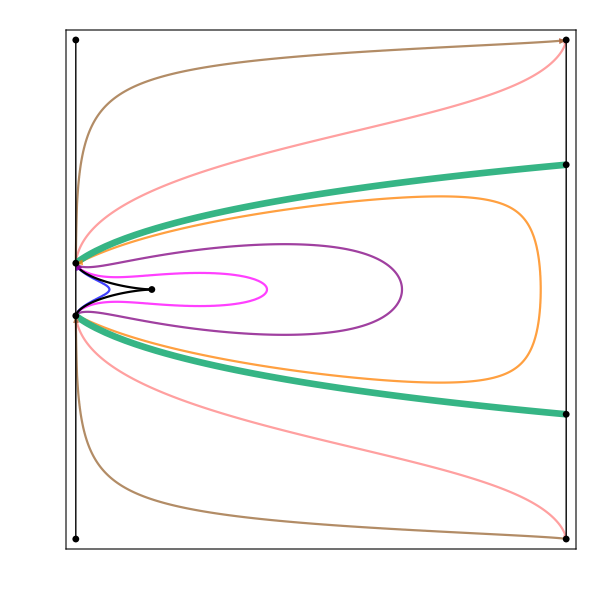

```mathematica
(*Show all components of the phase space*)
Z0R01ESubMan=Show[TrajZ0R01E,FFSZ0R01E,CFSZ0R01E,FPShowZ0R01E,SepxZ0R01E,{FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ1,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}}]
```

#### Potential

```mathematica
(*Plot the potential for this case*)
UZ0R01E=Plot[{USubMan[aZ0R0[x,0.1,ℛ1],x,0,0]},{x,ℛ1,1},PlotStyle->{Black},PlotRange->{{ℛ1,1},{-0.027,0}}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
Z0R01EEnergy[1]=Plot[{EnergySubMan[0.1,0,0,0]},{x,ℛ1,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[2]=Plot[{EnergySubMan[0.1,0.05,0,0]},{x,ℛ1,0.41},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[3]=Plot[{EnergySubMan[0.1,0.1,0,0]},{x,ℛ1,0.675},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[4]=Plot[{EnergySubMan[0.1,0.16,0,0]},{x,ℛ1,0.95},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[5]=Plot[{EnergySubMan[0.1,0.3,0,0]},{x,ℛ1,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[6]=Plot[{EnergySubMan[0.1,0.75,0,0]},{x,ℛ1,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
Z0R01EEnergy[7]=Plot[{0},{x,ℛ1,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
Z0R01EEnergy[8]=Plot[{EnergySubMan[0.1,0,0,0]},{x,0.1,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[9]=Plot[{EnergySubMan[0.1,0.05,0,0]},{x,0.41,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[10]=Plot[{EnergySubMan[0.1,0.1,0,0]},{x,0.675,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R01EEnergy[11]=Plot[{EnergySubMan[0.1,0.16,0,0]},{x,0.95,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
EnergyZ0R01E=Table[Z0R01EEnergy[i],{i,1,11}];
```

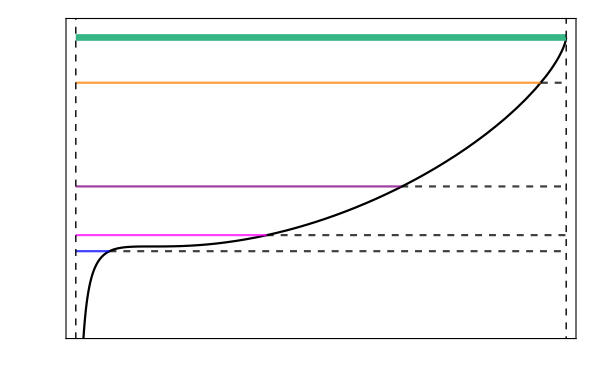

```mathematica
(*Show the potential and energy of the trajectories together*)
PotentialZ0R01E=Show[UZ0R01E,EnergyZ0R01E,ContourPlot[{x==ℛ1,x==1},{x,0,1.01},{U,-1,1},ContourStyle->{{Black,Dashed,Thick}}],FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.005Range[-6,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{ℛ1,1},{-0.023,0.001}}]
```

#### Final Plot

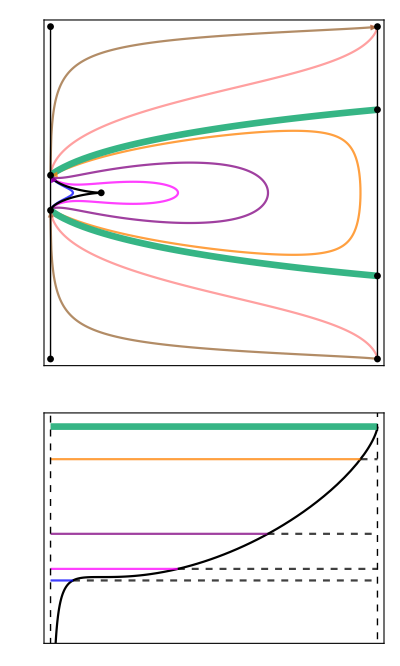

```mathematica
(*Plot the phase space and potential together*)
Z0R01E=GraphicsColumn[{Z0R01ESubMan,PotentialZ0R01E},Spacings->{0,0}]
```

#### 2 Einstein Point Case

```mathematica
(*Define value of ℛ for the case where two Einstein points exist*)
ℛ2=0.02;
```

#### Find the Y = 0 fixed points

```mathematica
(*Find the first Einstein fixed point numerically*)
Z0R0Y02E1=FindRoot[-(1/6)*(-3*ℛ2+x*(1+3*ℛ2)-3*x^2)==0,{x,0.1}];
```

```mathematica
(*Remove arrow and de-nest solution*)
Z0R0Y02E1=x/.Z0R0Y02E1[[1]]
```

0.0707841

```mathematica
(*Find the second Einstien fixed point numerically*)
Z0R0Y02E2=FindRoot[-(1/6)*(-3*ℛ2+x*(1+3*ℛ2)-3*x^2)==0,{x,0.2}];
```

```mathematica
(*Remove arrow and de-nest solution*)
Z0R0Y02E2=x/.Z0R0Y02E2[[1]]
```

0.282549

#### Plot the Submanifold

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajZ0R02E[Y0_,x0_]:=Y^2/(1-Y^2)==x/3-(1/aZ0R0[x,x0,ℛ2]^2)*(x0/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
Z0R0traj2E[1]=ContourPlot[Evaluate[trajZ0R02E[0,0.045]],{x,ℛ2,0.1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[2]=ContourPlot[Evaluate[trajZ0R02E[0,0.045]],{x,0.1,0.55},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[3]=ContourPlot[Evaluate[trajZ0R02E[0.07,0.045]],{x,ℛ2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[4]=ContourPlot[Evaluate[trajZ0R02E[0.11,0.045]],{x,ℛ2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[5]=ContourPlot[Evaluate[trajZ0R02E[0.2,0.045]],{x,ℛ2,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[6]=ContourPlot[Evaluate[trajZ0R02E[0.2,0.045]],{x,ℛ2,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[7]=ContourPlot[Evaluate[trajZ0R02E[0.55,0.045]],{x,ℛ2,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
Z0R0traj2E[8]=ContourPlot[Evaluate[trajZ0R02E[0.55,0.045]],{x,ℛ2,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
TrajZ0R02E=Table[Z0R0traj2E[i],{i,1,8}];
```

```mathematica
TrajZ0R02EPlot=Table[Z0R0traj2E[i],{i,5,8}];
```

```mathematica
(*Plot the FFS*)
FFSZ0R02E=Plot[{FFSSubMan[x,0,0],-FFSSubMan[x,0,0]},{x,ℛ2,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSZ0R02E=Plot[{{CFSSubManZ0R0[x,Z0R0Y02E1,ℛ2]},{-CFSSubManZ0R0[x,Z0R0Y02E1,ℛ2]},{CFSSubManZ0R0[x,Z0R0Y02E2,ℛ2]},{-CFSSubManZ0R0[x,Z0R0Y02E2,ℛ2]}},{x,ℛ2,1},PlotStyle->Black];
```

```mathematica
(*Plot the fixed points*)
FPShowZ0R02E=ListPlot[{{ℛ2,1},{ℛ2,-1},{1,1},{1,-1},{1,1/2},{1,-1/2},{ℛ2,Sqrt[ℛ2/(3+ℛ2)]},{ℛ2,-Sqrt[ℛ2/(3+ℛ2)]},{Z0R0Y02E1,0},{Z0R0Y02E2,0}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
FPShowZ0R02EPlot=ListPlot[{{1,1/2},{1,-1/2},{ℛ2,Sqrt[ℛ2/(3+ℛ2)]},{ℛ2,-Sqrt[ℛ2/(3+ℛ2)]}},PlotMarkers->{Automatic,Small},PlotStyle->{Black}];
```

```mathematica
(*Set up plot for the x = ℛ and x = 1 separatrices*)
SepxZ0R02E=ContourPlot[{x==ℛ2,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{{Black,Thick}},PlotRange->Full];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
AccZ0R02E=ContourPlot[{-3*ℛ2+(1+3*ℛ2)*x-3*x^2==0},{x,ℛ2,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

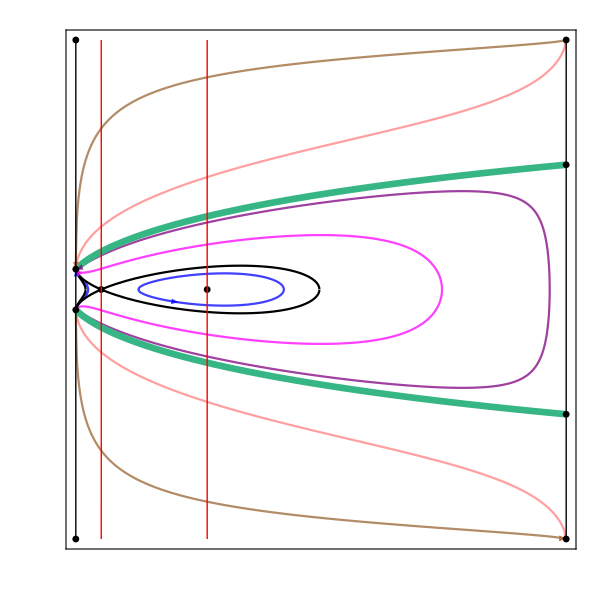

```mathematica
(*Show all components of the phase space*)
Z0R0SubMan2E=Show[TrajZ0R02E,FFSZ0R02E,CFSZ0R02E,FPShowZ0R02E,SepxZ0R02E,AccZ0R02E,{FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ2,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}}]
```

```mathematica
(*Plot the potential for this case*)
UZ0R02E=Plot[{USubMan[aZ0R0[x,0.045,ℛ2],x,0,0]},{x,ℛ2,1},PlotStyle->{Black},PlotRange->{{ℛ2,1},{-0.02,0}}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
Z0R02EEnergy[1]=Plot[{EnergySubMan[0.045,0,0,0]},{x,ℛ2,0.045},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[2]=Plot[{EnergySubMan[0.045,0,0,0]},{x,0.15,0.43},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[3]=Plot[{EnergySubMan[0.045,0.07,0,0]},{x,ℛ2,0.75},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[4]=Plot[{EnergySubMan[0.045,0.11,0,0]},{x,ℛ2,0.965},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[5]=Plot[{EnergySubMan[0.045,0.2,0,0]},{x,ℛ2,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[6]=Plot[{EnergySubMan[0.045,0.55,0,0]},{x,ℛ2,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
Z0R02EEnergy[7]=Plot[{0},{x,ℛ2,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
Z0R02EEnergy[8]=Plot[{EnergySubMan[0.045,0,0,0]},{x,0.045,0.15},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[9]=Plot[{EnergySubMan[0.045,0,0,0]},{x,0.43,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[10]=Plot[{EnergySubMan[0.045,0.07,0,0]},{x,0.75,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
Z0R02EEnergy[11]=Plot[{EnergySubMan[0.045,0.11,0,0]},{x,0.965,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
EnergyZ0R02E=Table[Z0R02EEnergy[i],{i,1,11}];
```

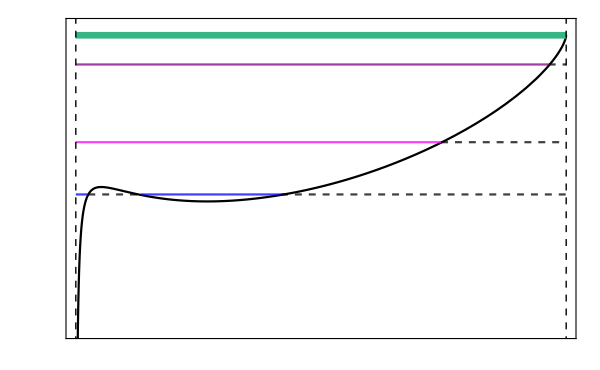

```mathematica
(*Show the potential and energy of the trajectories together*)
PotentialZ0R02E=Show[UZ0R02E,EnergyZ0R02E,ContourPlot[{x==ℛ2,x==1},{x,0,1.01},{U,-1,1},ContourStyle->{{Black,Dashed,Thick}}],FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.002Range[-7,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{ℛ2,1},{-0.014,0.0005}}]
```

#### Final Plot

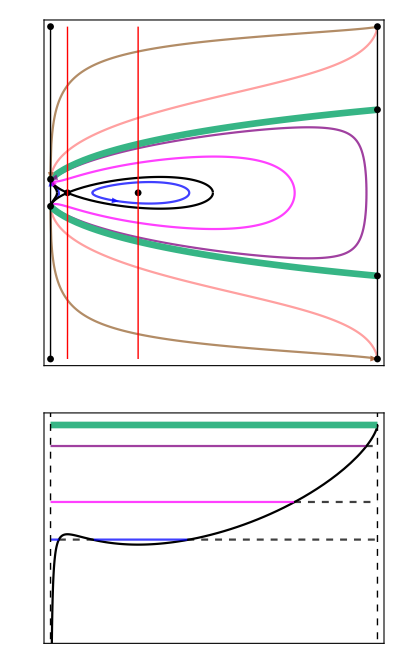

```mathematica
(*Plot the phase space and potential together*)
Z0R02E=GraphicsColumn[{Z0R0SubMan2E,PotentialZ0R02E},Spacings->{0,0}]
```

## k = 0 Submanifold

### Find the Y = 0 fixed points

```mathematica
(*Define z in the flat case using the Friedmann equation*)
zk0[Y_,x_]=3*Y^2/(1-Y^2)-x-r[x,cr];
```

```mathematica
(*Define the compactified variable Z in the flat case*)
Zk0[Y_,x_]=zk0[Y,x]/Sqrt[1+zk0[Y,x]^2];
```

```mathematica
(*Numerically solve f = 0 for the Einstein point*)
k0Y0=FindRoot[fSubMan[x,zk0[0,x],r[x,cr]]==0,{x,0.99}];
```

```mathematica
(*Remove arrow and de-nest solution*)
k0Y0=x/.k0Y0
```

0.997371

### Plot the 3D x-Y-R Submanifold

```mathematica
(*Defining ck, the first integral of z(x), for this case*)
ck[Y0_,x0_]=zk0[Y0,x0]*((1-x0)/(x0-ℛ))^(1/(1-ℛ));
```

```mathematica
(*Define the Friedmann equation for this case in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
traj3Dk0[Y0_,x0_]=x/3+z[x,ck[Y0,x0]]/3+r[x,cr]/3;
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +traj3Dk0 and -traj3Dk0 needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
traj3Dk0[Y0_,x0_]=Sqrt[traj3Dk0[Y0,x0]/(1+traj3Dk0[Y0,x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
k0traj3D[1]=ParametricPlot3D[{x,traj3Dk0[0,0.2],R[x,cr]},{x,ℛ,k0Y0},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[2]=ParametricPlot3D[{x,-traj3Dk0[0,0.2],R[x,cr]},{x,ℛ,k0Y0},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[3]=ParametricPlot3D[{x,traj3Dk0[0,0.2],R[x,cr]},{x,k0Y0,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[4]=ParametricPlot3D[{x,-traj3Dk0[0,0.2],R[x,cr]},{x,k0Y0,1},PlotPoints->100,AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[5]=ParametricPlot3D[{x,traj3Dk0[0,0.6],R[x,cr]},{x,ℛ,0.9},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[6]=ParametricPlot3D[{x,-traj3Dk0[0,0.6],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[7]=ParametricPlot3D[{x,traj3Dk0[0,0.95],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[8]=ParametricPlot3D[{x,-traj3Dk0[0,0.95],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[9]=ParametricPlot3D[{x,traj3Dk0[0.4,0.45],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[10]=ParametricPlot3D[{x,-traj3Dk0[0.4,0.45],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[11]=ParametricPlot3D[{x,traj3Dk0[0.8,0.3],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[12]=ParametricPlot3D[{x,-traj3Dk0[0.8,0.3],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[13]=ParametricPlot3D[{x,traj3Dk0[0.7,0.5],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[14]=ParametricPlot3D[{x,-traj3Dk0[0.7,0.5],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[15]=ParametricPlot3D[{x,traj3Dk0[0.48,0.8],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj3D[16]=ParametricPlot3D[{x,-traj3Dk0[0.48,0.8],R[x,cr]},{x,ℛ,1},PlotPoints->100,PlotStyle -> {{Gray, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Traj3Dk0=Table[k0traj3D[i],{i,1,16}];
```

```mathematica
(*Plot the separatrix for the fixed point where Y = 0*)
Sep3Dk0=ParametricPlot3D[{{x,traj3Dk0[0,k0Y0],R[x,cr]},{x,-traj3Dk0[0,k0Y0],R[x,cr]}},{x,ℛ,1},PlotStyle->{Black},PlotRange->{{0,1},{-1,1},{0,1}}];
```

```mathematica
(*Define the equation for the separatrix where z = 0*)
zZero[x_]=x/3+r[x,cr]/3;
```

```mathematica
(*Define the z = 0 separatrix in terms of the compactified variable Z*)
ZZero[x_]=Sqrt[zZero[x]/(1+zZero[x])]
```

√((0.000256723 ((-0.05+x)/(1-x))^1.40351+x/3)/(1+0.000256723 ((-0.05+x)/(1-x))^1.40351+x/3))

```mathematica
(*Plot the Z = 0 separatrix*)
(*Plot + and - ZZero as a Sqrt was taken and Mathematica defaults to the + only*)
SepZ0k0=ParametricPlot3D[{{x,ZZero[x],R[x,cr]},{x,-ZZero[x],R[x,cr]}},{x,ℛ,1},PlotStyle->{Darker[Green]},PlotPoints->100];
```

```mathematica
(*Plot the fixed points of the system*)
FPShow3Dk0=ListPointPlot3D[{{1,1,1},{1,-1,1},{ℛ,1,0},{ℛ,-1,0},{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{k0Y0,0,R[k0Y0,cr]}},PlotStyle->{Black},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Show all components of the plot*)
k0SubMan3D=Show[Traj3Dk0,Sep3Dk0,FPShow3Dk0,SepZ0k0,AxesLabel->{"x","Y","R"},ImageSize->{600,400},PlotRange->{{0,1},{-1,1},{0,1}}]
```

-Graphics3D-

### Plot the Projected x-Y Submanifold

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajk0[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,ck[Y0,x0]]/3+r[x,cr]/3;
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
k0traj[1]=ContourPlot[Evaluate[trajk0[0,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[2]=ContourPlot[Evaluate[trajk0[0.2,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[3]=ContourPlot[Evaluate[trajk0[0.24,0.2]],{x,ℛ,k0Y0},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[4]=ContourPlot[Evaluate[trajk0[0.24,0.2]],{x,k0Y0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[5]=ContourPlot[Evaluate[trajk0[0.2495,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[6]=ContourPlot[Evaluate[trajk0[0.2495,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[7]=ContourPlot[Evaluate[trajk0[0.32,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[8]=ContourPlot[Evaluate[trajk0[0.32,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[9]=ContourPlot[Evaluate[trajk0[0.8,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
k0traj[10]=ContourPlot[Evaluate[trajk0[0.8,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajk0=Table[k0traj[i],{i,1,10}];
```

```mathematica
(*Plot the separatrix where Z = 0*)
Sepk0=ContourPlot[{3*Y^2/(1-Y^2)-x-r[x,cr]==0},{x,ℛ,1},{Y,-1,1},ContourStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]},PlotPoints->100];
```

```mathematica
(*Plot the CFS*)
CFSk0=Plot[{traj3Dk0[0,k0Y0],-traj3Dk0[0,k0Y0]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points of the system*)
FPShowk0=ListPlot[{{1,1},{1,-1},{ℛ,1},{ℛ,-1},{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{k0Y0,0}},PlotStyle->{Black},PlotMarkers->{Automatic,Medium}, PlotStyle->{Black}];
```

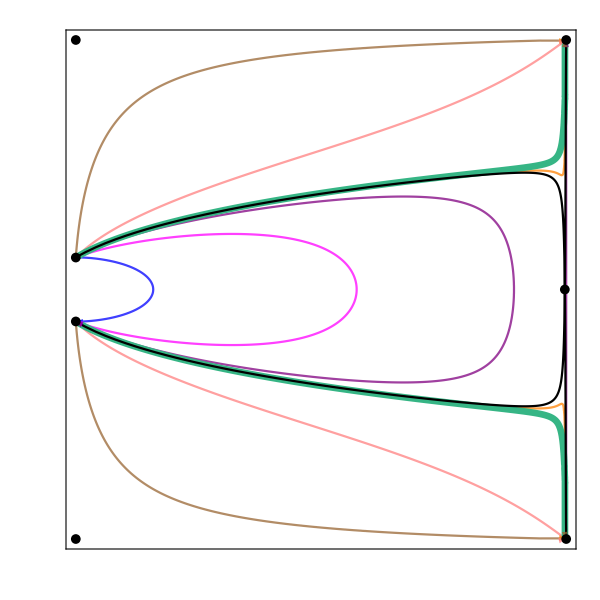

```mathematica
(*Show all components of the plot*)
k0SubMan=Show[trajk0,Sepk0,CFSk0,FPShowk0,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Plot the potentials for the trajectories in the phase space*)
Uk0Plot=Plot[{USubMan[a[x,0.2],x,z[x,ck[0,0.2]]/(1+z[x,ck[0,0.2]]),r[x,cr]/(1+r[x,cr])],USubMan[a[x,0.2],x,z[x,ck[0.2,0.2]]/(1+z[x,ck[0.2,0.2]]),r[x,cr]/(1+r[x,cr])],USubMan[a[x,0.2],x,z[x,ck[0.24,0.2]]/(1+z[x,ck[0.24,0.2]]),r[x,cr]/(1+r[x,cr])],USubMan[a[x,0.2],x,z[x,ck[0.2495,0.2]]/(1+z[x,ck[0.2495,0.2]]),r[x,cr]/(1+r[x,cr])],USubMan[a[x,0.2],x,z[x,ck[0.32,0.2]]/(1+z[x,ck[0.32,0.2]]),r[x,cr]/(1+r[x,cr])],USubMan[a[x,0.2],x,z[x,ck[0.8,0.2]]/(1+z[x,ck[0.8,0.2]]),r[x,cr]/(1+r[x,cr])]},{x,ℛ,1},PlotStyle->{Blue,Magenta,Purple,Orange,Pink,Brown},PlotRange->{{ℛ,1},{-0.15,0.2}}];
```

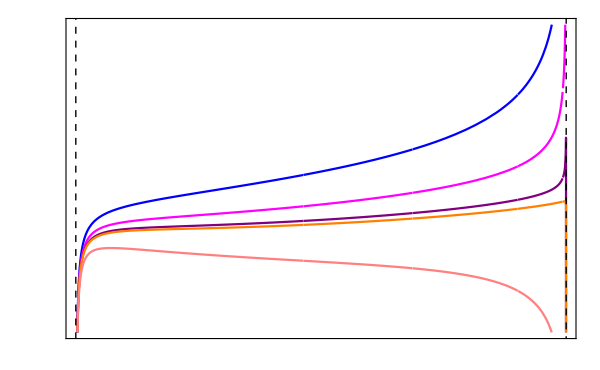

```mathematica
(*Show the plot of the potentials*)
Uk0=Show[Uk0Plot,xℛx1,FormatUx,PlotRange->{{ℛ,1},{-0.15,0.2}},FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.05Range[-4,4]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}]
```

#### Final Plot

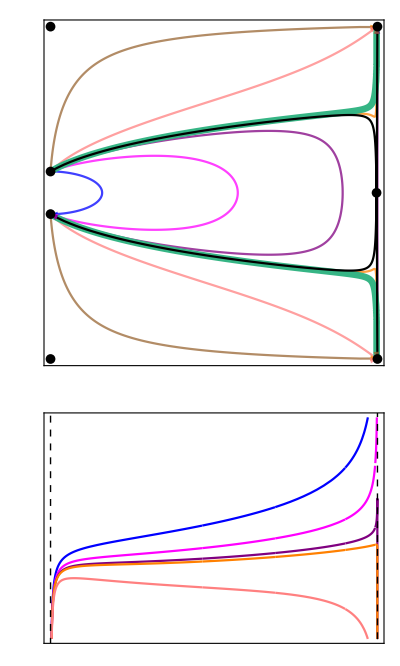

```mathematica
(*Plot the phase space and potential together*)
k0=GraphicsColumn[{k0SubMan,Uk0},Spacings->{0,0}]
```

## Full System of Equations: 2-D x-Y Phase Spaces and Potentials

## Set-up

### Phase Spaces

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS) in terms of Y^2/(1-Y^2)*)
ffs=(1/3)*(x+z[x,c]+r[x,cr]);
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the FFS, +FFS and -FFS needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Set up the plot for the x = ℛ and x = 1 separatrices*)
Sep=ContourPlot[{x==ℛ,x==1},{x,0,1.01},{Y,-1,1},ContourStyle->{{Black,Thick}}];
```

```mathematica
(*Define the equations for the Closed Friedmann Separatrix (CFS) in terms of Y^2/(1-Y^2)*)
cfs[x0_]= x/3+z[x,c]/3+r[x,cr]/3-(x0/3+z[x0,c]/3+r[x0,cr]/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the CFS, +CFS and -CFS needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFS[x0_]=Sqrt[cfs[x0]/(1+cfs[x0])];
```

```mathematica
(*Plot of the common fixed points of the phase spaces for the full system*)
FPShow=ListPlot[{{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{ℛ,1},{ℛ,-1},{1,1},{1,-1}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation for the system*)
Accn=z[x,c]+2*r[x,cr]-3*ℛ+(1+3*ℛ)*x-3*x^2;
```

### Potentials

```mathematica
(*Define the potential term Ua^2/2*)
U[x_,x0_]=-a[x,x0]^2*(x/6+z[x,c]/6+r[x,cr]/6);
```

```mathematica
(*Find the first derivative of U with respect to x*)
dUdx=Simplify[D[U[x,x0],x]];
```

```mathematica
(*Find the second derivative of U with respect to x*)
d2Udx2[x_,x0_]=Simplify[D[U[x,x0],{x,2}]];
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,Y0_]=-(x0/6+z[x0,c]/6+r[x0,cr]/6-Y0^2/(2*(1-Y0^2)));
```

## One Einstein Point: c1

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
(*The trajectories are plotted using the first integral (Friedmann equation) rather than the differential equations*)
trajc1[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[1]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[1]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,ℛ,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,ℛ,0.9},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSc1=Plot[{FFS[[1]],-FFS[[1]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSc1=Plot[{CFS[xOneEinsteinPointc1][[1]],-CFS[xOneEinsteinPointc1][[1]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed point for this case*)
Einsteinc1=ListPlot[{{xOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between accelerating and decelerating regions for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

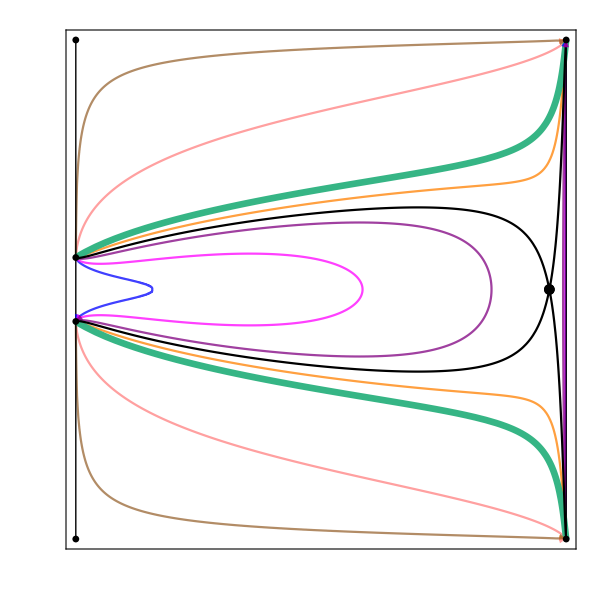

```mathematica
(*Show all components of the phase space*)
PhaseSpacec1=Show[Trajc1,FFSc1,CFSc1,Einsteinc1,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute the Einstein points into the second derivative of U(x) to find whether the point is a maximum or a minimum of the potential*)
(*A positive/negative/zero value means it's a minimum/maximum/cusp*)
d2Udx2[xOneEinsteinPointc1,0.2][[1]]
```

-3.25213

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[x,0.2][[1]]},{x,ℛ,1},PlotStyle->{{Black}}];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{x,ℛ,0.2},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0.12][[1]]},{x,ℛ,0.6},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.18][[1]]},{x,ℛ,0.85},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.225][[1]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0.5][[1]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.9][[1]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c1Energy[7]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[8]=Plot[{Energy[0.2,0][[1]]},{x,0.2,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[9]=Plot[{Energy[0.2,0.12][[1]]},{x,0.6,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[10]=Plot[{Energy[0.2,0.18][[1]]},{x,0.85,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,10}];
```

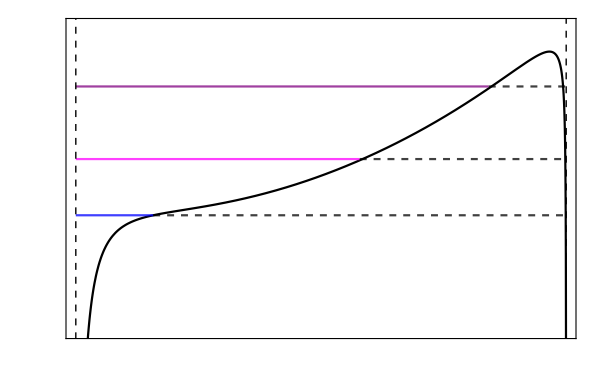

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.01Range[-5,-1]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.05,-0.01}}]
```

### Final Plot

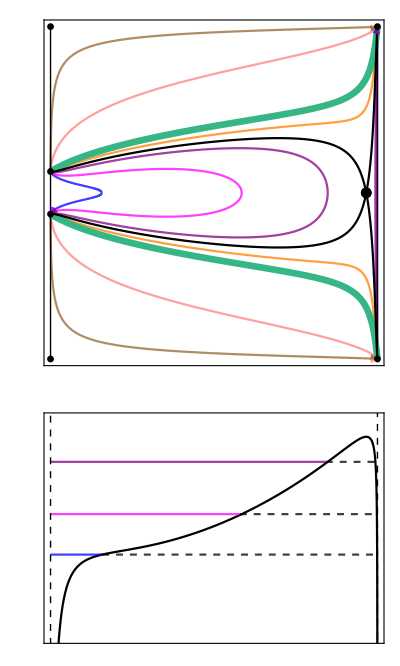

```mathematica
(*Plot the phase space and potential together*)
xYc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,0}]
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc2[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[2]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[2]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,ℛ,0.6},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,ℛ,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.13,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[9]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[10]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[11]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
FFSc2=Plot[{FFS[[2]],-FFS[[2]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc2=Plot[{CFS[xTwoEinsteinPointsc2][[2]],-CFS[xTwoEinsteinPointsc2][[2]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{xTwoEinsteinPointsc2[[1]],0},{xTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

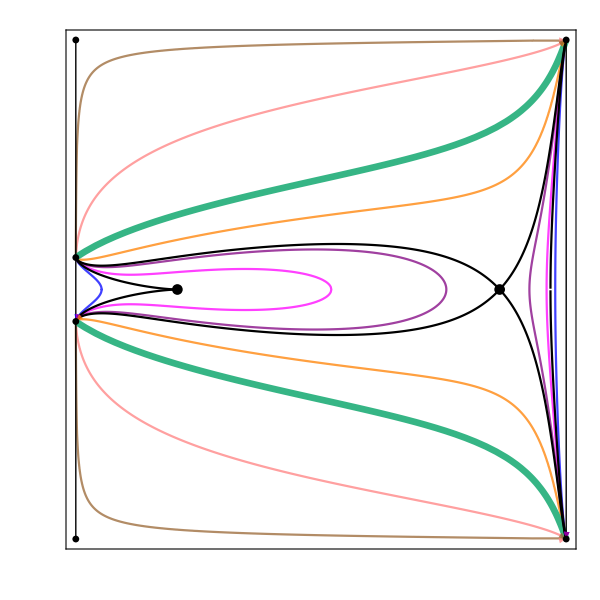

```mathematica
(*Show all components of the phase space*)
PhaseSpacec2=Show[Trajc2, FFSc2,CFSc2,Einsteinc2,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute the Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum of the potential*)
d2Udx2[xTwoEinsteinPointsc2[[1]],0.1][[2]]
```

-5.42565×10^-9

```mathematica
d2Udx2[xTwoEinsteinPointsc2[[2]],0.1][[2]]
```

-0.177947

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[x,0.1][[2]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{x,ℛ,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0][[2]]},{x,0.98,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.07][[2]]},{x,ℛ,0.54},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.07][[2]]},{x,0.965,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0.09][[2]]},{x,ℛ,0.765},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.09][[2]]},{x,0.93,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.13][[2]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.4][[2]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energy[9]=Plot[{Energy[0.1,0.9][[2]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c2Energy[10]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[11]=Plot[{Energy[0.1,0][[2]]},{x,0.1,0.98},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[12]=Plot[{Energy[0.1,0.07][[2]]},{x,0.54,0.965},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[13]=Plot[{Energy[0.1,0.09][[2]]},{x,0.765,0.93},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,13}];
```

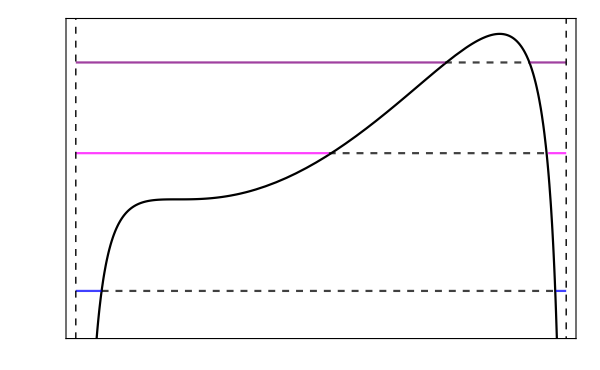

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.001Range[-19,-14]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.019,-0.0135}}]
```

### Final Plot

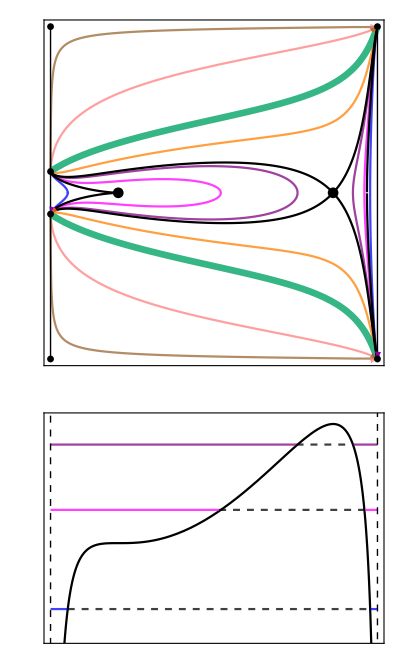

```mathematica
(*Plot the phase space and potential together*)
xYc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,0}]
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc3[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[3]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.2,0.5},{Y,-1,1},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,ℛ,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,ℛ,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[10]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[11]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[12]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[13]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
FFSc3=Plot[{FFS[[3]],-FFS[[3]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc3=Plot[{CFS[xThreeEinsteinPointsc3][[3]],-CFS[xThreeEinsteinPointsc3][[3]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->600];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{xThreeEinsteinPointsc3[[1]],0},{xThreeEinsteinPointsc3[[2]],0},{xThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick},PlotPoints->200];
```

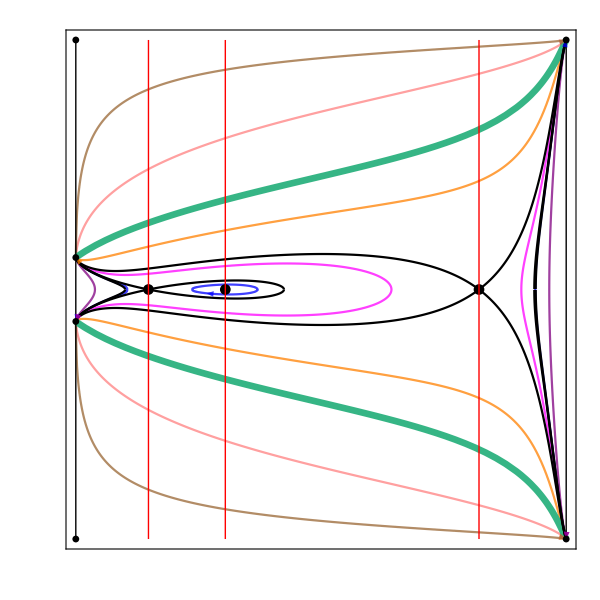

```mathematica
(*Show all components of the phase space*)
PhaseSpacec3=Show[Trajc3, FFSc3,CFSc3,Einsteinc3,Accnc3,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum of the potential*)
d2Udx2[xThreeEinsteinPointsc3[[1]],0.155][[3]]
```

-0.136796

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[2]],0.155][[3]]
```

0.0402181

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[3]],0.155][[3]]
```

-0.192864

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[x,0.08][[3]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->{-0.016,-0.0105}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0.071][[3]]},{x,ℛ,0.15},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.071][[3]]},{x,0.275,0.4},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.071][[3]]},{x,0.94,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.08][[3]]},{x,ℛ,0.655},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.08][[3]]},{x,0.92,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0.04][[3]]},{x,ℛ,0.09},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.04][[3]]},{x,0.97,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.12][[3]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.3][[3]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.6][[3]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c3Energy[11]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[12]=Plot[{Energy[0.08,0.071][[3]]},{x,0.15,0.275},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[13]=Plot[{Energy[0.08,0.071][[3]]},{x,0.4,0.94},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[14]=Plot[{Energy[0.08,0.08][[3]]},{x,0.655,0.92},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[15]=Plot[{Energy[0.08,0.04][[3]]},{x,0.09,0.97},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,15}];
```

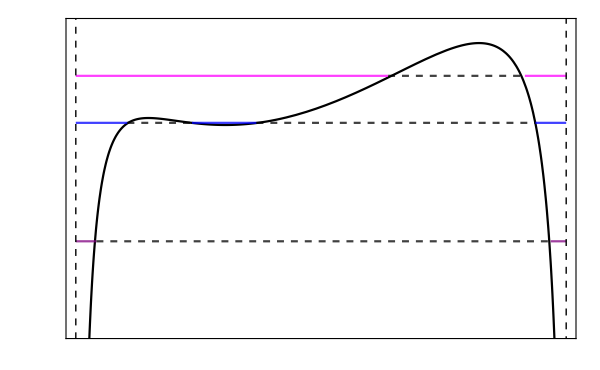

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.001Range[-15,-10]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.015,-0.0105}}]
```

### Final Plot

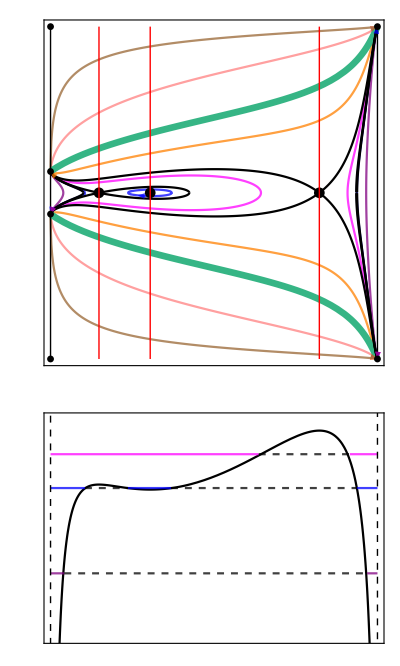

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,0}]
```

## Three Einstein Points: c4

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc4[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[4]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[4]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c4traj[1]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[2]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[3]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[4]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,ℛ,0.3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[5]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[6]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[7]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[8]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[9]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[10]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[11]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc4=Table[c4traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
FFSc4=Plot[{FFS[[4]],-FFS[[4]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc4=Plot[{CFS[xThreeEinsteinPointsc4][[4]],-CFS[xThreeEinsteinPointsc4][[4]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4=ListPlot[{{xThreeEinsteinPointsc4[[1]],0},{xThreeEinsteinPointsc4[[2]],0},{xThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc4=ContourPlot[Accn[[4]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

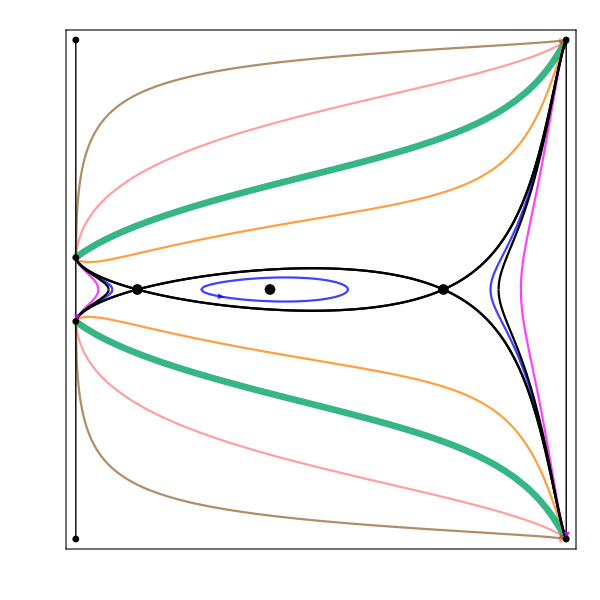

```mathematica
(*Show all components of the phase space*)
PhaseSpacec4=Show[Trajc4, FFSc4,CFSc4,Einsteinc4,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum of the potential*)
d2Udx2[xThreeEinsteinPointsc4[[1]],0.08][[4]]
```

-0.109509

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[2]],0.08][[4]]
```

0.0143208

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[3]],0.08][[4]]
```

-0.0356306

```mathematica
(*Plot the potential for this case*)
Uc4=Plot[{U[x,0.08][[4]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c4Energy[1]=Plot[{Energy[0.08,0.065][[4]]},{x,ℛ,0.12},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[2]=Plot[{Energy[0.08,0.065][[4]]},{x,0.3,0.57},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[3]=Plot[{Energy[0.08,0.065][[4]]},{x,0.855,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[4]=Plot[{Energy[0.08,0.05][[4]]},{x,ℛ,0.095},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[5]=Plot[{Energy[0.08,0.05][[4]]},{x,0.91,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[6]=Plot[{Energy[0.08,0.11][[4]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energy[7]=Plot[{Energy[0.08,0.3][[4]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energy[8]=Plot[{Energy[0.08,0.6][[4]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c4Energy[9]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energy[10]=Plot[{Energy[0.08,0.065][[4]]},{x,0.12,0.3},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[11]=Plot[{Energy[0.08,0.065][[4]]},{x,0.57,0.855},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[12]=Plot[{Energy[0.08,0.05][[4]]},{x,0.095,0.91},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc4=Table[c4Energy[i],{i,1,12}];
```

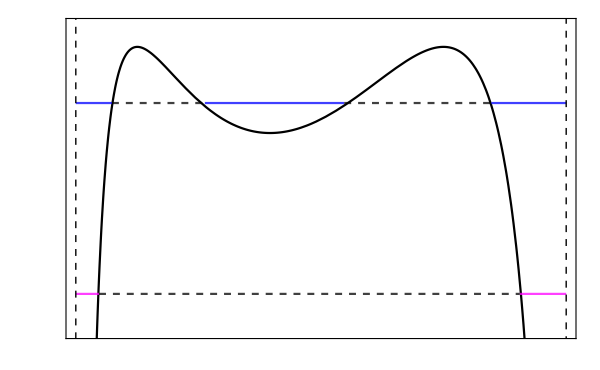

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4=Show[Uc4,Energyc4,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.0002Range[-68,-62]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.0137,-0.0123}}]
```

### Final Plot

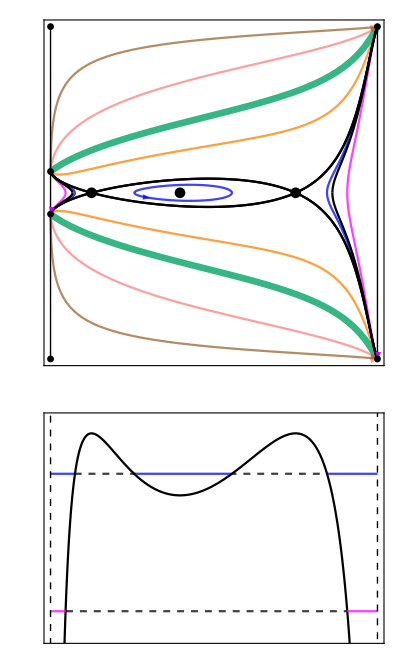

```mathematica
(*Plot the phase space and potential together*)
xYc4=GraphicsColumn[{PhaseSpacec4,Potentialc4},Spacings->{0,0}]
```

## Three Einstein Points: c5

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc5[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[5]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[5]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c5traj[1]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[2]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[3]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[4]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[5]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[6]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[7]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[8]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[9]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[10]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[11]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[12]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[13]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc5=Table[c5traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
FFSc5=Plot[{FFS[[5]],-FFS[[5]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc5=Plot[{CFS[xThreeEinsteinPointsc5][[5]],-CFS[xThreeEinsteinPointsc5][[5]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5=ListPlot[{{xThreeEinsteinPointsc5[[1]],0},{xThreeEinsteinPointsc5[[2]],0},{xThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between the accelerating and decelerating regions for this case*)
Accnc5=ContourPlot[Accn[[5]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

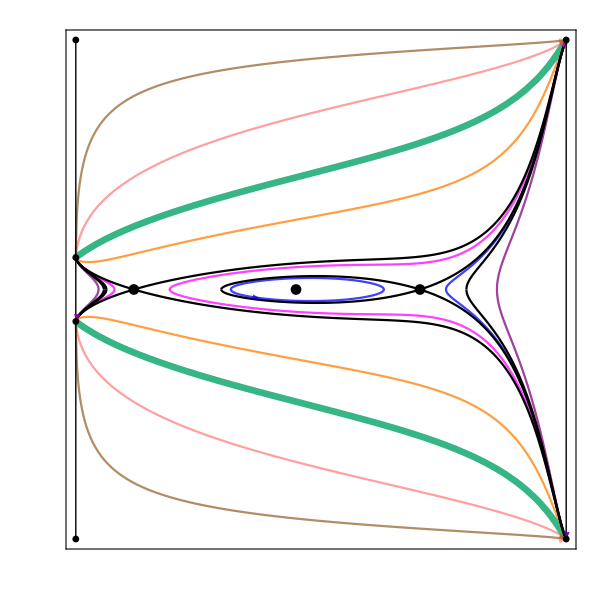

```mathematica
(*Show all components of the phase space*)
PhaseSpacec5=Show[Trajc5, FFSc5,CFSc5,Einsteinc5,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum of the potential*)
d2Udx2[xThreeEinsteinPointsc5[[1]],0.08][[5]]
```

-0.136758

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[2]],0.08][[5]]
```

0.0114056

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[3]],0.08][[5]]
```

-0.0211506

```mathematica
(*Plot the potential for this case*)
Uc5=Plot[{U[x,0.08][[5]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c5Energy[1]=Plot[{Energy[0.08,0.06][[5]]},{x,ℛ,0.11},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[2]=Plot[{Energy[0.08,0.06][[5]]},{x,0.355,0.63},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[3]=Plot[{Energy[0.08,0.06][[5]]},{x,0.775,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[4]=Plot[{Energy[0.08,0.065][[5]]},{x,0.235,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[5]=Plot[{Energy[0.08,0.065][[5]]},{x,ℛ,0.125},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[6]=Plot[{Energy[0.08,0.05][[5]]},{x,0.87,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[7]=Plot[{Energy[0.08,0.05][[5]]},{x,ℛ,0.095},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[8]=Plot[{Energy[0.08,0.11][[5]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energy[9]=Plot[{Energy[0.08,0.3][[5]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energy[10]=Plot[{Energy[0.08,0.6][[5]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c5Energy[11]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energy[12]=Plot[{Energy[0.08,0.06][[5]]},{x,0.11,0.355},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[13]=Plot[{Energy[0.08,0.06][[5]]},{x,0.63,0.775},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[14]=Plot[{Energy[0.08,0.065][[5]]},{x,0.125,0.235},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[15]=Plot[{Energy[0.08,0.05][[5]]},{x,0.095,0.87},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc5=Table[c5Energy[i],{i,1,15}];
```

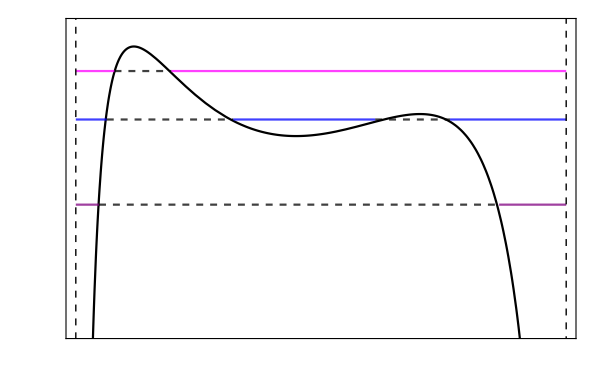

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5=Show[Uc5,Energyc5,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.0005Range[-29,-25]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.0145,-0.0125}}]
```

### Final Plot

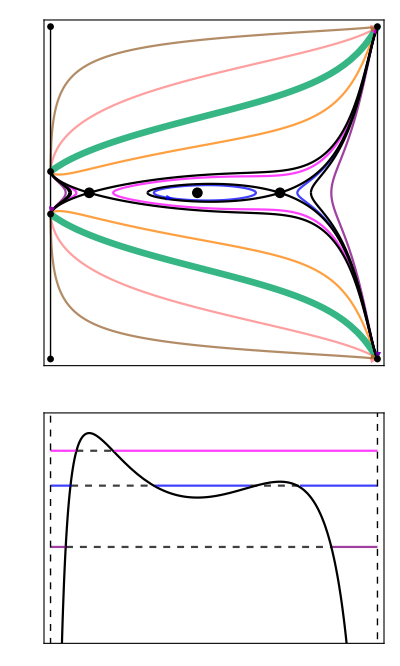

```mathematica
(*Plot the phase space and potential together*)
xYc5=GraphicsColumn[{PhaseSpacec5,Potentialc5},Spacings->{0,0}]
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc6[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[6]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[6]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c6traj[1]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[2]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[3]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[4]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0.3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[5]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[6]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[7]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[8]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[9]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[10]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc6=Table[c6traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
FFSc6=Plot[{FFS[[6]],-FFS[[6]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc6=Plot[{CFS[xTwoEinsteinPointsc6][[6]],-CFS[xTwoEinsteinPointsc6][[6]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->200];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6=ListPlot[{{xTwoEinsteinPointsc6[[1]],0},{xTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc6=ContourPlot[Accn[[6]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

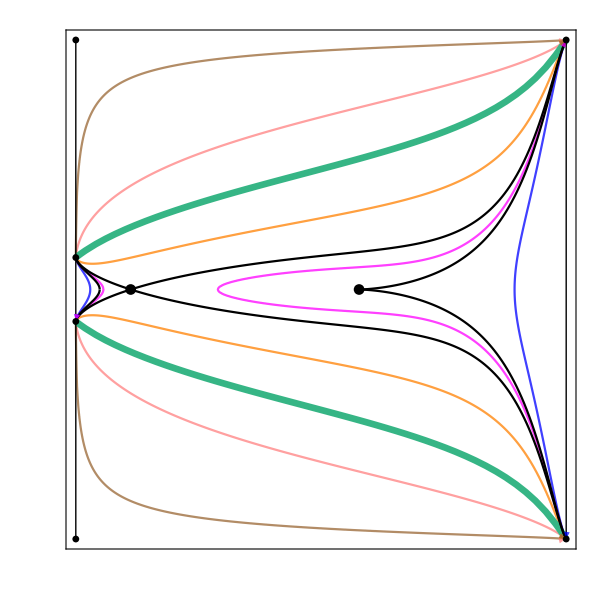

```mathematica
(*Show all components of the phase space*)
PhaseSpacec6=Show[Trajc6, FFSc6,CFSc6,Einsteinc6,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum*)
d2Udx2[xTwoEinsteinPointsc6[[1]],0.9][[6]]
```

-8.29826

```mathematica
d2Udx2[xTwoEinsteinPointsc6[[2]],0.9][[6]]
```

-8.28221×10^-8

```mathematica
(*Plot the potential for this case*)
Uc6=Plot[{U[x,0.9][[6]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c6Energy[1]=Plot[{Energy[0.9,0][[6]]},{x,ℛ,0.07},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[2]=Plot[{Energy[0.9,0][[6]]},{x,0.9,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[3]=Plot[{Energy[0.9,0.4][[6]]},{x,ℛ,0.105},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[4]=Plot[{Energy[0.9,0.4][[6]]},{x,0.322,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[5]=Plot[{Energy[0.9,0.6][[6]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energy[6]=Plot[{Energy[0.9,0.9][[6]]},{x,ℛ,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c6Energy[7]=Plot[{Energy[0.9,0.99][[6]]},{x,ℛ,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c6Energy[8]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energy[9]=Plot[{Energy[0.9,0][[6]]},{x,0.07,0.9},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[10]=Plot[{Energy[0.9,0.4][[6]]},{x,0.105,0.322},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc6=Table[c6Energy[i],{i,1,10}];
```

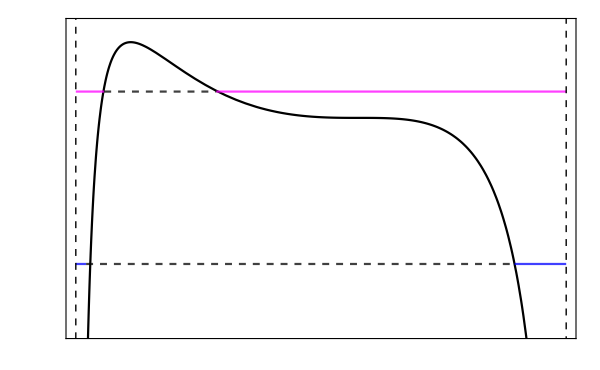

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6=Show[Uc6,Energyc6,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.05Range[-16,-13]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.8,-0.63}}]
```

### Final Plot

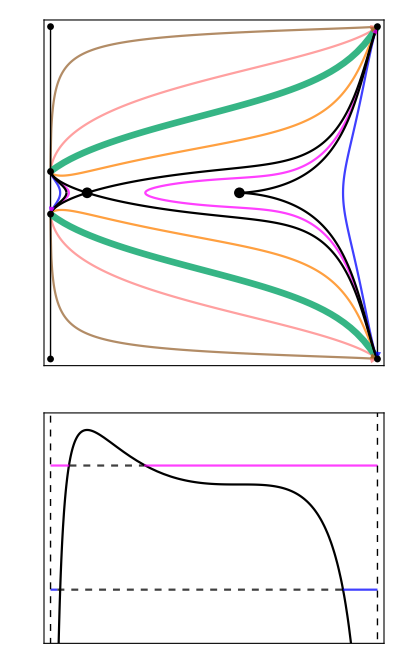

```mathematica
(*Plot the phase space and potential together*)
xYc6=GraphicsColumn[{PhaseSpacec6,Potentialc6},Spacings->{0,0}]
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc7[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[7]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[7]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,ℛ,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSc7=Plot[{FFS[[7]],-FFS[[7]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
CFSc7=Plot[{CFS[xOneEinsteinPointc7][[7]],-CFS[xOneEinsteinPointc7][[7]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{xOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between the accelerating and decelerating regions for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

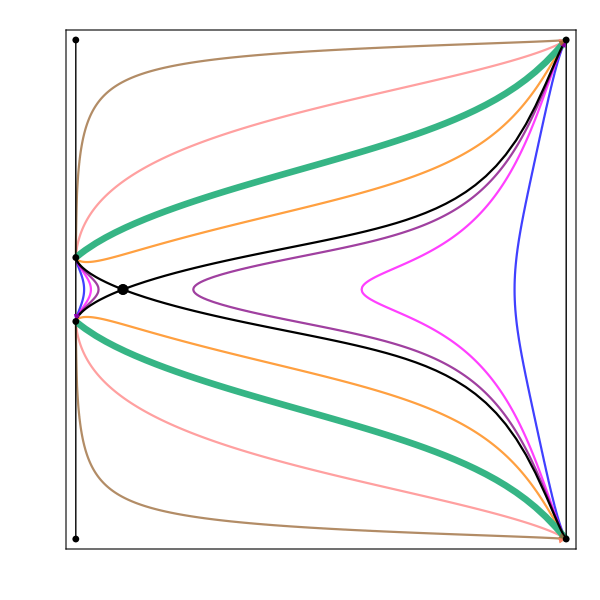

```mathematica
(*Show all components of the phase space*)
PhaseSpacec7=Show[Trajc7, FFSc7,CFSc7,Einsteinc7,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative of U(x) to find whether point is a maximum or a minimum of the potential*)
d2Udx2[xOneEinsteinPointc7,0.9][[7]]
```

-13.8623

```mathematica
(*Plot the potential for this case*)
Uc7=Plot[{U[x,0.9][[7]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c7Energy[1]=Plot[{Energy[0.9,0][[7]]},{x,0.9,1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[2]=Plot[{Energy[0.9,0][[7]]},{x,ℛ,0.06},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[3]=Plot[{Energy[0.9,0.5][[7]]},{x,0.6,1},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[4]=Plot[{Energy[0.9,0.5][[7]]},{x,ℛ,0.08},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[5]=Plot[{Energy[0.9,0.56][[7]]},{x,0.275,1},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[6]=Plot[{Energy[0.9,0.56][[7]]},{x,ℛ,0.099},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[7]=Plot[{Energy[0.9,0.7][[7]]},{x,ℛ,1},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energy[8]=Plot[{Energy[0.9,0.92][[7]]},{x,0.2,1},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energy[9]=Plot[{Energy[0.9,0.99][[7]]},{x,0.6,1},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c7Energy[10]=Plot[{0},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energy[11]=Plot[{Energy[0.9,0][[7]]},{x,0.06,0.9},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[12]=Plot[{Energy[0.9,0.5][[7]]},{x,0.08,0.6},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[13]=Plot[{Energy[0.9,0.56][[7]]},{x,0.099,0.275},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc7=Table[c7Energy[i],{i,1,13}];
```

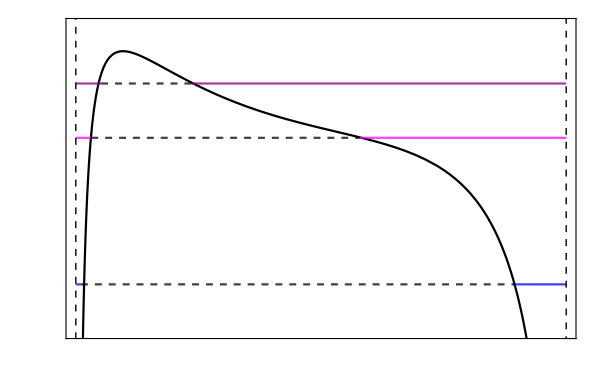

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7=Show[Uc7,Energyc7,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.1Range[-10,-7]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-1,-0.65}}]
```

### Final Plot

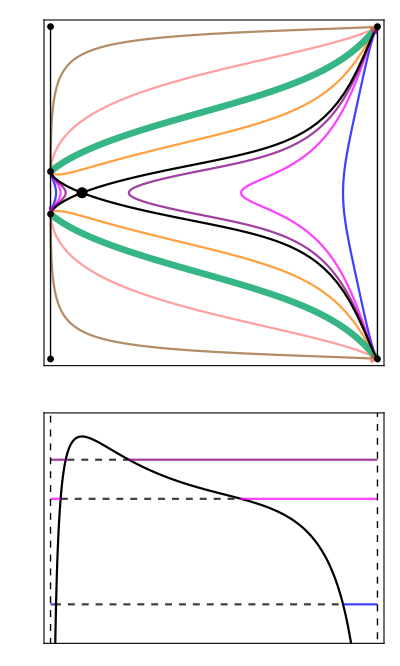

```mathematica
(*Plot the phase space and potential together*)
xYc7=GraphicsColumn[{PhaseSpacec7,Potentialc7},Spacings->{0,0}]
```

## Full System of Equations: 3-D x-Y-Z Phase Spaces

## Set-up for x-Y-Z Phase Spaces

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajxYZ[Y0_,x0_]:=x/3+z[x,c]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajxYZ[Y0_,x0_]=Sqrt[trajxYZ[Y0,x0]/(1+trajxYZ[Y0,x0])];
```

```mathematica
(*Plot the the common fixed points which exist in all of the phase spaces*)
FPShowxYZ=ListPointPlot3D[{{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,1,0},{ℛ,-1,0},{1,1,1},{1,-1,1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the surface where acceleration is zero*)
AccnxYZ=ContourPlot3D[Z/(1-Z)+x+2*r[x,cr]-3*ℛ+3*ℛ*x-3*x^2==0,{x,ℛ,1},{Y,-1,1},{Z,0,1}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

## One Einstein Point: c1

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c1trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.12,0.2][[1]],Z[x,c[[1]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,0.9},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->8000]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.18,0.2][[1]],Z[x,c[[1]]]},{x,0.9,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->All]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.225,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.5,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.2][[1]],Z[x,c[[1]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajc1=Table[c1trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc1=ListPointPlot3D[{{xOneEinsteinPointc1,0,ZOneEinsteinPointc1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc1=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]},{x,-CFS[xOneEinsteinPointc1][[1]],Z[x,c[[1]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc1=ParametricPlot3D[{{x,FFS[[1]],Z[x,c[[1]]]},{x,-FFS[[1]],Z[x,c[[1]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
Surfacec1=ParametricPlot3D[{x,Y,Z[x,c[[1]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc1=Show[CFSc1,FFSc1, Einsteinc1,FPShowxYZ,Surfacec1,trajc1,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Two Einstein Points: c2

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c2trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,0.8},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.085,0.1][[2]],Z[x,c[[2]]]},{x,0.8,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.13,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.4,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.9,0.1][[2]],Z[x,c[[2]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajc2=Table[c2trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc2=ListPointPlot3D[{{xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]]},{xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc2=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[1]]][[2]],Z[x,c[[2]]]},{x,CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]},{x,-CFS[xTwoEinsteinPointsc2[[2]]][[2]],Z[x,c[[2]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc2=ParametricPlot3D[{{x,FFS[[2]],Z[x,c[[2]]]},{x,-FFS[[2]],Z[x,c[[2]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
Surfacec2=ParametricPlot3D[{x,Y,Z[x,c[[2]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc2=Show[CFSc2,FFSc2, Einsteinc2,FPShowxYZ,Surfacec2,trajc2,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Three Einstein Points: c3

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c3trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.2,0.5},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.071,0.08][[3]],Z[x,c[[3]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.08,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.04,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.12,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[3]],Z[x,c[[3]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
trajc3=Table[c3trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc3=ListPointPlot3D[{{xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]]},{xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]]},{xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc3=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[1]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[2]]][[3]],Z[x,c[[3]]]},{x,CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]},{x,-CFS[xThreeEinsteinPointsc3[[3]]][[3]],Z[x,c[[3]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc3=ParametricPlot3D[{{x,FFS[[3]],Z[x,c[[3]]]},{x,-FFS[[3]],Z[x,c[[3]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
Surfacec3=ParametricPlot3D[{x,Y,Z[x,c[[3]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc3=Show[CFSc3,FFSc3, Einsteinc3,FPShowxYZ,Surfacec3,trajc3,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Three Einstein Points: c4

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c4trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[3]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[4]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[4]],Z[x,c[[4]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[9]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[10]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[11]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[12]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[13]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajxYZ[14]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[4]],Z[x,c[[4]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc4=Table[c4trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc4=ListPointPlot3D[{{xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]]},{xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]]},{xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc4=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[1]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[2]]][[4]],Z[x,c[[4]]]},{x,CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]},{x,-CFS[xThreeEinsteinPointsc4[[3]]][[4]],Z[x,c[[4]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc4=ParametricPlot3D[{{x,FFS[[4]],Z[x,c[[4]]]},{x,-FFS[[4]],Z[x,c[[4]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
Surfacec4=ParametricPlot3D[{x,Y,Z[x,c[[4]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc4=Show[CFSc4,FFSc4, Einsteinc4,FPShowxYZ,Surfacec4,trajc4,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Three Einstein Points: c5

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c5trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500,AxesLabel->{"Y","x","Z"}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.2,0.7},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.06,0.08][[5]],Z[x,c[[5]]]},{x,0.7,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.065,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.05,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.11,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.3,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.6,0.08][[5]],Z[x,c[[5]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc5=Table[c5trajxYZ[i],{i,1,16}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc5=ListPointPlot3D[{{xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]]},{xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]]},{xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc5=ParametricPlot3D[{{x,CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[1]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[2]]][[5]],Z[x,c[[5]]]},{x,CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]},{x,-CFS[xThreeEinsteinPointsc5[[3]]][[5]],Z[x,c[[5]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc5=ParametricPlot3D[{{x,FFS[[5]],Z[x,c[[5]]]},{x,-FFS[[5]],Z[x,c[[5]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
Surfacec5=ParametricPlot3D[{x,Y,Z[x,c[[5]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc5=Show[CFSc5,FFSc5, Einsteinc5,FPShowxYZ,Surfacec5,trajc5,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Two Einstein Points: c6

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c6trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[6]],Z[x,c[[6]]]},{x,0.6,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.4,0.9][[6]],Z[x,c[[6]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.6,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.9,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[6]],Z[x,c[[6]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc6=Table[c6trajxYZ[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc6=ListPointPlot3D[{{xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]]},{xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc6=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[1]]][[6]],Z[x,c[[6]]]},{x,CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]},{x,-CFS[xTwoEinsteinPointsc6[[2]]][[6]],Z[x,c[[6]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc6=ParametricPlot3D[{{x,FFS[[6]],Z[x,c[[6]]]},{x,-FFS[[6]],Z[x,c[[6]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first intergral (c) surface*)
Surfacec6=ParametricPlot3D[{x,Y,Z[x,c[[6]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc6=Show[CFSc6,FFSc6, Einsteinc6,FPShowxYZ,Surfacec6,trajc6,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## One Einstein Point: c7

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c7trajxYZ[1]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[2]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[3]=ParametricPlot3D[{x,trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[4]=ParametricPlot3D[{x,-trajxYZ[0,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[5]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[6]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[7]=ParametricPlot3D[{x,trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[8]=ParametricPlot3D[{x,-trajxYZ[0.5,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[9]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[10]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,0.2},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[11]=ParametricPlot3D[{x,trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[12]=ParametricPlot3D[{x,-trajxYZ[0.56,0.9][[7]],Z[x,c[[7]]]},{x,0.2,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[13]=ParametricPlot3D[{x,trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[14]=ParametricPlot3D[{x,-trajxYZ[0.7,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[15]=ParametricPlot3D[{x,trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[16]=ParametricPlot3D[{x,-trajxYZ[0.92,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[17]=ParametricPlot3D[{x,trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajxYZ[18]=ParametricPlot3D[{x,-trajxYZ[0.99,0.9][[7]],Z[x,c[[7]]]},{x,ℛ,1},AxesLabel->{"x","Y","Z"},PlotStyle -> {{Gray}},PlotPoints->500]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
trajc7=Table[c7trajxYZ[i],{i,1,18}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
Einsteinc7=ListPointPlot3D[{{xOneEinsteinPointc7,0,ZOneEinsteinPointc7}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
CFSc7=ParametricPlot3D[{{x,CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]},{x,-CFS[xOneEinsteinPointc7][[7]],Z[x,c[[7]]]}},{x,ℛ,1},PlotStyle->Black,PlotRange->All,PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
FFSc7=ParametricPlot3D[{{x,FFS[[7]],Z[x,c[[7]]]},{x,-FFS[[7]],Z[x,c[[7]]]}},{x,ℛ,1},PlotStyle->{RGBColor[0.21,0.71,0.52]},PlotRange->All];
```

```mathematica
(*Plot the first intergral (c) surface*)
Surfacec7=ParametricPlot3D[{x,Y,Z[x,c[[7]]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYZc7=Show[CFSc7,FFSc7, Einsteinc7,FPShowxYZ,Surfacec7,trajc7,PlotRange->{{0,1},{-1,1},{0,1}},ImageSize->{600,400},AxesLabel->{"x","Y","Z"}]
```

-Graphics3D-

## Full System of Equations: a-y Phase Spaces and Potentials

## Set-up

### Variables in terms of a

```mathematica
(*Express the dark matter (z), radiation (r) and dark energy (x) in terms of the scale factor (a)*)
xa[a_,x0_]=(a^(-3*(1-ℛ))+ca[x0]*ℛ)/(a^(-3*(1-ℛ))+ca[x0]);

za[a_,x0_,c_]=c*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(1/(1-ℛ));

ra[a_,x0_,cr_]=cr*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(4/(3*(1-ℛ)));
```

```mathematica
(*Define f(a), the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When f = 0, there is an Einstein fixed point*)
fa[a_,x0_,c_,cr_]=za[a,x0,c]+2*ra[a,x0,cr]-3*ℛ+xa[a,x0]*(1+3*ℛ)-3*xa[a,x0]^2;
```

### Set up for plots of the phase space

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS) in terms of y^2, which is found from the Friedmann equation*)
ffsay[a_,x0_]=(1/3)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Take the square root of ffsay for y*)
(*Note that when plotting the FFS, +FFSay and -FFSay needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSay[a_,x0_]=Sqrt[ffsay[a,x0]];
```

```mathematica
(*Define the equation for the Closed Friedmann Separatrix (CFS) in terms of y^2, which is found from th Friedmann equation*)
(*aE denotes the value of a at an Einstein fixed point*)
cfsay[a_,aE_,x0_]= xa[a,x0]/3+za[a,x0,c]/3+ra[a,x0,cr]/3-((aE/a)^2)*(xa[aE,x0]/3+za[aE,x0,c]/3+ra[aE,x0,cr]/3);
```

```mathematica
(*Take the square root of cfsay for y*)
(*Note that when plotting the CFS, +CFSay and -CFSay needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFSay[a_,aE_,x0_]=Sqrt[cfsay[a,aE,x0]];
```

```mathematica
(*Define the acceleration equation*)
Accnay=za[a,x0,c]+xa[a,x0]+2*ra[a,x0,cr]-3*ℛ+3*ℛ*xa[a,x0]-3*xa[a,x0]^2;
```

### Set up for the plots of the potential

```mathematica
(*Define a0 = 1 today*)
a0=1;
```

```mathematica
(*Define the potential term Ua^2*)
Uay[a_,x0_]=-(a^2/6)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Define the energy of the trajectories*)
Energyay[x0_,y0_]=-(xa[a0,x0]/6+za[a0,x0,c]/6+ra[a0,x0,cr]/6-y0^2/2);
```

## Find the Einstein Points in Each Case

### One Einstein Point: c1

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed point*)
aOneEinsteinPointc1=FindRoot[fa[a,0.2,c,cr][[1]]==0,{a,0.2}]
```

{a→0.172295}

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc1=a/.aOneEinsteinPointc1
```

0.172295

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aTwoEinsteinPointsc2i=FindRoot[fa[a,0.1,c,cr][[2]]==0,{a,0.1}];
aTwoEinsteinPointsc2ii=FindRoot[fa[a,0.1,c,cr][[2]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc2={a/.aTwoEinsteinPointsc2i,a/.aTwoEinsteinPointsc2ii}
```

{0.189406,0.580945}

### Three Einstein Points: c3

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aThreeEinsteinPointsc3i=FindRoot[fa[a,0.08,c,cr][[3]]==0,{a,0.1}];
aThreeEinsteinPointsc3ii=FindRoot[fa[a,0.08,c,cr][[3]]==0,{a,0.4}];
aThreeEinsteinPointsc3iii=FindRoot[fa[a,0.08,c,cr][[3]]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc3={a/.aThreeEinsteinPointsc3i,a/.aThreeEinsteinPointsc3ii,a/.aThreeEinsteinPointsc3iii}
```

{0.175793,0.401739,0.555757}

### Three Einstein Points: c4

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aThreeEinsteinPointsc4i=FindRoot[fa[a,0.08,c,cr][[4]]==0,{a,0.1}];
aThreeEinsteinPointsc4ii=FindRoot[fa[a,0.08,c,cr][[4]]==0,{a,0.4}];
aThreeEinsteinPointsc4iii=FindRoot[fa[a,0.08,c,cr][[4]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc4={a/.aThreeEinsteinPointsc4i,a/.aThreeEinsteinPointsc4ii,a/.aThreeEinsteinPointsc4iii}
```

{0.204752,0.348904,0.594593}

### Three Einstein Points: c5

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aThreeEinsteinPointsc5i=FindRoot[fa[a,0.08,c,cr][[5]]==0,{a,0.1}];
aThreeEinsteinPointsc5ii=FindRoot[fa[a,0.08,c,cr][[5]]==0,{a,0.4}];
aThreeEinsteinPointsc5iii=FindRoot[fa[a,0.08,c,cr][[5]]==0,{a,0.6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc5={a/.aThreeEinsteinPointsc5i,a/.aThreeEinsteinPointsc5ii,a/.aThreeEinsteinPointsc5iii}
```

{0.222807,0.323219,0.608681}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aTwoEinsteinPointsc6i=FindRoot[fa[a,0.9,c,cr][[6]]==0,{a,2}];
aTwoEinsteinPointsc6ii=FindRoot[fa[a,0.9,c,cr][[6]]==0,{a,6}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc6={a/.aTwoEinsteinPointsc6i,a/.aTwoEinsteinPointsc6ii}
```

{1.89836,4.38258}

### One Einstein Point: c7

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed point*)
aOneEinsteinPointc7=FindRoot[fa[a,0.9,c,cr][[7]]==0,{a,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc7=a/.aOneEinsteinPointc7
```

4.65011

## One Einstein Point: c1

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)trajc1ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[1]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[1]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c1trajay[1]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[2]=ContourPlot[Evaluate[trajc1ay[0,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[3]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[4]=ContourPlot[Evaluate[trajc1ay[0.12,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[5]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,0,aOneEinsteinPointc1},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[6]=ContourPlot[Evaluate[trajc1ay[0.18,0.2]],{a,aOneEinsteinPointc1,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[7]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[8]=ContourPlot[Evaluate[trajc1ay[0.23,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[9]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[10]=ContourPlot[Evaluate[trajc1ay[0.58,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[11]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1trajay[12]=ContourPlot[Evaluate[trajc1ay[2.06,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc1ay=Table[c1trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSc1ay=Plot[{FFSay[a,0.2][[1]],-FFSay[a,0.2][[1]]},{a,0,3},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc1ay=Plot[{CFSay[a,aOneEinsteinPointc1,0.2][[1]],-CFSay[a,aOneEinsteinPointc1,0.2][[1]]},{a,0,3},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1ay=ListPlot[{{aOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between the accelerating and decelerating regions for this case*)
Accnc1ay=ContourPlot[Accnay[[1]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

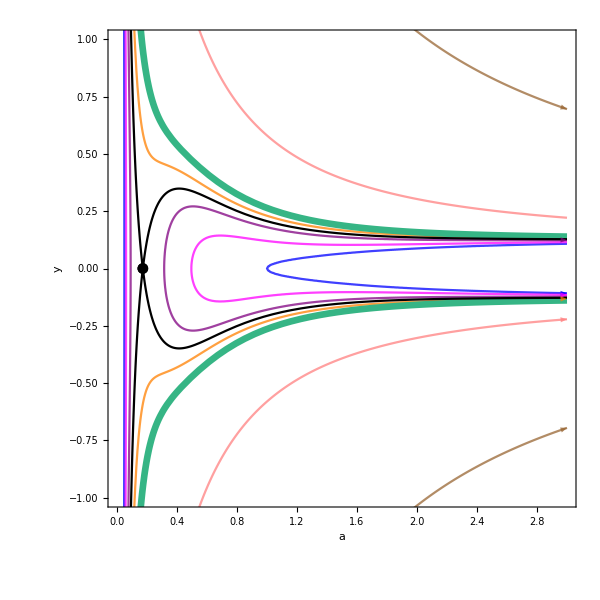

```mathematica
(*Show all components of the phase space*)
PhaseSpacec1ay=Show[trajc1ay,FFSc1ay,CFSc1ay,Einsteinc1ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc1ay=Plot[{Uay[a,0.2][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c1Energyay[1]=Plot[{Energyay[0.2,0][[1]]},{a,0,0.04},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[2]=Plot[{Energyay[0.2,0][[1]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energyay[3]=Plot[{Energyay[0.2,0.12][[1]]},{a,0,0.055},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[4]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.5,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energyay[5]=Plot[{Energyay[0.2,0.18][[1]]},{a,0,0.08},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[6]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.32,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energyay[7]=Plot[{Energyay[0.2,0.23][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energyay[8]=Plot[{Energyay[0.2,0.58][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energyay[9]=Plot[{Energyay[0.2,2.06][[1]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c1Energyay[10]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energyay[11]=Plot[{Energyay[0.2,0][[1]]},{a,0.04,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[12]=Plot[{Energyay[0.2,0.12][[1]]},{a,0.055,0.5},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energyay[13]=Plot[{Energyay[0.2,0.18][[1]]},{a,0.08,0.32},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc1ay=Table[c1Energyay[i],{i,1,13}];
```

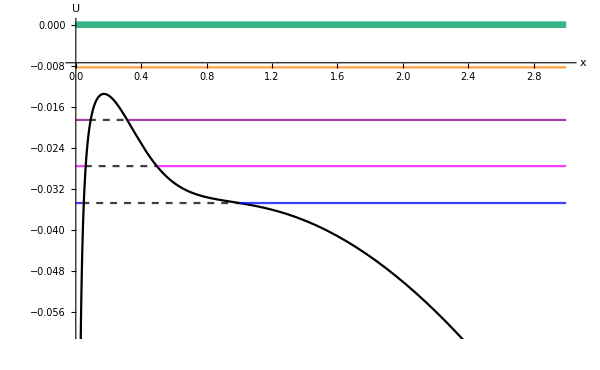

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc1ay=Show[Uc1ay,Energyc1ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.06,0}]
```

### Final Plot

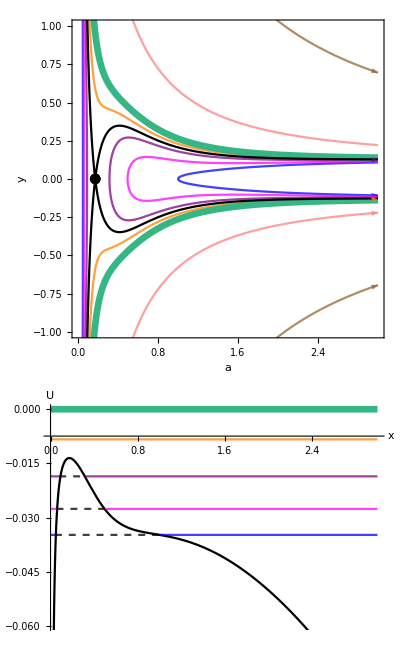

```mathematica
(*Plot the phase space and potential together*)
ayc1=GraphicsColumn[{PhaseSpacec1ay,Potentialc1ay},Spacings->{0,-20}]
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc2ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[2]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[2]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c2trajay[1]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[2]=ContourPlot[Evaluate[trajc2ay[0,0.1]],{a,aTwoEinsteinPointsc2[[2]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[3]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[4]=ContourPlot[Evaluate[trajc2ay[0.07,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[5]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,0,aTwoEinsteinPointsc2[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[6]=ContourPlot[Evaluate[trajc2ay[0.09,0.1]],{a,aTwoEinsteinPointsc2[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[7]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[8]=ContourPlot[Evaluate[trajc2ay[0.131,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[9]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[10]=ContourPlot[Evaluate[trajc2ay[0.44,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[11]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2trajay[12]=ContourPlot[Evaluate[trajc2ay[1,0.1]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajc2ay=Table[c2trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSc2ay=Plot[{FFSay[a,0.2][[2]],-FFSay[a,0.1][[2]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc2ay=Plot[{CFSay[a,aTwoEinsteinPointsc2,0.1][[2]],-CFSay[a,aTwoEinsteinPointsc2,0.1][[2]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2ay=ListPlot[{{aTwoEinsteinPointsc2[[1]],0},{aTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc2ay=ContourPlot[Accnay[[2]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

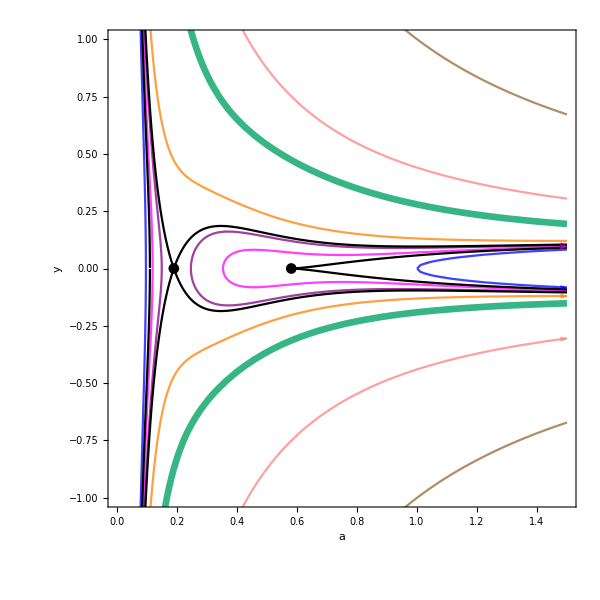

```mathematica
(*Show all components of the phase space*)
PhaseSpacec2ay=Show[trajc2ay,FFSc2ay,CFSc2ay,Einsteinc2ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc2ay=Plot[{Uay[a,0.1][[2]]},{a,0,1.5},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c2Energyay[1]=Plot[{Energyay[0.1,0][[2]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[2]=Plot[{Energyay[0.1,0][[2]]},{a,1,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energyay[3]=Plot[{Energyay[0.1,0.07][[2]]},{a,0,0.12},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[4]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.355,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energyay[5]=Plot[{Energyay[0.1,0.09][[2]]},{a,0,0.145},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[6]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.245,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energyay[7]=Plot[{Energyay[0.1,0.131][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energyay[8]=Plot[{Energyay[0.1,0.44][[2]]},{a,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energyay[9]=Plot[{Energyay[0.1,1][[2]]},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c2Energyay[10]=Plot[{0},{a,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energyay[11]=Plot[{Energyay[0.1,0][[2]]},{a,0.09,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[12]=Plot[{Energyay[0.1,0.07][[2]]},{a,0.12,0.355},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energyay[13]=Plot[{Energyay[0.1,0.09][[2]]},{a,0.145,0.245},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc2ay=Table[c2Energyay[i],{i,1,13}];
```

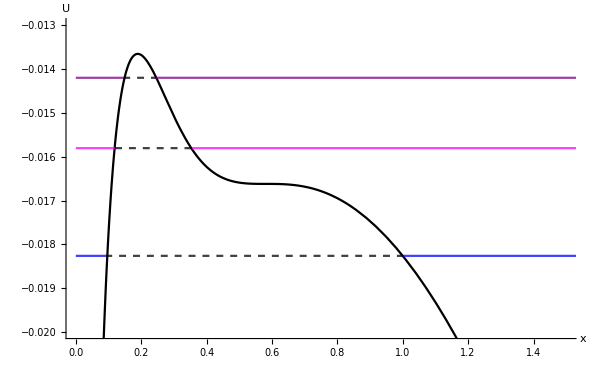

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc2ay=Show[Uc2ay,Energyc2ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.5},{-0.02,-0.013}}]
```

### Final Plot

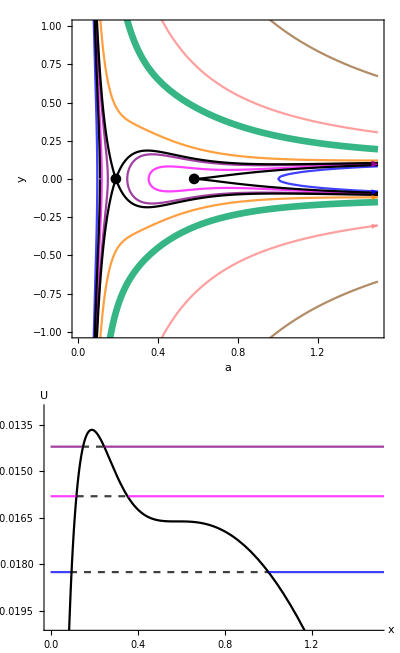

```mathematica
(*Plot the phase space and potential together*)
ayc2=GraphicsColumn[{PhaseSpacec2ay,Potentialc2ay},Spacings->{0,-20}]
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc3ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[3]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[3]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trjaectories with different initial conditions*)
```

```mathematica
c3trajay[1]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[2]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[1]],aThreeEinsteinPointsc3[[3]]},{y,-1.5,1.5},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[3]=ContourPlot[Evaluate[trajc3ay[0.071,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[4]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[5]=ContourPlot[Evaluate[trajc3ay[0.08,0.08]],{a,aThreeEinsteinPointsc3[[1]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[6]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,0,aThreeEinsteinPointsc3[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[7]=ContourPlot[Evaluate[trajc3ay[0.04,0.08]],{a,aThreeEinsteinPointsc3[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[8]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[9]=ContourPlot[Evaluate[trajc3ay[0.121,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[10]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[11]=ContourPlot[Evaluate[trajc3ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[12]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajay[13]=ContourPlot[Evaluate[trajc3ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc3ay=Table[c3trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
FFSc3ay=Plot[{FFSay[a,0.08][[3]],-FFSay[a,0.08][[3]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc3ay=Plot[{CFSay[a,aThreeEinsteinPointsc3,0.08][[3]],-CFSay[a,aThreeEinsteinPointsc3,0.08][[3]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3ay=ListPlot[{{aThreeEinsteinPointsc3[[1]],0},{aThreeEinsteinPointsc3[[2]],0},{aThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decleerating regions for this case*)
Accnc3ay=ContourPlot[Accna[[3]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

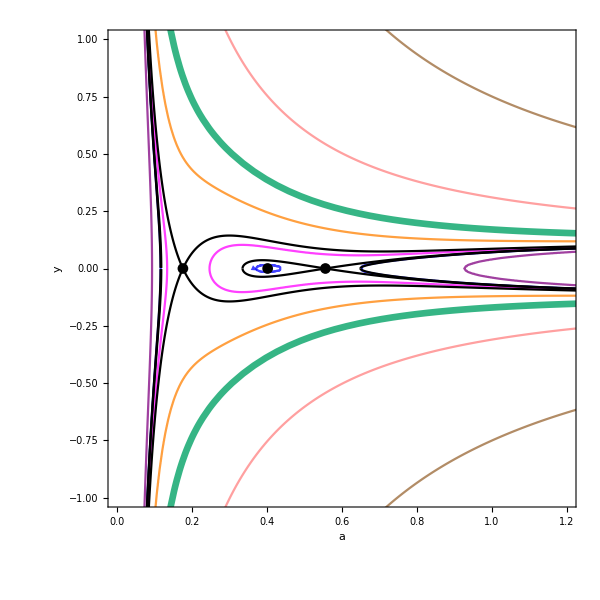

```mathematica
(*Show all components of the phase space*)
PhaseSpacec3ay=Show[trajc3ay,FFSc3ay,CFSc3ay,Einsteinc3ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc3ay=Plot[{Uay[a,0.08][[3]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c3Energyay[1]=Plot[{Energyay[0.08,0.071][[3]]},{a,0,0.115},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[2]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.37,0.43},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[3]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.64,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energyay[4]=Plot[{Energyay[0.08,0.08][[3]]},{a,0,0.13},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[5]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.25,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energyay[6]=Plot[{Energyay[0.08,0.04][[3]]},{a,0,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[7]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.925,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energyay[8]=Plot[{Energyay[0.08,0.121][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energyay[9]=Plot[{Energyay[0.08,0.31][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energyay[10]=Plot[{Energyay[0.08,0.75][[3]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c3Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energyay[12]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.115,0.37},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[13]=Plot[{Energyay[0.08,0.071][[3]]},{a,0.43,0.64},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[14]=Plot[{Energyay[0.08,0.08][[3]]},{a,0.13,0.25},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energyay[15]=Plot[{Energyay[0.08,0.04][[3]]},{a,0.09,0.925},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc3ay=Table[c3Energyay[i],{i,1,15}];
```

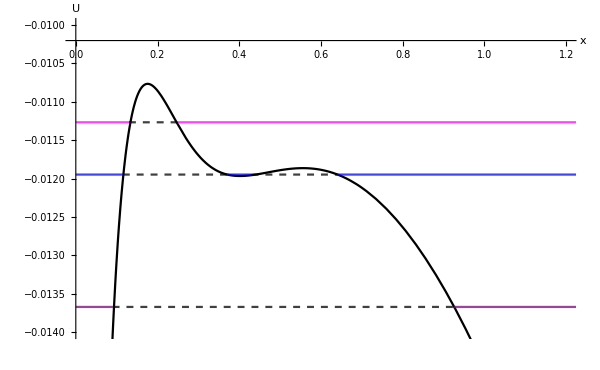

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc3ay=Show[Uc3ay,Energyc3ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.014,-0.01}}]
```

### Final Plot

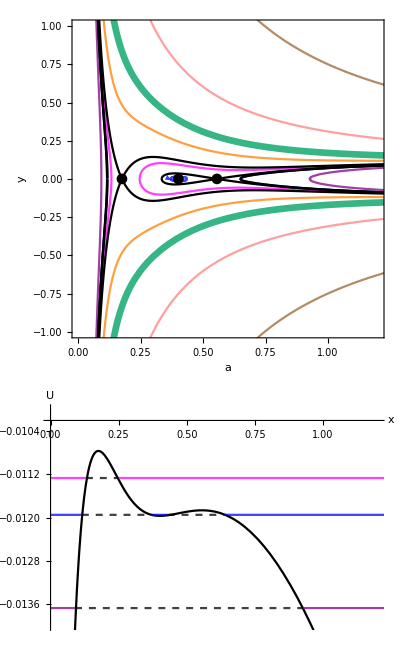

```mathematica
(*Plot the phase space and potential together*)
ayc3=GraphicsColumn[{PhaseSpacec3ay,Potentialc3ay},Spacings->{0,-20}]
```

## Three Einstein Points: c4

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc4ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[4]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[4]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c4trajay[1]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[2]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[1]],aThreeEinsteinPointsc4[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,.02,0,0,.02,0,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[3]=ContourPlot[Evaluate[trajc4ay[0.065,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[4]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc4[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[5]=ContourPlot[Evaluate[trajc4ay[0.05,0.08]],{a,aThreeEinsteinPointsc4[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[6]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[7]=ContourPlot[Evaluate[trajc4ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[8]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[9]=ContourPlot[Evaluate[trajc4ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[10]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4trajay[11]=ContourPlot[Evaluate[trajc4ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc4ay=Table[c4trajay[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
FFSc4ay=Plot[{FFSay[a,0.08][[4]],-FFSay[a,0.08][[4]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc4ay=Plot[{CFSay[a,aThreeEinsteinPointsc4,0.08][[4]],-CFSay[a,aThreeEinsteinPointsc4,0.08][[4]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4ay=ListPlot[{{aThreeEinsteinPointsc4[[1]],0},{aThreeEinsteinPointsc4[[2]],0},{aThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc4ay=ContourPlot[Accnya[[4]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

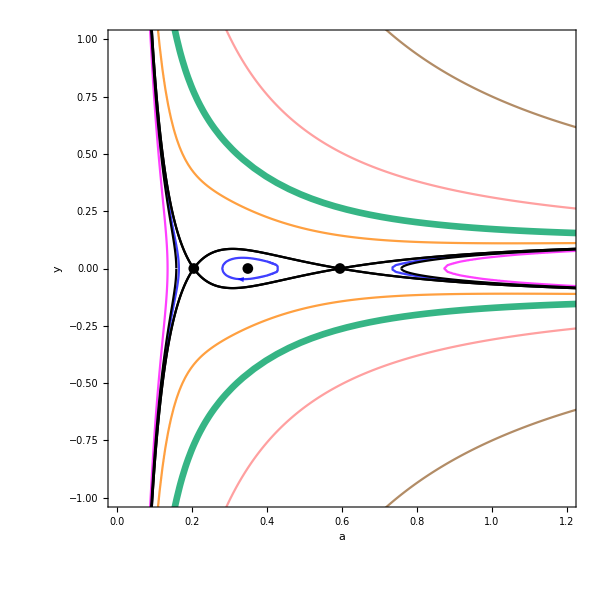

```mathematica
(*Show all components of the phase space*)
PhaseSpacec4ay=Show[trajc4ay,FFSc4ay,CFSc4ay,Einsteinc4ay,PlotRange->{{0,1.2},{-1,1}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc4ay=Plot[{Uay[a,0.08][[4]]},{a,0,1.2},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c4Energyay[1]=Plot[{Energyay[0.08,0.065][[4]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[2]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.28,0.435},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[3]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.73,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energyay[4]=Plot[{Energyay[0.08,0.05][[4]]},{a,0,0.135},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[5]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energyay[6]=Plot[{Energyay[0.08,0.11][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energyay[7]=Plot[{Energyay[0.08,0.31][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energyay[8]=Plot[{Energyay[0.08,0.75][[4]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c4Energyay[9]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energyay[10]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.16,0.28},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[11]=Plot[{Energyay[0.08,0.065][[4]]},{a,0.435,0.73},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energyay[12]=Plot[{Energyay[0.08,0.05][[4]]},{a,0.135,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc4ay=Table[c4Energyay[i],{i,1,12}];
```

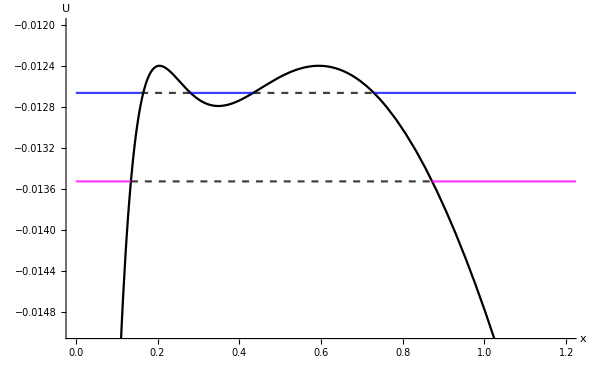

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc4ay=Show[Uc4ay,Energyc4ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.2},{-0.015,-0.012}}]
```

### Final Plot

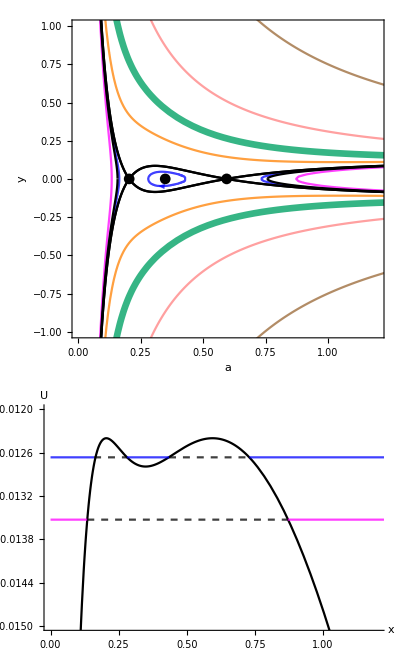

```mathematica
(*Plot the phase space and potential together*)
ayc4=GraphicsColumn[{PhaseSpacec4ay,Potentialc4ay},Spacings->{0,-20}]
```

## Three Einstein Points: c5

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc5ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[5]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[5]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c5trajay[1]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[2]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[1]],aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[3]=ContourPlot[Evaluate[trajc5ay[0.06,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[4]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,0,aThreeEinsteinPointsc5[[3]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[5]=ContourPlot[Evaluate[trajc5ay[0.065,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[6]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,0,aThreeEinsteinPointsc5[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[7]=ContourPlot[Evaluate[trajc5ay[0.05,0.08]],{a,aThreeEinsteinPointsc5[[3]],1.5},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[8]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[9]=ContourPlot[Evaluate[trajc5ay[0.11,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[10]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[11]=ContourPlot[Evaluate[trajc5ay[0.31,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[12]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5trajay[13]=ContourPlot[Evaluate[trajc5ay[0.75,0.08]],{a,0,1.5},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc5ay=Table[c5trajay[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
FFSc5ay=Plot[{FFSay[a,0.08][[5]],-FFSay[a,0.08][[5]]},{a,0,1.5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc5ay=Plot[{CFSay[a,aThreeEinsteinPointsc5,0.08][[5]],-CFSay[a,aThreeEinsteinPointsc5,0.08][[5]]},{a,0,1.5},PlotStyle->{Black},PlotRange->All,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5ay=ListPlot[{{aThreeEinsteinPointsc5[[1]],0},{aThreeEinsteinPointsc5[[2]],0},{aThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc5ay=ContourPlot[Accnay[[5]]==0,{a,0,1.5},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

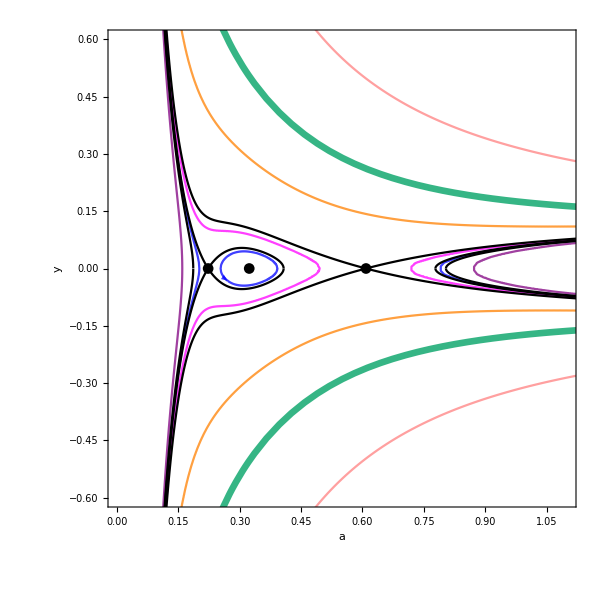

```mathematica
(*Show all components of the phase space*)
PhaseSpacec5ay=Show[trajc5ay,FFSc5ay,CFSc5ay,Einsteinc5ay,PlotRange->{{0,1.1},{-0.6,0.6}},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc5ay=Plot[{Uay[a,0.08][[5]]},{a,0,1.1},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c5Energyay[1]=Plot[{Energyay[0.08,0.06][[5]]},{a,0,0.195},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[2]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.26,0.39},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[3]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.785,3},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energyay[4]=Plot[{Energyay[0.08,0.065][[5]]},{a,0,0.495},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[5]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.715,3},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energyay[6]=Plot[{Energyay[0.08,0.05][[5]]},{a,0,0.16},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[7]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.87,3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energyay[8]=Plot[{Energyay[0.08,0.11][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energyay[9]=Plot[{Energyay[0.08,0.31][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energyay[10]=Plot[{Energyay[0.08,0.75][[5]]},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c5Energyay[11]=Plot[{0},{a,0,3},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energyay[12]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.195,0.26},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[13]=Plot[{Energyay[0.08,0.06][[5]]},{a,0.39,0.785},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[14]=Plot[{Energyay[0.08,0.065][[5]]},{a,0.495,0.715},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energyay[15]=Plot[{Energyay[0.08,0.05][[5]]},{a,0.16,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc5ay=Table[c5Energyay[i],{i,1,15}];
```

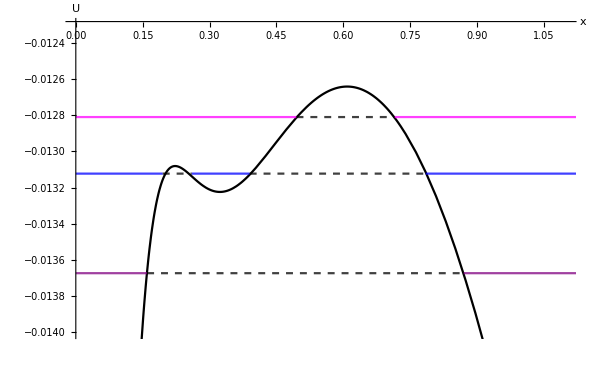

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc5ay=Show[Uc5ay,Energyc5ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{{0,1.1},{-0.014,-0.0123}}]
```

### Final Plot

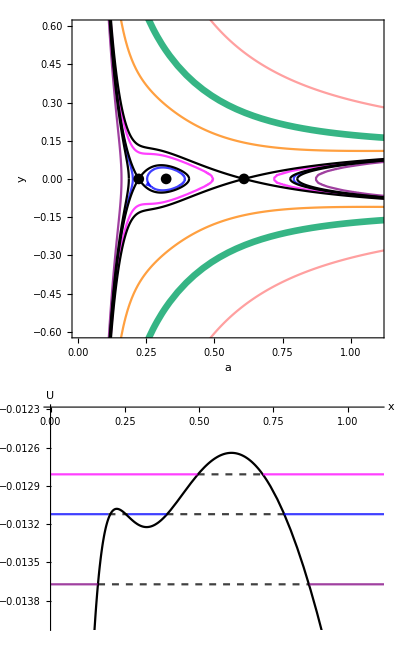

```mathematica
(*Plot the phase space and potential together*)
ayc5=GraphicsColumn[{PhaseSpacec5ay,Potentialc5ay},Spacings->{0,-20}]
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc6ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[6]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[6]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c6trajay[1]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,0,aTwoEinsteinPointsc6[[1]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[2]=ContourPlot[Evaluate[trajc6ay[0,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[3]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,0,aTwoEinsteinPointsc6[[2]]},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[4]=ContourPlot[Evaluate[trajc6ay[0.44,0.9]],{a,aTwoEinsteinPointsc6[[2]],10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[5]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[6]=ContourPlot[Evaluate[trajc6ay[0.75,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[7]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[8]=ContourPlot[Evaluate[trajc6ay[2.06,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[9]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6trajay[10]=ContourPlot[Evaluate[trajc6ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc6ay=Table[c6trajay[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
FFSc6ay=Plot[{FFSay[a,0.9][[6]],-FFSay[a,0.9][[6]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc6ay=Plot[{CFSay[a,aTwoEinsteinPointsc6,0.9][[6]],-CFSay[a,aTwoEinsteinPointsc6,0.9][[6]]},{a,0.1,10},PlotStyle->{Black},PlotRange->All,PlotPoints->100];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6ay=ListPlot[{{aTwoEinsteinPointsc6[[1]],0},{aTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnac6ay=ContourPlot[Accnay[[6]]==0,{a,0,10},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

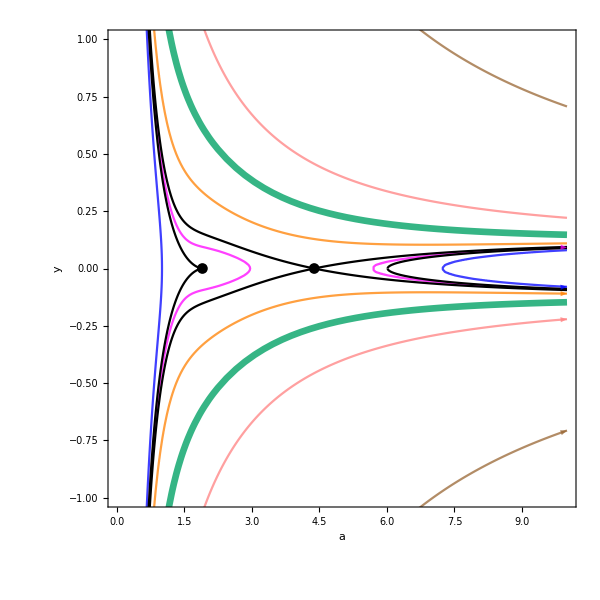

```mathematica
(*Show all components of the phase space*)
PhaseSpacec6ay=Show[trajc6ay,FFSc6ay,CFSc6ay,Einsteinc6ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc6ay=Plot[{Uay[a,0.9][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c6Energyay[1]=Plot[{Energyay[0.9,0][[6]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[2]=Plot[{Energyay[0.9,0][[6]]},{a,7.2,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energyay[3]=Plot[{Energyay[0.9,0.44][[6]]},{a,0,2.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[4]=Plot[{Energyay[0.9,0.44][[6]]},{a,5.65,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energyay[5]=Plot[{Energyay[0.9,0.75][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energyay[6]=Plot[{Energyay[0.9,2.06][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c6Energyay[7]=Plot[{Energyay[0.9,7.02][[6]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c6Energyay[8]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energyay[9]=Plot[{Energyay[0.9,0][[6]]},{a,1,7.2},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energyay[10]=Plot[{Energyay[0.9,0.44][[6]]},{a,2.95,5.65},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc6ay=Table[c6Energyay[i],{i,1,10}];
```

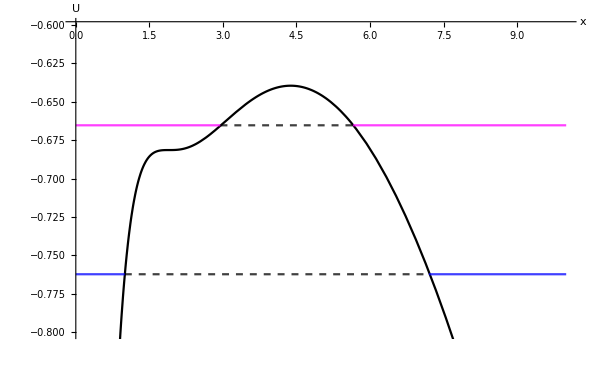

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc6ay=Show[Uc6ay,Energyc6ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.8,-0.6}]
```

### Final Plot

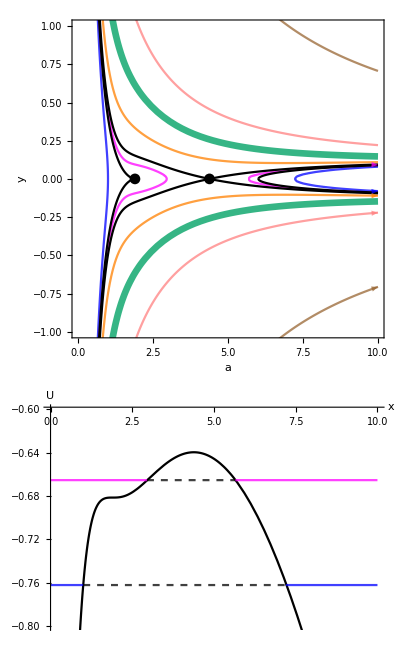

```mathematica
(*Plot the phase space and potential together*)
ayc6=GraphicsColumn[{PhaseSpacec6ay,Potentialc6ay},Spacings->{0,-20}]
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc7ay[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[7]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[7]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c7trajay[1]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[2]=ContourPlot[Evaluate[trajc7ay[0,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[3]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[4]=ContourPlot[Evaluate[trajc7ay[0.58,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[5]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,0,aOneEinsteinPointc7},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[6]=ContourPlot[Evaluate[trajc7ay[0.68,0.9]],{a,aOneEinsteinPointc7,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[7]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[8]=ContourPlot[Evaluate[trajc7ay[0.98,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[9]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[10]=ContourPlot[Evaluate[trajc7ay[2.35,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[11]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7trajay[12]=ContourPlot[Evaluate[trajc7ay[7.02,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
trajc7ay=Table[c7trajay[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
FFSc7ay=Plot[{FFSay[a,0.9][[7]],-FFSay[a,0.9][[7]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
CFSc7ay=Plot[{CFSay[a,aOneEinsteinPointc7,0.9][[7]],-CFSay[a,aOneEinsteinPointc7,0.9][[7]]},{a,0,10},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7ay=ListPlot[{{aOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundary between the accelerating and decelerating regions for this case*)
Accnc7ay=ContourPlot[Accnay[[7]]==0,{a,0,3},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

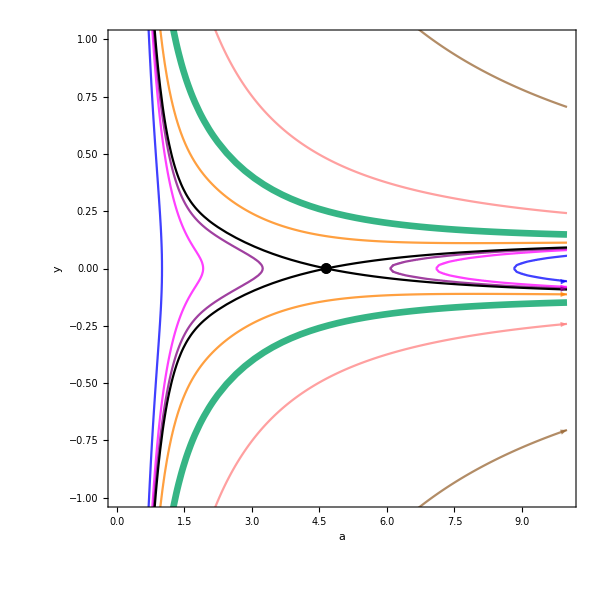

```mathematica
(*Show all components of the phase space*)
PhaseSpacec7ay=Show[trajc7ay,FFSc7ay,CFSc7ay,Einsteinc7ay,PlotRange->{-1,1},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc7ay=Plot[{Uay[a,0.9][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c7Energyay[1]=Plot[{Energyay[0.9,0][[7]]},{a,0,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[2]=Plot[{Energyay[0.9,0][[7]]},{a,8.8,10},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energyay[3]=Plot[{Energyay[0.9,0.58][[7]]},{a,0,1.95},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[4]=Plot[{Energyay[0.9,0.58][[7]]},{a,7.05,10},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energyay[5]=Plot[{Energyay[0.9,0.68][[7]]},{a,0,3.3},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[6]=Plot[{Energyay[0.9,0.68][[7]]},{a,6,10},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energyay[7]=Plot[{Energyay[0.9,0.98][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energyay[8]=Plot[{Energyay[0.9,2.35][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energyay[9]=Plot[{Energyay[0.9,7.02][[7]]},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Plot the energy of a trajectory that follows the FFS*)
c7Energyay[10]=Plot[{0},{a,0,10},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energyay[11]=Plot[{Energyay[0.9,0][[7]]},{a,1,8.8},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[12]=Plot[{Energyay[0.9,0.58][[7]]},{a,1.95,7.05},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energyay[13]=Plot[{Energyay[0.9,0.68][[7]]},{a,3.3,6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc7ay=Table[c7Energyay[i],{i,1,13}];
```

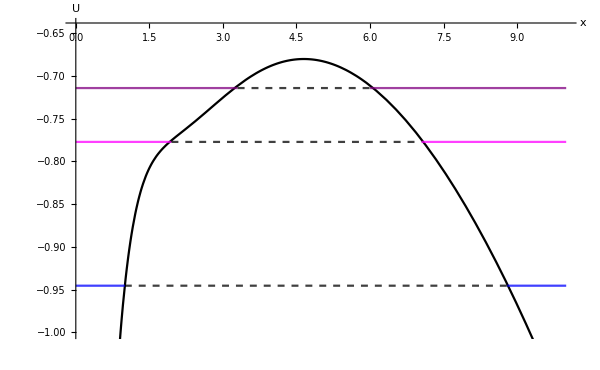

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc7ay=Show[Uc7ay,Energyc7ay,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-1,-0.64}]
```

### Final Plot

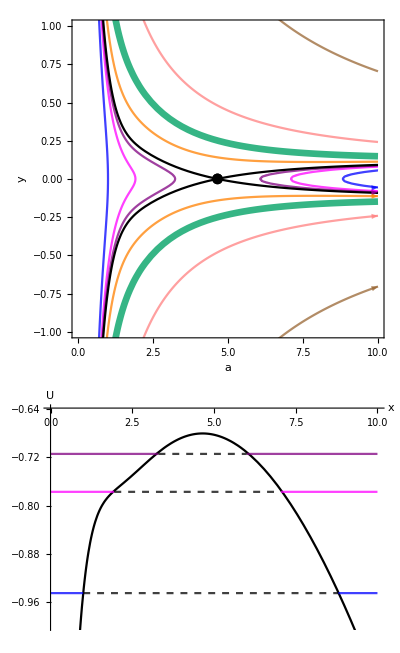

```mathematica
(*Plot the phase space and potential together*)
ayc7=GraphicsColumn[{PhaseSpacec7ay,Potentialc7ay},Spacings->{0,-20}]
```

## Constant Curvature Hypersurface: Dark Energy and Matter only

## Find the Limiting Cases

```mathematica
(*Clear the value of K*)
(*K = k/ρ* *)
Clear[K]
```

```mathematica
(*Define z0 using the Planck 2018 density parameters*)
z0ConstantK=(Ωm/ΩΛ)*(ℛ/α);
```

```mathematica
(*Define a(z) and a(Z)*)
caz=z0ConstantK;

aKz[z_]=(caz/z)^(1/3);
aKZ[Z_]=(caz*(1-Z)/Z)^(1/3);
```

```mathematica
(*Define x at the Einstein fixed point from the Friedmann equation*)
xE=3*K/(aKz[z]^2)-z;
```

```mathematica
(*Define the term left when y' = y = 0*)
fConstantK=z-3*ℛ+xE*(1+3*ℛ)-3*xE^2;
```

```mathematica
(*Find the first derivative of fConstantK with respect to z*)
DfConstantK=D[fConstantK,z]
```

1+1.15 (-1+15.7713 K (1/z)^(1/3))-6 (-1+15.7713 K (1/z)^(1/3)) ((23.6569 K)/(1/z)^(2/3)-z)

```mathematica
(*Solve DfConstantK = 0 for K*)
DfK=Solve[DfConstantK==0,K]
```

{{K→0.000223353 (-1. √(2238.6/(1/z)^(4/3)+7238.15/(1/z)^(1/3)+328.951 (1/z)^(2/3))+236.569/(1/z)^(2/3)+18.137 (1/z)^(1/3)) (1/z)^(1/3)},{K→0.000223353 (√(2238.6/(1/z)^(4/3)+7238.15/(1/z)^(1/3)+328.951 (1/z)^(2/3))+236.569/(1/z)^(2/3)+18.137 (1/z)^(1/3)) (1/z)^(1/3)}}

```mathematica
(*Separate the solutions into variable names*)
KSol1=K/.DfK[[1]];
KSol2=K/.DfK[[2]];
```

```mathematica
(*Substitute the K terms found from df/dz = 0 back into fConstantK*)
fConstantKi=fConstantK/.K->KSol1;
fConstantKii=fConstantK/.K->KSol2;
```

```mathematica
(*Solve for z when fConstantK = 0*)
(*The limiting cases exist when f = df/dz = 0*)
zLim1=z/.Solve[fConstantKi==0,z]
zLim2=z/.Solve[fConstantKii==0,z]
```

{0.302575}

{0.0488557,0.538361}

```mathematica
(*Find the corresponding K values in the limiting cases*)
KSolution1=KSol1/.z->zLim1
KSolution2=KSol2/.z->zLim2
```

{0.0185963}

{0.0934629,0.0726691}

```mathematica
(*ℛ < RangeOfValidity < 1 must be satisfied in order for ℛ < x < 1 to be satisfied*)
(*Therefore KSolution1[[1]] is not a solution in the range ℛ < x < 1*)
RangeOfValidity[K_,z_]=3*K/(aKz[z]^2)-z;

RangeOfValidity[KSolution1[[1]],zLim1[[1]]]

RangeOfValidity[KSolution2[[1]],zLim2[[1]]]

RangeOfValidity[KSolution2[[2]],zLim2[[2]]]
```

-0.104297

0.246633

0.59933

```mathematica
(*Redefine xE above in terms of the compact variable Z*)
xEZ[Z_,K_]=3*K/(aKZ[Z]^2)-Z/(1-Z);
```

```mathematica
(*Redefine a compactified fConstantK above in terms of the compactified variable Z*)
fConstantKCompact[Z_,K_]=(Z/(1-Z)-3*ℛ+xEZ[Z,K]*(1+3*ℛ)-3*xEZ[Z,K]^2)/(Sqrt[1+(Z/(1-Z)-3*ℛ+xEZ[Z,K]*(1+3*ℛ)-3*xEZ[Z,K]^2)^2]);
```

```mathematica
(*Plot a dashed line representing the maximum value of Z when x = 1 in fConstantKCompact[Z,K]*)
ZMax=ContourPlot[{Z==2/3},{Z,0,1},{y,-1,1},Axes->True,Frame->False,ContourStyle->{Black,Dashed}];
```

```mathematica
(*Plot the limiting cases as solid lines and the cases in between  as dashed lines*)
fPlots=Plot[{fConstantKCompact[Z,0.07],fConstantKCompact[Z,KSolution2[[2]]],fConstantKCompact[Z,0.075],fConstantKCompact[Z,0.082],fConstantKCompact[Z,KSolution2[[1]]],fConstantKCompact[Z,0.14]},{Z,0,1},PlotStyle->{{Gray,Dashed},Black,{Darker[Green],Dashed},{Blue,Dashed},Purple,{Magenta,Dashed}}];
```

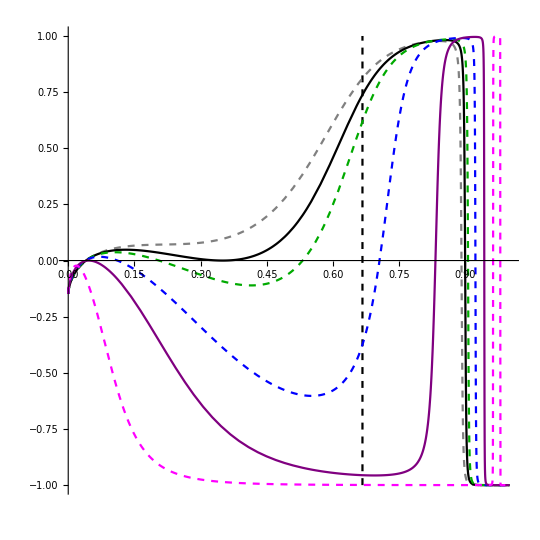

```mathematica
(*Show ZMax and fPlots on the same axes*)
(*At x = 1, Z = 2/3, which is shown by the black dashed line. For the 2/3 < Z < 1 region of the plot, x > 1 which is a region we do not consider*)
Show[ZMax,fPlots]
```

```mathematica
(*Define an array of K values*)
KValues={0.07,KSolution2[[2]],0.075,0.082,KSolution2[[1]],0.14}
```

{0.07,0.0726691,0.075,0.082,0.0934629,0.14}

## Calculate the Einstein Fixed Points

### One Einstein Point: K1

```mathematica
(*Numerically solve f(Z) = 0 using FindRoot to find the Z value of the Einstein fixed point*)
ZOneEinsteinPointK1=FindRoot[fConstantKCompact[Z,KValues[[1]]]==0,{Z,0.05}];
```

```mathematica
(*Remove the arrow from the solution above*)
ZOneEinsteinPointK1=Z/.ZOneEinsteinPointK1
```

0.0410655

```mathematica
(*Calculate the x value of the Einstein point*)
xOneEinsteinPointK1=xEZ[ZOneEinsteinPointK1,KValues[[1]]]
```

0.159874

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFPConstantK[1]={xOneEinsteinPointK1,0,ZOneEinsteinPointK1}
```

{0.159874,0,0.0410655}

### Two Einstein Points: K2 (1st Limiting Case)

```mathematica
(*Numerically solve f(Z) = 0 using FindRoot to find the Z values of the Einstein fixed points*)
ZTwoEinsteinPointsK2i=FindRoot[fConstantKCompact[Z,KValues[[2]]]==0,{Z,0.05}];
ZTwoEinsteinPointsK2ii=FindRoot[fConstantKCompact[Z,KValues[[2]]]==0,{Z,0.35}];
```

```mathematica
(*Put the Z values of the Einstein points into one variable name for this case*)
ZTwoEinsteinPointsK2={Z/.ZTwoEinsteinPointsK2i,Z/.ZTwoEinsteinPointsK2ii}
```

{0.0401795,0.349957}

```mathematica
(*Calculate the x values of the Einstein points*)
xTwoEinsteinPointsK2=xEZ[ZTwoEinsteinPointsK2,KValues[[2]]]
```

{0.1654,0.59933}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPConstantK[2]={xTwoEinsteinPointsK2[[1]],0,ZTwoEinsteinPointsK2[[1]]}
EinsteinFPConstantK[3]={xTwoEinsteinPointsK2[[2]],0,ZTwoEinsteinPointsK2[[2]]}
```

{0.1654,0,0.0401795}

{0.59933,0,0.349957}

### Three Einstein Points: K3

```mathematica
(*Numerically solve f(Z) = 0 using FindRoot to find the Z values of the Einstein fixed points*)
ZThreeEinsteinPointsK3i=FindRoot[fConstantKCompact[Z,KValues[[3]]]==0,{Z,0.05}];
ZThreeEinsteinPointsK3ii=FindRoot[fConstantKCompact[Z,KValues[[3]]]==0,{Z,0.2}];
ZThreeEinsteinPointsK3iii=FindRoot[fConstantKCompact[Z,KValues[[3]]]==0,{Z,0.55}];
```

```mathematica
(*Put the Z values of the Einstein points into one variable name for this case*)
ZThreeEinsteinPointsK3={Z/.ZThreeEinsteinPointsK3i,Z/.ZThreeEinsteinPointsK3ii,Z/.ZThreeEinsteinPointsK3iii}
```

{0.039529,0.205881,0.531129}

```mathematica
(*Calculate the x values of the Einstein points*)
xThreeEinsteinPointsK3=xEZ[ZThreeEinsteinPointsK3,KValues[[3]]]
```

{0.170343,0.462138,0.795265}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPConstantK[4]={xThreeEinsteinPointsK3[[1]],0,ZThreeEinsteinPointsK3[[1]]}
EinsteinFPConstantK[5]={xThreeEinsteinPointsK3[[2]],0,ZThreeEinsteinPointsK3[[2]]}
EinsteinFPConstantK[6]={xThreeEinsteinPointsK3[[3]],0,ZThreeEinsteinPointsK3[[3]]}
```

{0.170343,0,0.039529}

{0.462138,0,0.205881}

{0.795265,0,0.531129}

### Two Einstein Points: K4

```mathematica
(*Numerically solve f(Z) = 0 using FindRoot to find the Z values of the Einstein fixed points*)
ZTwoEinsteinPointsK4i=FindRoot[fConstantKCompact[Z,KValues[[4]]]==0,{Z,0.05}];
ZTwoEinsteinPointsK4ii=FindRoot[fConstantKCompact[Z,KValues[[4]]]==0,{Z,0.35}];
```

```mathematica
(*Put the Z values of the Einstein points into one variable name for this case*)
ZTwoEinsteinPointsK4={Z/.ZTwoEinsteinPointsK4i,Z/.ZTwoEinsteinPointsK4ii}
```

{0.0383421,0.111416}

```mathematica
(*Calculate the x values of the Einstein points*)
xTwoEinsteinPointsK4=xEZ[ZTwoEinsteinPointsK4,KValues[[2]]]
```

{0.160767,0.305281}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPConstantK[7]={xTwoEinsteinPointsK4[[1]],0,ZTwoEinsteinPointsK4[[1]]}
EinsteinFPConstantK[8]={xTwoEinsteinPointsK4[[2]],0,ZTwoEinsteinPointsK4[[2]]}
```

{0.160767,0,0.0383421}

{0.305281,0,0.111416}

### One Einstein Point: K5 (2nd Limiting Case)

```mathematica
(*Numerically solve f(Z) = 0 using FindRoot to find the Z value of the Einstein fixed point*)
ZOneEinsteinPointK5=FindRoot[fConstantKCompact[Z,KValues[[5]]]==0,{Z,0.05}];
```

```mathematica
(*Remove the arrow from the solution above*)
ZOneEinsteinPointK5=Z/.ZOneEinsteinPointK5
```

0.04658

```mathematica
(*Calculate the x value of the Einstein point*)
xOneEinsteinPointK5=xEZ[ZOneEinsteinPointK5,KValues[[5]]]
```

0.246633

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFPConstantK[9]={xOneEinsteinPointK5,0,ZOneEinsteinPointK5}
```

{0.246633,0,0.04658}

### Table of Einstein Fixed Points and their Eigenvalues/Eigenvectors

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the compact Hubble expansion, Y, and compact dark matter, Z*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-ℛ)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the 3D Jacobian matrix for the x-Y-Z system. D[] differentiates each expression*)
JConstantK=Simplify[{{D[de1,x],D[de1,Y],D[de1,Z]}, {D[de2,x],D[de2,Y],D[de2,Z]}, {D[de3,x],D[de3,Y],D[de3,Z]}}];
JConstantK//MatrixForm
```

(((-3.15+6. x) Y)/(√(1-Y^2)) | -(3. (0.05-1.05 x+x^2))/(√(1-Y^2) (-1.+Y^2)) | 0
1/6 (-1.15+6 x) (1-Y^2)^(3/2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-0.15+1.15 x-3 x^2+Z/(1-Z))))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2)
0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 Z))/(√(1-Y^2)))

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPsConstantK=Table[EinsteinFPConstantK[i],{i,1,9}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
TableForm[Table[{EinsteinFPsConstantK[[i]]//MatrixForm,Simplify[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],Z->EinsteinFPsConstantK[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],Z->EinsteinFPsConstantK[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],Z->EinsteinFPsConstantK[[i,3]]}]]//MatrixForm},{i,1,9}],TableHeadings->{{"K1","K2","","K3","","","K4","","K5"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues | 
K1 | (0.159874
0
0.0410655) | (0. | -0.276923 | 0
-0.0317931 | 0. | -0.181247
0 | -0.118137 | 0.) | (-0.173828
0.173828
7.84687×10^-18) | (0.796562 | 0.500012 | 0.339819
0.796562 | -0.500012 | 0.339819
-0.984961 | -5.66868×10^-17 | 0.172775)
K2 | (0.1654
0
0.0401795) | (0. | -0.288938 | 0
-0.0262667 | 0. | -0.180913
0 | -0.115695 | 0.) | (-0.168879
0.168879
3.10857×10^-17) | (0.815966 | 0.476917 | 0.326725
0.815966 | -0.476917 | 0.326725
-0.989624 | 3.49404×10^-17 | 0.143684)
 | (0.59933
0
0.349957) | (0. | -0.6603 | 0
0.407664 | 0. | -0.394426
0 | -0.682462 | 0.) | (0.000110501
-0.0001105
-1.83716×10^-9) | (0.695342 | -0.000116366 | 0.718679
-0.695342 | -0.000116364 | -0.718679
0.695342 | 1.93466×10^-9 | 0.718679)
K3 | (0.170343
0
0.039529) | (0. | -0.29953 | 0
-0.0213239 | 0. | -0.180668
0 | -0.113899 | 0.) | (-0.16421
0.16421
-3.56636×10^-18) | (0.831847 | 0.456041 | 0.316318
0.831847 | -0.456041 | 0.316318
-0.993107 | 1.41811×10^-17 | 0.117215)
 | (0.462138
0
0.205881) | (0. | -0.66502 | 0
0.270472 | 0. | -0.264288
0 | -0.490481 | 0.) | (-2.29413×10^-16+0.224145 ⅈ
-2.29413×10^-16-0.224145 ⅈ
4.61067×10^-16+0. ⅈ) | (0.776719+0. ⅈ | -5.89206×10^-17-0.261793 ⅈ | 0.572864-3.32269×10^-16 ⅈ
0.776719+0. ⅈ | -5.89206×10^-17+0.261793 ⅈ | 0.572864+3.32269×10^-16 ⅈ
0.698883+0. ⅈ | -8.44989×10^-16+0. ⅈ | 0.715236+0. ⅈ)
 | (0.795265
0
0.531129) | (0. | -0.457746 | 0
0.603598 | 0. | -0.758128
0 | -0.747093 | 0.) | (0.538607
-0.538607
-2.72269×10^-16) | (0.445069 | -0.523691 | 0.726403
0.445069 | 0.523691 | 0.726403
-0.782329 | -2.78982×10^-16 | -0.622866)
K4 | (0.160767
0
0.0383421) | (0. | -0.278878 | 0
-0.0308999 | 0. | -0.180222
0 | -0.110616 | 0.) | (-0.168975
0.168975
6.77475×10^-18) | (0.80992 | 0.490741 | 0.321252
0.80992 | -0.490741 | 0.321252
-0.985618 | 2.6196×10^-17 | 0.168989)
 | (0.305281
0
0.111416) | (0. | -0.532045 | 0
0.113614 | 0. | -0.211082
0 | -0.297007 | 0.) | (0.0473828
-0.0473828
-1.57964×10^-16) | (0.870534 | -0.0775278 | 0.485964
0.870534 | 0.0775278 | 0.485964
-0.880551 | -2.29277×10^-16 | -0.473952)
K5 | (0.246633
0
0.04658) | (0. | -0.444411 | 0
0.0549668 | 0. | -0.18335
0 | -0.133231 | 0.) | (-5.33861×10^-11+0.0000875876 ⅈ
-5.33861×10^-11-0.0000875876 ⅈ
1.06772×10^-10+0. ⅈ) | (-0.957881+0. ⅈ | -1.15068×10^-10+0.000188786 ⅈ | -0.287165+1.09938×10^-13 ⅈ
-0.957881+0. ⅈ | -1.15068×10^-10-0.000188786 ⅈ | -0.287165-1.09938×10^-13 ⅈ
0.957881+0. ⅈ | -2.30136×10^-10+0. ⅈ | 0.287165+0. ⅈ)

## Set-up for the Phase Spaces

```mathematica
(*Define the first integral of z(x), c, for the constant curvature case*)
cConstantK[x0_]=z0ConstantK*((1-x0)/(x0-ℛ))^(1/(1-ℛ));
```

```mathematica
(*Plot the surface where acceleration is zero*)
AccnxYz=ContourPlot3D[Z/(1-Z)+x-3*ℛ+3*ℛ*x-3*x^2==0,{x,ℛ,1},{Y,-1,1},{Z,0,1}, ContourStyle->{Red,Opacity[0.1], Thick},Mesh->None,PlotPoints->10,PlotRange->Full];
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
ffsConstantK[x_,Z_]=x/3+Z/(3*(1-Z));
```

```mathematica
(*Rearrange the FFS for Y*)
(*Note that when plotting the FFS, +FFSSubMan and -FFSSubMan needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSConstantK[x_,Z_]=ffsConstantK[x,Z]/Sqrt[(1+ffsConstantK[x,Z]^2)];
```

```mathematica
(*Plot the FFS*)
ConstantKFFS=ParametricPlot3D[{{x,FFSConstantK[x,Z],Z},{x,-FFSConstantK[x,Z],Z}},{x,ℛ,1},{Z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.3]}},PlotPoints->100,PlotRange->All,Mesh->None];
```

```mathematica
(*Define the format of phase spaces*)
PhaseSpaceFormatxY={FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}};
```

```mathematica
PhaseSpaceFormatxYZ={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["Z",FontSize->20]},PlotRange->{{ℛ,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

## Case 1: 1 Einstein Fixed Point

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[1]]
```

0.07

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK1[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK1[x0_]=Sqrt[trajConstantK1[x0]/(1+trajConstantK1[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK1[1]=ParametricPlot3D[{x,trajConstantK1[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[2]=ParametricPlot3D[{x,-trajConstantK1[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[3]=ParametricPlot3D[{x,trajConstantK1[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[4]=ParametricPlot3D[{x,-trajConstantK1[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[5]=ParametricPlot3D[{x,trajConstantK1[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[6]=ParametricPlot3D[{x,-trajConstantK1[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[7]=ParametricPlot3D[{x,trajConstantK1[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[8]=ParametricPlot3D[{x,-trajConstantK1[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK1Plots=Table[trajConstantK1[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK1Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK1Surface=Sqrt[yK1Surface/(1+yK1Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK1Surface=ParametricPlot3D[{{x,YK1Surface,Z},{x,-YK1Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK1=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK1=Show[trajConstantK1Plots,ConstantK1Surface,AccnxYz,EinsteinPointsK1,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK1Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK1Proj[1]=ContourPlot[Evaluate[trajConstantK1Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK1Proj[2]=ContourPlot[Evaluate[trajConstantK1Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK1Proj[3]=ContourPlot[Evaluate[trajConstantK1Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK1Proj[4]=ContourPlot[Evaluate[trajConstantK1Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK1ProjectionPlots=Table[trajConstantK1Proj[i],{i,1,4}];
```

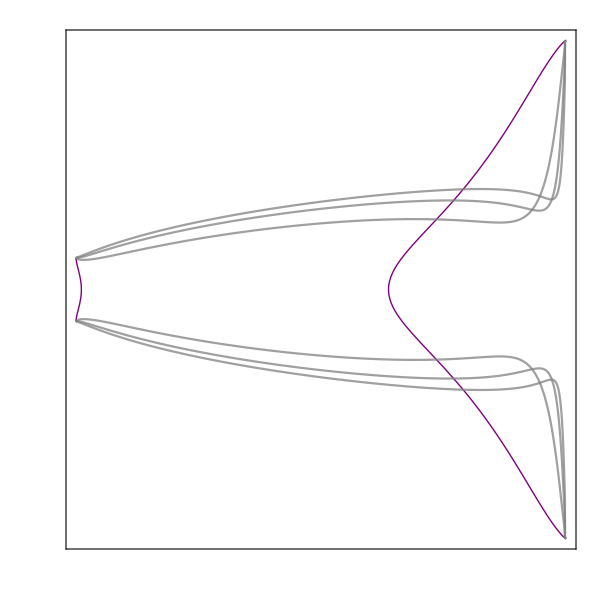

```mathematica
(*Show the trajectories*)
Show[trajConstantK1ProjectionPlots,PhaseSpaceFormatxY]
```

## Limiting Case 2: 2 Einstein Fixed Point

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[2]]
```

0.0726691

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK2[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK2[x0_]=Sqrt[trajConstantK2[x0]/(1+trajConstantK2[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK2[1]=ParametricPlot3D[{x,trajConstantK2[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[2]=ParametricPlot3D[{x,-trajConstantK2[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[3]=ParametricPlot3D[{x,trajConstantK2[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[4]=ParametricPlot3D[{x,-trajConstantK2[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[5]=ParametricPlot3D[{x,trajConstantK2[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[6]=ParametricPlot3D[{x,-trajConstantK2[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[7]=ParametricPlot3D[{x,trajConstantK2[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[8]=ParametricPlot3D[{x,-trajConstantK2[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK2Plots=Table[trajConstantK2[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK2Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK2Surface=Sqrt[yK2Surface/(1+yK2Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK2Surface=ParametricPlot3D[{{x,YK2Surface,Z},{x,-YK2Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK2=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK2=Show[trajConstantK2Plots,ConstantK2Surface,AccnxYz,EinsteinPointsK2,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK2Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK2Proj[1]=ContourPlot[Evaluate[trajConstantK2Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK2Proj[2]=ContourPlot[Evaluate[trajConstantK2Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK2Proj[3]=ContourPlot[Evaluate[trajConstantK2Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK2Proj[4]=ContourPlot[Evaluate[trajConstantK2Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK2ProjectionPlots=Table[trajConstantK2Proj[i],{i,1,4}];
```

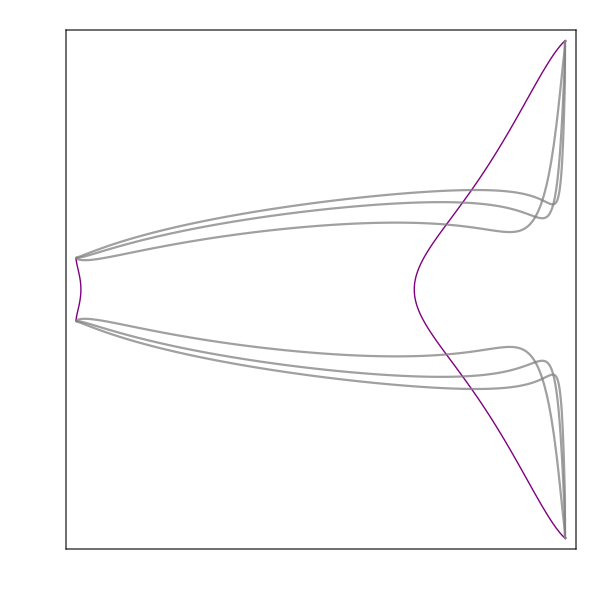

```mathematica
(*Show the trajectories*)
Show[trajConstantK2ProjectionPlots,PhaseSpaceFormatxY]
```

## Case 3: 3 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[3]]
```

0.075

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK3[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK3[x0_]=Sqrt[trajConstantK3[x0]/(1+trajConstantK3[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK3[1]=ParametricPlot3D[{x,trajConstantK3[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[2]=ParametricPlot3D[{x,-trajConstantK3[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[3]=ParametricPlot3D[{x,trajConstantK3[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[4]=ParametricPlot3D[{x,-trajConstantK3[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[5]=ParametricPlot3D[{x,trajConstantK3[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[6]=ParametricPlot3D[{x,-trajConstantK3[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[7]=ParametricPlot3D[{x,trajConstantK3[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[8]=ParametricPlot3D[{x,-trajConstantK3[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK3Plots=Table[trajConstantK3[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK3Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK3Surface=Sqrt[yK3Surface/(1+yK3Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK3Surface=ParametricPlot3D[{{x,YK3Surface,Z},{x,-YK3Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK3=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK3=Show[trajConstantK3Plots,ConstantK3Surface,AccnxYz,EinsteinPointsK3,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK3Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK3Proj[1]=ContourPlot[Evaluate[trajConstantK3Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK3Proj[2]=ContourPlot[Evaluate[trajConstantK3Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK3Proj[3]=ContourPlot[Evaluate[trajConstantK3Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK3Proj[4]=ContourPlot[Evaluate[trajConstantK3Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK3ProjectionPlots=Table[trajConstantK3Proj[i],{i,1,4}];
```

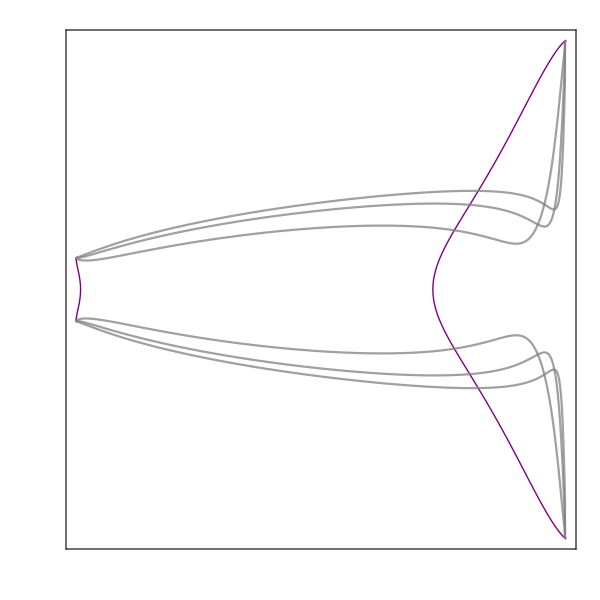

```mathematica
(*Show the trajectories*)
Show[trajConstantK3ProjectionPlots,PhaseSpaceFormatxY]
```

## Case 4: 2 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[4]]
```

0.082

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK4[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK4[x0_]=Sqrt[trajConstantK4[x0]/(1+trajConstantK4[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK4[1]=ParametricPlot3D[{x,trajConstantK4[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[2]=ParametricPlot3D[{x,-trajConstantK4[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[3]=ParametricPlot3D[{x,trajConstantK4[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[4]=ParametricPlot3D[{x,-trajConstantK4[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[5]=ParametricPlot3D[{x,trajConstantK4[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[6]=ParametricPlot3D[{x,-trajConstantK4[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[7]=ParametricPlot3D[{x,trajConstantK4[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[8]=ParametricPlot3D[{x,-trajConstantK4[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK4Plots=Table[trajConstantK4[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK4Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK4Surface=Sqrt[yK4Surface/(1+yK4Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK4Surface=ParametricPlot3D[{{x,YK4Surface,Z},{x,-YK4Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK4=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK4=Show[trajConstantK4Plots,ConstantK4Surface,AccnxYz,EinsteinPointsK4,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK4Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK4Proj[1]=ContourPlot[Evaluate[trajConstantK4Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK4Proj[2]=ContourPlot[Evaluate[trajConstantK4Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK4Proj[3]=ContourPlot[Evaluate[trajConstantK4Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK4Proj[4]=ContourPlot[Evaluate[trajConstantK4Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK4ProjectionPlots=Table[trajConstantK4Proj[i],{i,1,4}];
```

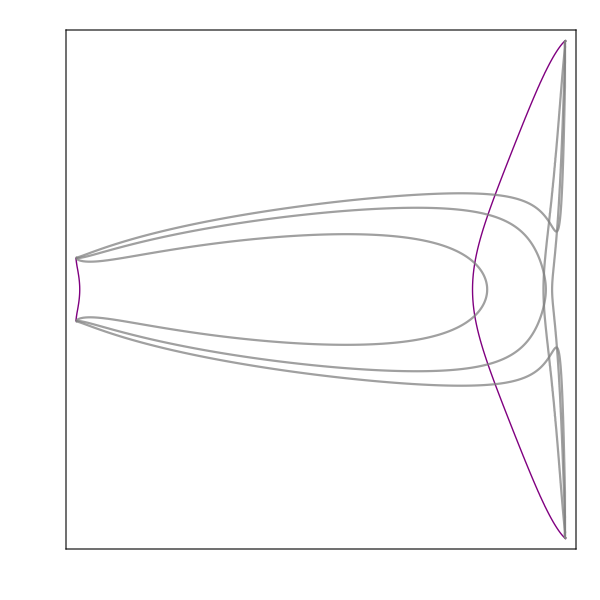

```mathematica
(*Show the trajectories*)
Show[trajConstantK4ProjectionPlots,PhaseSpaceFormatxY]
```

## Limiting Case 5: 1 Einstein Fixed Point

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[5]]
```

0.0934629

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK5[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK5[x0_]=Sqrt[trajConstantK5[x0]/(1+trajConstantK5[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK5[1]=ParametricPlot3D[{x,trajConstantK5[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[2]=ParametricPlot3D[{x,-trajConstantK5[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[3]=ParametricPlot3D[{x,trajConstantK5[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[4]=ParametricPlot3D[{x,-trajConstantK5[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[5]=ParametricPlot3D[{x,trajConstantK5[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[6]=ParametricPlot3D[{x,-trajConstantK5[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[7]=ParametricPlot3D[{x,trajConstantK5[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[8]=ParametricPlot3D[{x,-trajConstantK5[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK5Plots=Table[trajConstantK5[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK5Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK5Surface=Sqrt[yK5Surface/(1+yK5Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK5Surface=ParametricPlot3D[{{x,YK5Surface,Z},{x,-YK5Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK5=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK5=Show[trajConstantK5Plots,ConstantK5Surface,AccnxYz,EinsteinPointsK5,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK5Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK5Proj[1]=ContourPlot[Evaluate[trajConstantK5Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK5Proj[2]=ContourPlot[Evaluate[trajConstantK5Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK5Proj[3]=ContourPlot[Evaluate[trajConstantK5Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK5Proj[4]=ContourPlot[Evaluate[trajConstantK5Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK5ProjectionPlots=Table[trajConstantK5Proj[i],{i,1,4}];
```

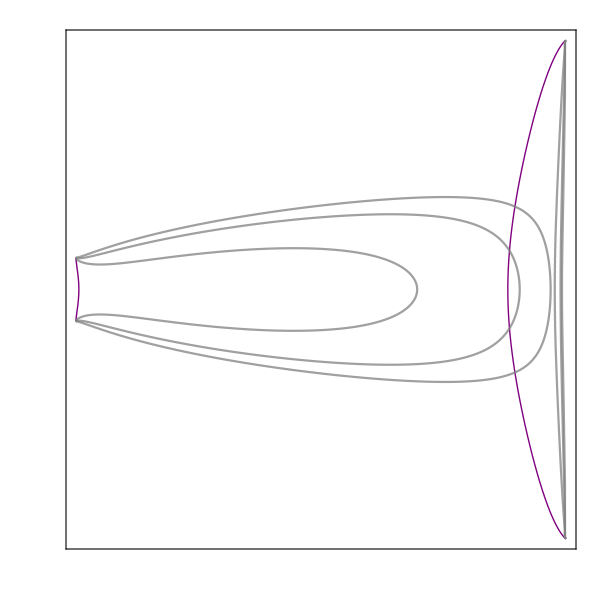

```mathematica
(*Show the trajectories*)
Show[trajConstantK5ProjectionPlots,PhaseSpaceFormatxY]
```

## Case 6: 0 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[6]]
```

0.14

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK6[x0]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK6[x0_]=Sqrt[trajConstantK6[x0]/(1+trajConstantK6[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK6[1]=ParametricPlot3D[{x,trajConstantK6[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[2]=ParametricPlot3D[{x,-trajConstantK6[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[3]=ParametricPlot3D[{x,trajConstantK6[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[4]=ParametricPlot3D[{x,-trajConstantK6[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[5]=ParametricPlot3D[{x,trajConstantK6[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[6]=ParametricPlot3D[{x,-trajConstantK6[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[7]=ParametricPlot3D[{x,trajConstantK6[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[8]=ParametricPlot3D[{x,-trajConstantK6[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK6Plots=Table[trajConstantK6[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK6Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK6Surface=Sqrt[yK6Surface/(1+yK6Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK6Surface=ParametricPlot3D[{{x,YK6Surface,Z},{x,-YK6Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->800,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK6=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK6=Show[trajConstantK6Plots,ConstantK6Surface,AccnxYz,EinsteinPointsK6,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK6Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK6Proj[1]=ContourPlot[Evaluate[trajConstantK6Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK6Proj[2]=ContourPlot[Evaluate[trajConstantK6Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK6Proj[3]=ContourPlot[Evaluate[trajConstantK6Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK6Proj[4]=ContourPlot[Evaluate[trajConstantK6Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK6ProjectionPlots=Table[trajConstantK6Proj[i],{i,1,4}];
```

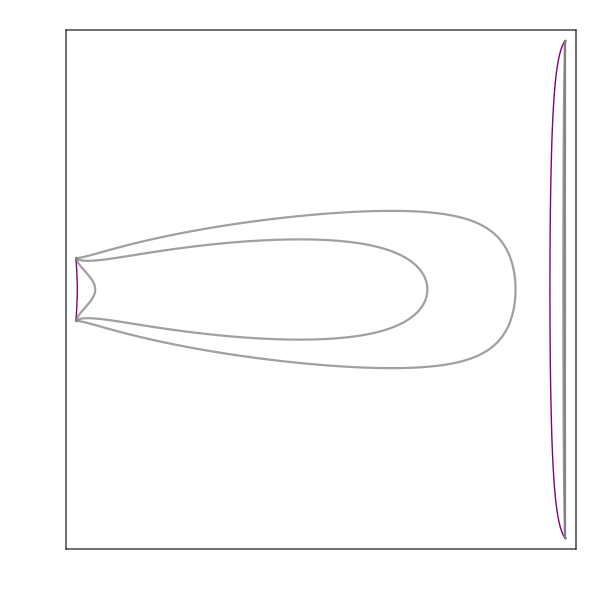

```mathematica
(*Show the trajectories*)
Show[trajConstantK6ProjectionPlots,PhaseSpaceFormatxY]
```

## Open Models

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=-0.2
```

-0.2

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK7[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK7[x0_]=Sqrt[trajConstantK7[x0]/(1+trajConstantK7[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK7[1]=ParametricPlot3D[{x,trajConstantK7[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[2]=ParametricPlot3D[{x,-trajConstantK7[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[3]=ParametricPlot3D[{x,trajConstantK7[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[4]=ParametricPlot3D[{x,-trajConstantK7[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[5]=ParametricPlot3D[{x,trajConstantK7[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[6]=ParametricPlot3D[{x,-trajConstantK7[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[7]=ParametricPlot3D[{x,trajConstantK7[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[8]=ParametricPlot3D[{x,-trajConstantK7[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK7Plots=Table[trajConstantK7[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK7Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK7Surface=Sqrt[yK7Surface/(1+yK7Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK7Surface=ParametricPlot3D[{{x,YK7Surface,Z},{x,-YK7Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK7=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK7=Show[trajConstantK7Plots,ConstantK7Surface,AccnxYz,EinsteinPointsK7,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK7Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK7Proj[1]=ContourPlot[Evaluate[trajConstantK7Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK7Proj[2]=ContourPlot[Evaluate[trajConstantK7Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK7Proj[3]=ContourPlot[Evaluate[trajConstantK7Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK7Proj[4]=ContourPlot[Evaluate[trajConstantK7Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK7ProjectionPlots=Table[trajConstantK7Proj[i],{i,1,4}];
```

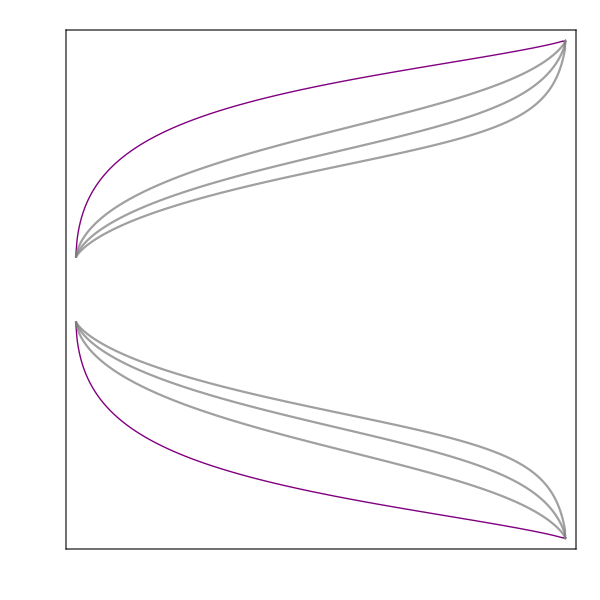

```mathematica
(*Show the trajectories*)
Show[trajConstantK7ProjectionPlots,PhaseSpaceFormatxY]
```

## Flat Models

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=0;
```

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK8[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK8[x0_]=Sqrt[trajConstantK8[x0]/(1+trajConstantK8[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK8[1]=ParametricPlot3D[{x,trajConstantK8[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[2]=ParametricPlot3D[{x,-trajConstantK8[0.1],Z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[3]=ParametricPlot3D[{x,trajConstantK8[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[4]=ParametricPlot3D[{x,-trajConstantK8[0.3],Z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[5]=ParametricPlot3D[{x,trajConstantK8[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[6]=ParametricPlot3D[{x,-trajConstantK8[0.5],Z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[7]=ParametricPlot3D[{x,trajConstantK8[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK8[8]=ParametricPlot3D[{x,-trajConstantK8[0.7],Z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK8Plots=Table[trajConstantK8[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK8Surface=x/3+Z/(3*(1-Z))-K/(aKZ[Z]^2);
YK8Surface=Sqrt[yK8Surface/(1+yK8Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK8Surface=ParametricPlot3D[{{x,YK8Surface,Z},{x,-YK8Surface,Z}},{x,ℛ,1},{Z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK8=ParametricPlot3D[{3*K/(aKZ[Z]^2)-Z/(1-Z),0,Z},{Z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK8=Show[trajConstantK8Plots,ConstantK8Surface,AccnxYz,EinsteinPointsK8,PhaseSpaceFormatxYZ]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK8Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK8Proj[1]=ContourPlot[Evaluate[trajConstantK8Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK8Proj[2]=ContourPlot[Evaluate[trajConstantK8Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK8Proj[3]=ContourPlot[Evaluate[trajConstantK8Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK8Proj[4]=ContourPlot[Evaluate[trajConstantK8Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK8ProjectionPlots=Table[trajConstantK8Proj[i],{i,1,4}];
```

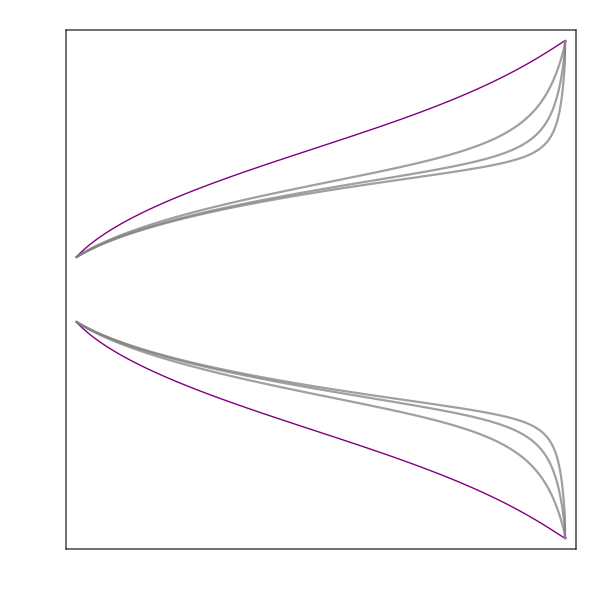

```mathematica
(*Show the trajectories*)
Show[trajConstantK8ProjectionPlots,PhaseSpaceFormatxY]
```

# Add Upper Limits to Matter and Radiation

## Non-compactified y variable

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Load MaTeX to typeset axis labels using LaTeX*)
<<MaTeX`
```

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the Hubble expansion, y, dark matter, z, and  radiation, r*)
de1:=x'=-3*y*(x-ℛ)*(1-x)
de2:=y'=-y^2-(1/6)*(z*(1-3z)+2*r*(1-2r)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*y*z*(1-z)
de4:=r'=-4*y*r*(1-r)
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,y,z,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→0,r→1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))},{y→0,r→1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))},{x→1,y→-1/(√3),z→0,r→0},{x→1,y→1/(√3),z→0,r→0},{x→1,y→-√(2/3),z→0,r→1},{x→1,y→√(2/3),z→0,r→1},{x→1,y→-√(2/3),z→1,r→0},{x→1,y→√(2/3),z→1,r→0},{x→1,y→-1,z→1,r→1},{x→1,y→1,z→1,r→1},{x→ℛ,y→-(√ℛ)/(√3),z→0,r→0},{x→ℛ,y→(√ℛ)/(√3),z→0,r→0},{x→ℛ,y→-(√(1+ℛ))/(√3),z→0,r→1},{x→ℛ,y→(√(1+ℛ))/(√3),z→0,r→1},{x→ℛ,y→-(√(1+ℛ))/(√3),z→1,r→0},{x→ℛ,y→(√(1+ℛ))/(√3),z→1,r→0},{x→ℛ,y→-(√(2+ℛ))/(√3),z→1,r→1},{x→ℛ,y→(√(2+ℛ))/(√3),z→1,r→1}}

## Compactified Y variable

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the compactified Hubble expansion variable, Y, dark matter, z, and  radiation, r*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/(1-Y^2)^(1/2)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(z*(1-3z)+2*r*(1-2r)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*Y*z*(1-z)/((1-Y^2)^(1/2))
de4:=r'=-4*Y*r*(1-r)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,z,r}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,r→1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))},{Y→0,r→1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))},{x→1,Y→0,r→1/4 (1-√(-7+4 z-12 z^2))},{x→1,Y→0,r→1/4 (1+√(-7+4 z-12 z^2))},{x→ℛ,Y→0,r→1/4 (1-√(1+4 z-12 z^2-8 ℛ))},{x→ℛ,Y→0,r→1/4 (1+√(1+4 z-12 z^2-8 ℛ))},{Y→0,z→1,r→1/4 (1-√(-7+4 x-12 x^2-12 ℛ+12 x ℛ))},{Y→0,z→1,r→1/4 (1+√(-7+4 x-12 x^2-12 ℛ+12 x ℛ))},{Y→0,z→0,r→1/4 (1-√(1+4 x-12 x^2-12 ℛ+12 x ℛ))},{Y→0,z→0,r→1/4 (1+√(1+4 x-12 x^2-12 ℛ+12 x ℛ))},{Y→0,z→1/6 (1-√(-23+12 x-36 x^2-36 ℛ+36 x ℛ)),r→1},{Y→0,z→1/6 (1+√(-23+12 x-36 x^2-36 ℛ+36 x ℛ)),r→1},{Y→0,z→1/6 (1-√(1+12 x-36 x^2-36 ℛ+36 x ℛ)),r→0},{Y→0,z→1/6 (1+√(1+12 x-36 x^2-36 ℛ+36 x ℛ)),r→0},{x→1,Y→-1/2,z→0,r→0},{x→1,Y→1/2,z→0,r→0},{x→ℛ,Y→-(√ℛ)/(√(3+ℛ)),z→0,r→0},{x→ℛ,Y→(√ℛ)/(√(3+ℛ)),z→0,r→0},{x→1/6 (1+3 ℛ-√(1-30 ℛ+9 ℛ^2)),Y→0,z→0,r→0},{x→1/6 (1+3 ℛ+√(1-30 ℛ+9 ℛ^2)),Y→0,z→0,r→0},{x→1,Y→-√(2/5),z→1,r→0},{x→1,Y→√(2/5),z→1,r→0},{x→ℛ,Y→-(√(1+ℛ))/(√(4+ℛ)),z→1,r→0},{x→ℛ,Y→(√(1+ℛ))/(√(4+ℛ)),z→1,r→0},{x→1/6 (1+3 ℛ-√(-23-30 ℛ+9 ℛ^2)),Y→0,z→1,r→0},{x→1/6 (1+3 ℛ+√(-23-30 ℛ+9 ℛ^2)),Y→0,z→1,r→0},{x→1,Y→-√(2/5),z→0,r→1},{x→1,Y→√(2/5),z→0,r→1},{x→ℛ,Y→-(√(1+ℛ))/(√(4+ℛ)),z→0,r→1},{x→ℛ,Y→(√(1+ℛ))/(√(4+ℛ)),z→0,r→1},{x→1/6 (1+3 ℛ-√(-23-30 ℛ+9 ℛ^2)),Y→0,z→0,r→1},{x→1/6 (1+3 ℛ+√(-23-30 ℛ+9 ℛ^2)),Y→0,z→0,r→1},{x→1,Y→-1/(√2),z→1,r→1},{x→1,Y→1/(√2),z→1,r→1},{x→ℛ,Y→-(√(2+ℛ))/(√(5+ℛ)),z→1,r→1},{x→ℛ,Y→(√(2+ℛ))/(√(5+ℛ)),z→1,r→1},{x→1/6 (1+3 ℛ-√(-47-30 ℛ+9 ℛ^2)),Y→0,z→1,r→1},{x→1/6 (1+3 ℛ+√(-47-30 ℛ+9 ℛ^2)),Y→0,z→1,r→1},{x→1,Y→0,z→0,r→1/4 (1-ⅈ √7)},{x→1,Y→0,z→0,r→1/4 (1+ⅈ √7)},{x→1,Y→0,z→1,r→1/4 (1-ⅈ √15)},{x→1,Y→0,z→1,r→1/4 (1+ⅈ √15)},{x→ℛ,Y→0,z→1,r→1/4 (1-√(-7-8 ℛ))},{x→ℛ,Y→0,z→1,r→1/4 (1+√(-7-8 ℛ))},{x→ℛ,Y→0,z→0,r→1/4 (1-√(1-8 ℛ))},{x→ℛ,Y→0,z→0,r→1/4 (1+√(1-8 ℛ))},{x→1,Y→0,z→1/6 (1-ⅈ √23),r→0},{x→1,Y→0,z→1/6 (1+ⅈ √23),r→0},{x→1,Y→0,z→1/6 (1-ⅈ √47),r→1},{x→1,Y→0,z→1/6 (1+ⅈ √47),r→1},{x→ℛ,Y→0,z→1/6 (1-√(-23-24 ℛ)),r→1},{x→ℛ,Y→0,z→1/6 (1+√(-23-24 ℛ)),r→1},{x→ℛ,Y→0,z→1/6 (1-√(1-24 ℛ)),r→0},{x→ℛ,Y→0,z→1/6 (1+√(1-24 ℛ)),r→0}}

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,Y/.FPs[[1,1]],z,r/.FPs[[1,2]]};
FP[2]={x,Y/.FPs[[2,1]],z,r/.FPs[[2,2]]};
FP[3]={x/.FPs[[15,1]],Y/.FPs[[15,2]],z/.FPs[[15,3]],r/.FPs[[15,4]]};
FP[4]={x/.FPs[[16,1]],Y/.FPs[[16,2]],z/.FPs[[16,3]],r/.FPs[[16,4]]};
FP[5]={x/.FPs[[17,1]],Y/.FPs[[17,2]],z/.FPs[[17,3]],r/.FPs[[17,4]]};
FP[6]={x/.FPs[[18,1]],Y/.FPs[[18,2]],z/.FPs[[18,3]],r/.FPs[[18,4]]};
FP[7]={x/.FPs[[21,1]],Y/.FPs[[21,2]],z/.FPs[[21,3]],r/.FPs[[21,4]]};
FP[8]={x/.FPs[[22,1]],Y/.FPs[[22,2]],z/.FPs[[22,3]],r/.FPs[[22,4]]};
FP[9]={x/.FPs[[23,1]],Y/.FPs[[23,2]],z/.FPs[[23,3]],r/.FPs[[23,4]]};
FP[10]={x/.FPs[[24,1]],Y/.FPs[[24,2]],z/.FPs[[24,3]],r/.FPs[[24,4]]};
FP[11]={x/.FPs[[27,1]],Y/.FPs[[27,2]],z/.FPs[[27,3]],r/.FPs[[27,4]]};
FP[12]={x/.FPs[[28,1]],Y/.FPs[[28,2]],z/.FPs[[28,3]],r/.FPs[[28,4]]};
FP[13]={x/.FPs[[29,1]],Y/.FPs[[29,2]],z/.FPs[[29,3]],r/.FPs[[29,4]]};
FP[14]={x/.FPs[[30,1]],Y/.FPs[[30,2]],z/.FPs[[30,3]],r/.FPs[[30,4]]};
FP[15]={x/.FPs[[33,1]],Y/.FPs[[33,2]],z/.FPs[[33,3]],r/.FPs[[33,4]]};
FP[16]={x/.FPs[[34,1]],Y/.FPs[[34,2]],z/.FPs[[34,3]],r/.FPs[[34,4]]};
FP[17]={x/.FPs[[35,1]],Y/.FPs[[35,2]],z/.FPs[[35,3]],r/.FPs[[35,4]]};
FP[18]={x/.FPs[[36,1]],Y/.FPs[[36,2]],z/.FPs[[36,3]],r/.FPs[[36,4]]};
```

```mathematica
(*Add the fixed points into a table*)
FPs=Table[FP[i],{i,1,18}];
```

```mathematica
(*Find the 4D Jacobian matrix for the general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,Y],D[de1,z],D[de1,r]}, {D[de2,x],D[de2,Y],D[de2,z],D[de2,r]},{D[de3,x],D[de3,Y],D[de3,z],D[de3,r]},{D[de4,x],D[de4,Y],D[de4,z],D[de4,r]}}];
J//MatrixForm
```

((3 Y (-1+2 x-ℛ))/(√(1-Y^2)) | (3 (-1+x) (x-ℛ))/((1-Y^2)^(3/2)) | 0 | 0
-1/6 (1-Y^2)^(3/2) (1-6 x+3 ℛ) | (Y (2 Y^2+4 (-1+Y^2)+(-1+Y^2) (-2 r+4 r^2+3 x^2-z+3 z^2+3 ℛ-x (1+3 ℛ))))/(2 √(1-Y^2)) | 1/6 (1-Y^2)^(3/2) (-1+6 z) | 1/3 (-1+4 r) (1-Y^2)^(3/2)
0 | (3 (-1+z) z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 z))/(√(1-Y^2)) | 0
0 | (4 (-1+r) r)/((1-Y^2)^(3/2)) | 0 | (4 (-1+2 r) Y)/(√(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
FPTable=Table[{FPs[[i]]//MatrixForm,J/.{x->FPs[[i,1]],Y->FPs[[i,2]],z->FPs[[i,3]],r->FPs[[i,4]]}//MatrixForm,FullSimplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],z->FPs[[i,3]],r->FPs[[i,4]]}]]//MatrixForm},{i,1,18}];
```

```mathematica
(*Display the table with headings*)
FPTableUpperBound=TableForm[FPTable,TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Fixed Point | Jacobian | Eigenvalues
(x
0
z
1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
1/6 (-1+6 x-3 ℛ) | 0 | 1/6 (-1+6 z) | -1/3 √(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ)
0 | 3 (-1+z) z | 0 | 0
0 | (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ)) (-1+1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))) | 0 | 0) | (0
0
-(√(-1+18 x^3+z (-1+9 z (-1+2 z))+9 ℛ-9 ℛ^2+√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+2 z (-1+3 z) √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+6 ℛ √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+3 x^2 (-3-9 ℛ+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ)))+x (-1-2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+3 ℛ (6+3 ℛ-2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))))))/(√6)
(√(-1+18 x^3+z (-1+9 z (-1+2 z))+9 ℛ-9 ℛ^2+√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+2 z (-1+3 z) √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+6 ℛ √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+3 x^2 (-3-9 ℛ+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ)))+x (-1-2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+3 ℛ (6+3 ℛ-2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))))))/(√6))
(x
0
z
1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))) | (0 | 3 (-1+x) (x-ℛ) | 0 | 0
1/6 (-1+6 x-3 ℛ) | 0 | 1/6 (-1+6 z) | 1/3 √(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ)
0 | 3 (-1+z) z | 0 | 0
0 | (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ)) (-1+1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))) | 0 | 0) | (0
0
-(√(-1+18 x^3+z (-1+9 z (-1+2 z))+9 ℛ-9 ℛ^2-√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+2 (1-3 z) z √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))-6 ℛ √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))-3 x^2 (3+9 ℛ+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ)))+x (-1+9 ℛ^2+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+6 ℛ (3+√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))))))/(√6)
(√(-1+18 x^3+z (-1+9 z (-1+2 z))+9 ℛ-9 ℛ^2-√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+2 (1-3 z) z √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))-6 ℛ √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))-3 x^2 (3+9 ℛ+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ)))+x (-1+9 ℛ^2+2 √(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))+6 ℛ (3+√(1+4 (1-3 z) z-12 ℛ+4 x (1-3 x+3 ℛ))))))/(√6))
(1
-1/2
0
0) | (-√3 (1-ℛ) | 0 | 0 | 0
-1/16 √3 (-5+3 ℛ) | 2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+ℛ))
(1
1/2
0
0) | (√3 (1-ℛ) | 0 | 0 | 0
-1/16 √3 (-5+3 ℛ) | -2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+ℛ))
(ℛ
-(√ℛ)/(√(3+ℛ))
0
0) | (-(3 (-1+ℛ) √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-ℛ/(3+ℛ))^(3/2) | -(√ℛ ((2 ℛ)/(3+ℛ)+4 (-1+ℛ/(3+ℛ))+(-1+ℛ/(3+ℛ)) (3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(3+ℛ) √(1-ℛ/(3+ℛ))) | -1/6 (1-ℛ/(3+ℛ))^(3/2) | -1/3 (1-ℛ/(3+ℛ))^(3/2)
0 | 0 | (3 √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ))) | 0
0 | 0 | 0 | (4 √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ)))) | ((2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(ℛ
(√ℛ)/(√(3+ℛ))
0
0) | ((3 (-1+ℛ) √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-ℛ/(3+ℛ))^(3/2) | (√ℛ ((2 ℛ)/(3+ℛ)+4 (-1+ℛ/(3+ℛ))+(-1+ℛ/(3+ℛ)) (3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(3+ℛ) √(1-ℛ/(3+ℛ))) | -1/6 (1-ℛ/(3+ℛ))^(3/2) | -1/3 (1-ℛ/(3+ℛ))^(3/2)
0 | 0 | -(3 √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ))) | 0
0 | 0 | 0 | -(4 √ℛ)/(√(3+ℛ) √(1-ℛ/(3+ℛ)))) | (-(4 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
-√3 √ℛ √(1/(3+ℛ)) √(3+ℛ)
-(2 √ℛ √(1/(3+ℛ)) √(3+ℛ))/(√3)
√3 (-1+ℛ) √ℛ √(1/(3+ℛ)) √(3+ℛ))
(1
-√(2/5)
1
0) | (-√6 (1-ℛ) | 0 | 0 | 0
-1/10 √(3/5) (-5+3 ℛ) | 2 √(2/3) | (√(3/5))/2 | -(√(3/5))/5
0 | 0 | -√6 | 0
0 | 0 | 0 | 4 √(2/3)) | (4 √(2/3)
-√6
2 √(2/3)
√6 (-1+ℛ))
(1
√(2/5)
1
0) | (√6 (1-ℛ) | 0 | 0 | 0
-1/10 √(3/5) (-5+3 ℛ) | -2 √(2/3) | (√(3/5))/2 | -(√(3/5))/5
0 | 0 | √6 | 0
0 | 0 | 0 | -4 √(2/3)) | (-4 √(2/3)
√6
-2 √(2/3)
-√6 (-1+ℛ))
(ℛ
-(√(1+ℛ))/(√(4+ℛ))
1
0) | (-(3 (-1+ℛ) √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(1+ℛ)/(4+ℛ))^(3/2) | -(√(1+ℛ) ((2 (1+ℛ))/(4+ℛ)+4 (-1+(1+ℛ)/(4+ℛ))+(-1+(1+ℛ)/(4+ℛ)) (2+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 5/6 (1-(1+ℛ)/(4+ℛ))^(3/2) | -1/3 (1-(1+ℛ)/(4+ℛ))^(3/2)
0 | 0 | -(3 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0
0 | 0 | 0 | (4 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ)))) | (-√3 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ)
(2 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
(4 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
-√3 (-1+ℛ) √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))
(ℛ
(√(1+ℛ))/(√(4+ℛ))
1
0) | ((3 (-1+ℛ) √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(1+ℛ)/(4+ℛ))^(3/2) | (√(1+ℛ) ((2 (1+ℛ))/(4+ℛ)+4 (-1+(1+ℛ)/(4+ℛ))+(-1+(1+ℛ)/(4+ℛ)) (2+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 5/6 (1-(1+ℛ)/(4+ℛ))^(3/2) | -1/3 (1-(1+ℛ)/(4+ℛ))^(3/2)
0 | 0 | (3 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0
0 | 0 | 0 | -(4 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ)))) | (-(4 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
-(2 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
√3 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ)
√3 (-1+ℛ) √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))
(1
-√(2/5)
0
1) | (-√6 (1-ℛ) | 0 | 0 | 0
-1/10 √(3/5) (-5+3 ℛ) | 2 √(2/3) | -(√(3/5))/10 | (3 √(3/5))/5
0 | 0 | √6 | 0
0 | 0 | 0 | -4 √(2/3)) | (-4 √(2/3)
√6
2 √(2/3)
√6 (-1+ℛ))
(1
√(2/5)
0
1) | (√6 (1-ℛ) | 0 | 0 | 0
-1/10 √(3/5) (-5+3 ℛ) | -2 √(2/3) | -(√(3/5))/10 | (3 √(3/5))/5
0 | 0 | -√6 | 0
0 | 0 | 0 | 4 √(2/3)) | (4 √(2/3)
-√6
-2 √(2/3)
-√6 (-1+ℛ))
(ℛ
-(√(1+ℛ))/(√(4+ℛ))
0
1) | (-(3 (-1+ℛ) √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(1+ℛ)/(4+ℛ))^(3/2) | -(√(1+ℛ) ((2 (1+ℛ))/(4+ℛ)+4 (-1+(1+ℛ)/(4+ℛ))+(-1+(1+ℛ)/(4+ℛ)) (2+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | -1/6 (1-(1+ℛ)/(4+ℛ))^(3/2) | (1-(1+ℛ)/(4+ℛ))^(3/2)
0 | 0 | (3 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0
0 | 0 | 0 | -(4 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ)))) | (-(4 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
(2 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
√3 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ)
-√3 (-1+ℛ) √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))
(ℛ
(√(1+ℛ))/(√(4+ℛ))
0
1) | ((3 (-1+ℛ) √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(1+ℛ)/(4+ℛ))^(3/2) | (√(1+ℛ) ((2 (1+ℛ))/(4+ℛ)+4 (-1+(1+ℛ)/(4+ℛ))+(-1+(1+ℛ)/(4+ℛ)) (2+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | -1/6 (1-(1+ℛ)/(4+ℛ))^(3/2) | (1-(1+ℛ)/(4+ℛ))^(3/2)
0 | 0 | -(3 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ))) | 0
0 | 0 | 0 | (4 √(1+ℛ))/(√(4+ℛ) √(1-(1+ℛ)/(4+ℛ)))) | (-√3 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ)
-(2 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
(4 √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))/(√3)
√3 (-1+ℛ) √(1+ℛ) √(1/(4+ℛ)) √(4+ℛ))
(1
-1/(√2)
1
1) | (-3 (1-ℛ) | 0 | 0 | 0
-(-5+3 ℛ)/(12 √2) | 2 | 5/(12 √2) | 1/(2 √2)
0 | 0 | -3 | 0
0 | 0 | 0 | -4) | (-4
-3
2
3 (-1+ℛ))
(1
1/(√2)
1
1) | (3 (1-ℛ) | 0 | 0 | 0
-(-5+3 ℛ)/(12 √2) | -2 | 5/(12 √2) | 1/(2 √2)
0 | 0 | 3 | 0
0 | 0 | 0 | 4) | (4
3
-2
3-3 ℛ)
(ℛ
-(√(2+ℛ))/(√(5+ℛ))
1
1) | (-(3 (-1+ℛ) √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(2+ℛ)/(5+ℛ))^(3/2) | -(√(2+ℛ) ((2 (2+ℛ))/(5+ℛ)+4 (-1+(2+ℛ)/(5+ℛ))+(-1+(2+ℛ)/(5+ℛ)) (4+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 5/6 (1-(2+ℛ)/(5+ℛ))^(3/2) | (1-(2+ℛ)/(5+ℛ))^(3/2)
0 | 0 | -(3 √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 0
0 | 0 | 0 | -(4 √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ)))) | (-(4 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))/(√3)
-√3 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ)
(2 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))/(√3)
-√3 (-1+ℛ) √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))
(ℛ
(√(2+ℛ))/(√(5+ℛ))
1
1) | ((3 (-1+ℛ) √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 0 | 0 | 0
-1/6 (1-3 ℛ) (1-(2+ℛ)/(5+ℛ))^(3/2) | (√(2+ℛ) ((2 (2+ℛ))/(5+ℛ)+4 (-1+(2+ℛ)/(5+ℛ))+(-1+(2+ℛ)/(5+ℛ)) (4+3 ℛ+3 ℛ^2-ℛ (1+3 ℛ))))/(2 √(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 5/6 (1-(2+ℛ)/(5+ℛ))^(3/2) | (1-(2+ℛ)/(5+ℛ))^(3/2)
0 | 0 | (3 √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ))) | 0
0 | 0 | 0 | (4 √(2+ℛ))/(√(5+ℛ) √(1-(2+ℛ)/(5+ℛ)))) | (-(2 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))/(√3)
√3 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ)
(4 √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))/(√3)
√3 (-1+ℛ) √(2+ℛ) √(1/(5+ℛ)) √(5+ℛ))

## Find c for the limiting 1 Einstein point case

```mathematica
(*Define r and z in terms of x*)
r[x_,cr_]=cr*((x-ℛ)/(1-x))^(4/(3*(1-ℛ)))/(1+cr*((x-ℛ)/(1-x))^(4/(3*(1-ℛ))))
z[x_,c_]=c*((x-ℛ)/(1-x))^(1/(1-ℛ))/(1+c*((x-ℛ)/(1-x))^(1/(1-ℛ)))
```

(cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))/(1+cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))

(c ((x-ℛ)/(1-x))^(1/(1-ℛ)))/(1+c ((x-ℛ)/(1-x))^(1/(1-ℛ)))

```mathematica
(*Define f, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When f = 0 there is an Einstein fixed point*)
f[x_,c_,cr_]=z[x,c]*(1-3*z[x,c])+2*r[x,cr](1-2*r[x,cr])-3*ℛ+x*(1+3*ℛ)-3*x^2
```

-3 x^2+(c (1-(3 c ((x-ℛ)/(1-x))^(1/(1-ℛ)))/(1+c ((x-ℛ)/(1-x))^(1/(1-ℛ)))) ((x-ℛ)/(1-x))^(1/(1-ℛ)))/(1+c ((x-ℛ)/(1-x))^(1/(1-ℛ)))+(2 cr (1-(2 cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))/(1+cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))) ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))/(1+cr ((x-ℛ)/(1-x))^(4/(3 (1-ℛ))))-3 ℛ+x (1+3 ℛ)

```mathematica
(*Find the limit of f when x -> 1*)
Limit[f[x,c,cr],x->1, Assumptions->{c>0,cr>0,0<ℛ<1}]
```

-6

```mathematica
(*Find the limit of f when x -> R*)
(*The limit is negative when x -> R and  when x -> 1, so there is not necessarily always an Einstein point*)
Limit[f[x,c,cr],x->ℛ,Assumptions->{c>0,cr>0,0<ℛ<1}]
```

-2 ℛ

```mathematica
(*Find the first derivative of f with respect to x*)
(*The values of the first integral (c) can be found in the limiting cases by solving f(x) = df(x)/dx = 0*)
fDeriv[x_,c_,cr_]=Simplify[D[f[x,c,cr],x]]
```

1-6 x+3 ℛ+(8 cr^2 ((-x+ℛ)/(-1+x))^(8/(3-3 ℛ)))/(3 (-1+x) (x-ℛ) (1+cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))^3)-(8 cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))/(3 (-1+x) (x-ℛ) (1+cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))^2)+(8 cr^2 ((-x+ℛ)/(-1+x))^(8/(3-3 ℛ)))/((-1+x) (x-ℛ) (1+cr ((-x+ℛ)/(-1+x))^(4/(3-3 ℛ)))^2)-(c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))/((-1+x) (x-ℛ) (1+c ((-x+ℛ)/(-1+x))^(1/(1-ℛ)))^2)-(5 c^3)/((-1+x) (x-ℛ) (c+((-x+ℛ)/(-1+x))^(1/(-1+ℛ)))^3)+(c^2 ((-x+ℛ)/(-1+x))^(1/(-1+ℛ)))/((-1+x) (x-ℛ) (c+((-x+ℛ)/(-1+x))^(1/(-1+ℛ)))^3)+(5 c^2)/((-1+x) (x-ℛ) (c+((-x+ℛ)/(-1+x))^(1/(-1+ℛ)))^2)-(8 cr^3)/((-1+x) (x-ℛ) (cr+((-x+ℛ)/(-1+x))^(4/(3 (-1+ℛ))))^3)

```mathematica
(*Define ℛ*)
(*The value for ℛ was chosen as it shows all possible dynamical behaviour*)
ℛ=0.05;
```

```mathematica
(*Calculate cr*)
```

```mathematica
(*Define data from Planck 2018*)
H0=67.66;
Ωm=0.3111;
ΩΛ=0.6889;
zEq=3387;
```

```mathematica
(*Rearrange r for cr*)
cr=cr/.Simplify[Solve[r0==r[x0,cr],cr]]
```

{(r0 (-3.34948+3.34948 x0))/((-1.+1. r0) ((1.-20. x0)/(-1.+1. x0))^(23/57) (-0.05+1. x0))}

```mathematica
(*Define r0*)
r0=ρr0/ρc;
```

```mathematica
(*Calculate Ωr0*)
(*At matter-radiation equality: Ωm0/aEq^3==Ωr0/aEq^4*)
(*First removes {} from the solution*)
aEq=1/(1+zEq);
Ωr=Ωr/.First[Solve[Ωm/aEq^3==Ωr/aEq^4,Ωr]]
```

0.0000918241

```mathematica
(*Calculate ρr0*)
ρr0=3*H0^2*Ωr
```

1.26108

```mathematica
(*Calculate ρx0*)
ρx0=3*H0^2*ΩΛ
```

9461.1

```mathematica
(*Calculate ρc*)
(*In this model, the dark energy density has already reached its asymptotic limit, therefore ρΛ is the same order of magnitude as ρx0*)
(*By definition, ℛ = ρΛ/ρc*)

α=0.5;
ρΛ=α*ρx0;
ρc=ρΛ/ℛ
```

94611.

```mathematica
(*Calculate x0*)
x0=ρx0/ρc
```

0.1

```mathematica
(*Value of cr using parameters above*)
(*First removes {} wrapping the solution*)
cr=First[cr]
```

0.00077018

```mathematica
(*Clear x0 and r0 values*)
Clear[x0,r0]
```

```mathematica
(*Iterate to find the limiting values of c*)
(*Provide an estimate for c at the limiting case, cLim*)
cLim1  = 0.25396482506966755;
cLim2  =10.999999999999995;
```

```mathematica
(*Numerically solve f = 0 for the Einstein points using the cLim estimates above*)
x1=FindRoot[f[x,cLim1,cr]==0,{x,0.2}];
x2=FindRoot[f[x,cLim2,cr]==0,{x,0.1}];
```

```mathematica
(*Remove arrows from solutions above*)
x1=x/.x1
x2=x/.x2
```

0.232441

0.0748077

```mathematica
(*Find new values of c using the x values found above*)
(*Flatten removes the extra {} from the output*)
cLimitingCase1=Flatten[Solve[f[x1,c,cr]==0,c]]
cLimitingCase2=Flatten[Solve[f[x2,c,cr]==0,c]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{c→0.253965,c→1.76755}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{c→7.18218,c→11.}

```mathematica
(*Check the values of c by solving df/dx=0*)
Solve[fDeriv[x1,c,cr]==0,c]
Solve[fDeriv[x2,c,cr]==0,c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→-682.007},{c→0.25},{c→0.547985}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→-0.649076},{c→10.2083},{c→13862.4}}

```mathematica
(*Remove arrows from solutions above*)
cLimitingCase1=c/.cLimitingCase1
cLimitingCase2=c/.cLimitingCase2[[2]]
```

0.253965

11.

```mathematica
(*Find difference between the estimate of c and the one found by solving f = 0*)
cLim1Difference=cLim1-cLimitingCase1
cLim2Difference=cLim2-cLimitingCase2
```

0.

-8.88178×10^-15

## Plot of the Possible Einstein Points

```mathematica
(*Define values of c above and below each of the limiting cases to show the full range of dynamical behaviour*)
(*There are 5 cases in total to consider*)
c={0.1,cLimitingCase1,0.5,cLimitingCase2,50};
```

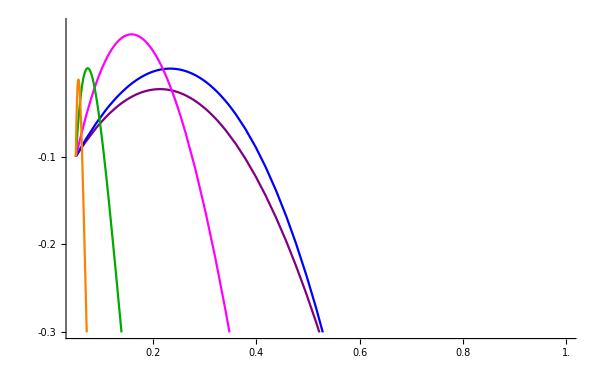

```mathematica
(*Plot f vs x for certain values of c to show the possible number of Einstein points that can be admitted by the system*)
(*Einstein points exist whenever f = 0*)
fplot=Plot[{f[x,c[[1]],cr],f[x,c[[2]],cr],f[x,2,cr],f[x,c[[4]],cr],f[x,c[[5]],cr]},{x,ℛ,1},PlotStyle->{Purple,Blue, Magenta,Darker[Green],Orange},AxesLabel->{MaTeX["x",FontSize->20],MaTeX["f(x)",FontSize->20]},Ticks->{{0.,0.2,0.4,0.6,0.8,1.},{-0.3,-0.2,-0.1}},PlotRange->{{ℛ,1},{-0.3,0.05}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}]
```

## Calculate the Einstein Points

### One Einstein Point: c2 (Limiting case)

```mathematica
(*Numerically solve f(x) = 0 to find the x value of the Einstein fixed point*)
xOneEinsteinPointc2=FindRoot[f[x,c[[2]],cr]==0,{x,0.2}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc2=x/.xOneEinsteinPointc2
```

0.232441

```mathematica
(*Calculate the z value of the Einstein point*)
zOneEinsteinPointc2=z[xOneEinsteinPointc2,c[[2]]]
```

0.0530018

```mathematica
(*Calculate the r value of the Einstein point*)
rOneEinsteinPointc2=r[xOneEinsteinPointc2,cr]
```

0.000102511

```mathematica
(*Check to see whether the Einstein fixed point found from the system of equations with + or -  before the square root gives the correct value of r*) 
1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xOneEinsteinPointc2,z->zOneEinsteinPointc2}
```

0.000102511

```mathematica
1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xOneEinsteinPointc2,z->zOneEinsteinPointc2}
```

0.499897

```mathematica
(*Put the Einstein points into a common variable name*)
EinsteinFP[1]={xOneEinsteinPointc2,0,zOneEinsteinPointc2,rOneEinsteinPointc2}
```

{0.232441,0,0.0530018,0.000102511}

### Two Einstein Points: c3

```mathematica
(*Numerically solve f(x) = 0 to find the x values of the Einstein fixed points*)
xTwoEinsteinPointsc3i=FindRoot[f[x,c[[3]],cr]==0,{x,0.1}];
xTwoEinsteinPointsc3ii=FindRoot[f[x,c[[3]],cr]==0,{x,0.4}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc3={x/.xTwoEinsteinPointsc3i,x/.xTwoEinsteinPointsc3ii}
```

{0.153934,0.311936}

```mathematica
(*Calculate the z values of the Einstein points*)
zTwoEinsteinPointsc3=z[xTwoEinsteinPointsc3,c[[3]]]
```

{0.0521363,0.153195}

```mathematica
(*Calculate the r values of the Einstein points*)
rTwoEinsteinPointsc3=r[xTwoEinsteinPointsc3,cr]
```

{0.0000405951,0.00019853}

```mathematica
(*Check to see whether the Einstein fixed point found from the system of equations with + or -  before the square root gives the correct value of r*)
```

```mathematica
1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xTwoEinsteinPointsc3[[1]],z->zTwoEinsteinPointsc3[[1]]}
```

0.0000405951

```mathematica
1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xTwoEinsteinPointsc3[[1]],z->zTwoEinsteinPointsc3[[1]]}
```

0.499959

```mathematica
1/4 (1-√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xTwoEinsteinPointsc3[[2]],z->zTwoEinsteinPointsc3[[2]]}
```

0.00019853

```mathematica
1/4 (1+√(1+4 x-12 x^2+4 z-12 z^2-12 ℛ+12 x ℛ))/.{x->xTwoEinsteinPointsc3[[2]],z->zTwoEinsteinPointsc3[[2]]}
```

0.499801

```mathematica
(*Put the Einstein points into a common variable name*)
EinsteinFP[2]={xTwoEinsteinPointsc3[[1]],0,zTwoEinsteinPointsc3[[1]],rTwoEinsteinPointsc3[[1]]}
EinsteinFP[3]={xTwoEinsteinPointsc3[[2]],0,zTwoEinsteinPointsc3[[2]],rTwoEinsteinPointsc3[[2]]}
```

{0.153934,0,0.0521363,0.0000405951}

{0.311936,0,0.153195,0.00019853}

```mathematica
(*Put the Einstein points into a table*)
EinsteinFPs=Table[EinsteinFP[i],{i,1,3}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each Einstein fixed point*)
TableForm[Table[{EinsteinFPs[[i]]//MatrixForm,Simplify[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],z->EinsteinFPs[[i,3]],r->EinsteinFPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],z->EinsteinFPs[[i,3]],r->EinsteinFPs[[i,4]]}]]//MatrixForm},{i,1,3}],TableHeadings->{{"c2","c3"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues
c2 | (0.232441
0
0.0530018
0.000102511) | (0. | -0.420102 | 0 | 0
0.0407739 | 0. | -0.113665 | -0.333197
0 | -0.150578 | 0. | 0
0 | -0.000410003 | 0 | 0.) | (-0.0110836
0.0110836
4.92292×10^-16
0.)
c3 | (0.153934
0
0.0521363
0.0000405951) | (0. | -0.263805 | 0 | 0
-0.0377327 | 0. | -0.11453 | -0.333279
0 | -0.148254 | 0. | 0
0 | -0.000162374 | 0 | 0.) | (-0.16428
0.16428
3.659×10^-18
0.)
 | (0.311936
0
0.153195
0.00019853) | (0. | -0.540686 | 0 | 0
0.120269 | 0. | -0.0134718 | -0.333069
0 | -0.389179 | 0. | 0
0 | -0.000793964 | 0 | 0.) | (-1.89486×10^-18+0.243968 ⅈ
-1.89486×10^-18-0.243968 ⅈ
-4.48035×10^-19+0. ⅈ
0.+0. ⅈ)

## Analyse the Equations of State

```mathematica
(*Define the pressure for each component*)
Px[x_,ℛ_]=-ℛ+ℛ*x-x^2;
Pz[z2_]=-z2^2;
Pr[r2_]=r2/3-4*r2^2/3;
```

```mathematica
(*Define the equations of state for each component*)
wEffx[x_,ℛ3_]=Px[x,ℛ3]/x;
wEffz[z2_]=Pz[z2]/z2;
wEffr[r2_]=Pr[r2]/r2;
```

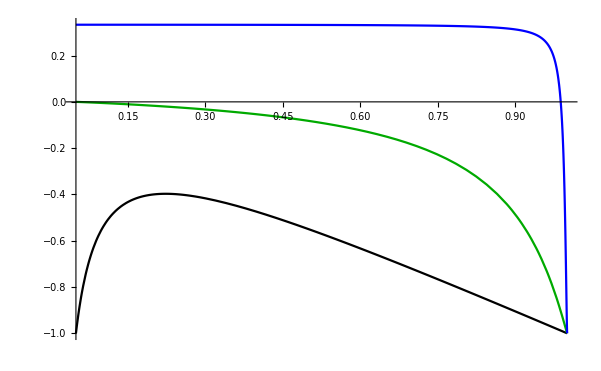

```mathematica
(*Plot the dark energy, dark matter and radiation equations of state in terms of x*)
xWeff=Plot[{wEffx[x,ℛ3],wEffz[z[x,0.1]],wEffr[r[x,cr]]},{x,ℛ,1},PlotStyle->{Black,Darker[Green],Blue},GridLines->{{},{-1/3}},GridLinesStyle->Directive[Thick,Dashed]]
```

## x-Y Phase Spaces and Potentials

## Set-up

### Phase Spaces

```mathematica
(*Define the scale factor (a) in terms of the dark energy (x)*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-ℛ);
a[x_,x0_]=(ca[x0]*((x-ℛ)/(1-x)))^((-1)/(3*(1-ℛ)));
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS) in terms of Y^2/(1-Y^2)*)
ffs=(1/3)*(x+z[x,c]+r[x,cr]);
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the FFS, +FFS and -FFS needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Set up the plot for the x = ℛ and x = 1 separatrices*)
Sep=ContourPlot[{x==ℛ,x==1},{x,0,1.1},{Y,-1,1},ContourStyle->{{Thick,Black}}];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of Y^2/(1-Y^2)*)
cfs[x0_]= x/3+z[x,c]/3+r[x,cr]/3-(x0/3+z[x0,c]/3+r[x0,cr]/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the CFS, +CFS and -CFS needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFS[x0_]=Sqrt[cfs[x0]/(1+cfs[x0])];
```

```mathematica
(*Set up the plot for the common fixed points in the phase spaces*)
FPShow=ListPlot[{{ℛ,Sqrt[ℛ/(3+ℛ)]},{ℛ,-Sqrt[ℛ/(3+ℛ)]},{ℛ,1},{ℛ,-1},{1,1},{1,-1},{1,1/Sqrt[2]},{1,-1/Sqrt[2]}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration equation*)
Accn=z[x,c]*(1-3z[x,c])+2*r[x,cr]*(1-2*r[x,cr])-3*ℛ+x*(1+3*ℛ)-3*x^2;
```

```mathematica
(*Define the format of phase spaces*)
PhaseSpaceFormatxY={FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}};
```

### Potentials

```mathematica
(*Define the potential term Ua^2*)
U[x_,x0_]=-a[x,x0]^2*(x/6+z[x,c]/6+r[x,cr]/6);
```

```mathematica
(*Set up the plot for the separatrices*)
xℛx1=ContourPlot[{x==ℛ,x==1},{x,0,1.01},{U,-2,1},ContourStyle->{{Black,Thick,Dashed}}];
```

```mathematica
(*Find the second derivative of U with respect to x*)
d2Udx2[x_,x0_]=Simplify[D[U[x,x0],{x,2}]];
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,Y0_]=-(x0/6+z[x0,c]/6+r[x0,cr]/6-Y0^2/(2*(1-Y0^2)));
```

```mathematica
(*Define the format for the plots of the potentials*)
FormatUx={ImageSize->{600,400},PlotRangePadding->{0.04,0},BaseStyle->{FontSize->18},Frame->True,FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["U",FontSize->18],270Degree]}};
```

## No Einstein Point: c1

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc1[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[1]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[1]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0.1,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.16,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
FFSc1=Plot[{FFS[[1]],-FFS[[1]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the curve where acceleration is zero for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

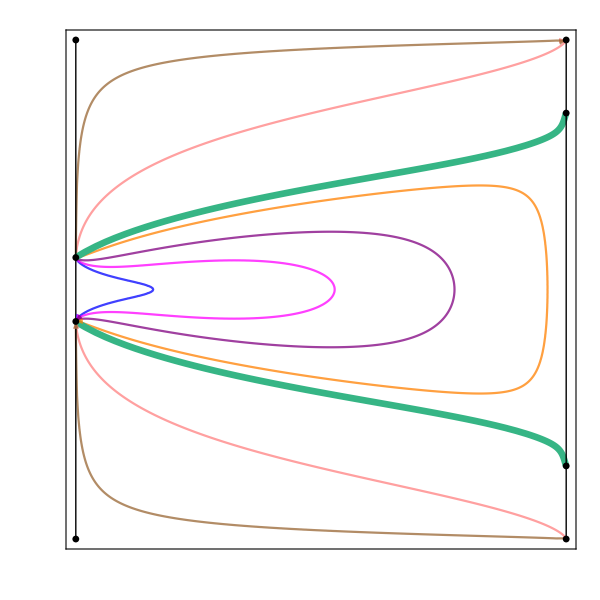

```mathematica
(*Show all components of the phase space*)
PhaseSpacec1=Show[Trajc1,Accnc1,FFSc1,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[x,0.2][[1]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{x,ℛ,0.2},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0.12][[1]]},{x,ℛ,0.63},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.18][[1]]},{x,ℛ,0.85},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.225][[1]]},{x,ℛ,0.965},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0][[1]]},{x,0.2,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.12][[1]]},{x,0.63,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[7]=Plot[{Energy[0.2,0.18][[1]]},{x,0.85,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[8]=Plot[{Energy[0.2,0.225][[1]]},{x,0.965,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,8}];
```

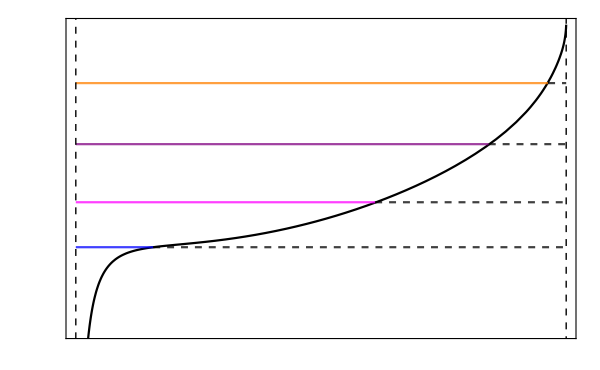

```mathematica
(*Show the potential and the energies of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.01Range[-5,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.05,0}}]
```

### Final Plot

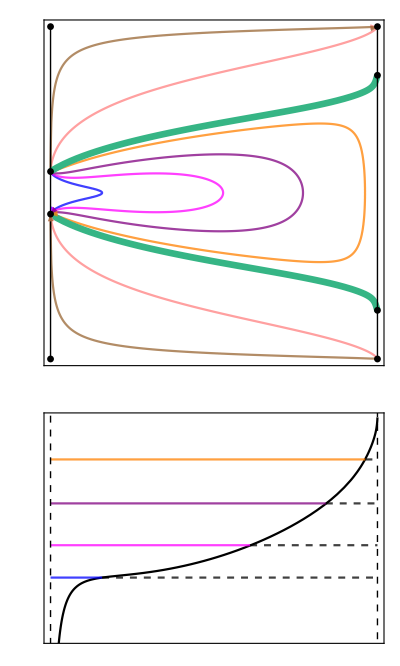

```mathematica
(*Plot the phase space and potential together*)
xYc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,0}]
```

## One Einstein Point: c2

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc2[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[2]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[2]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.12,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.16,0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,8}];
```

```mathematica
(*Plot the FFS*)
FFSc2=Plot[{FFS[[2]],-FFS[[2]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
CFSc2=Plot[{CFS[xOneEinsteinPointc2][[2]],-CFS[xOneEinsteinPointc2][[2]]},{x,ℛ,.8},PlotStyle->{Black},PlotRange->Full,PlotPoints->1000];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{xOneEinsteinPointc2,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the curve where acceleration is zero for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

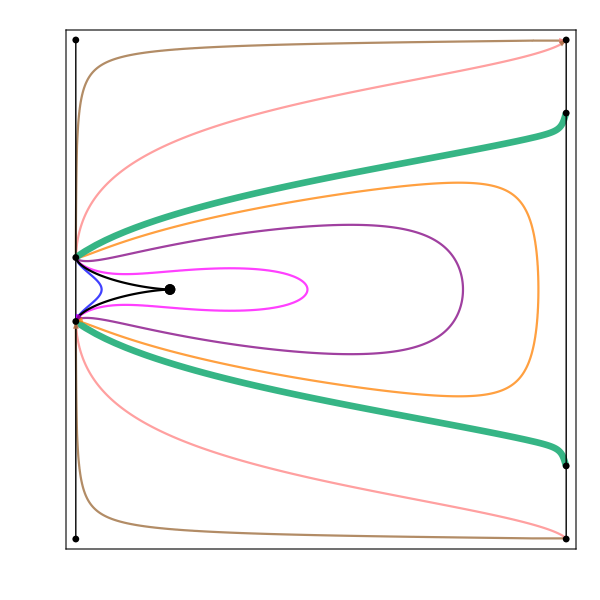

```mathematica
(*Show all components of the phase space*)
PhaseSpacec2=Show[Trajc2, FFSc2,CFSc2,Einsteinc2,Sep,FPShow,PhaseSpaceFormatxY]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative/zero value means it's a minimum/maximum/cusp*)
d2Udx2[xOneEinsteinPointc2,0.1][[2]]
```

-0.000250984

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[x,0.1][[2]]},{x,ℛ,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the energies of the trajectories in the phase space*)
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{x,ℛ,0.1},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0.07][[2]]},{x,ℛ,0.49},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.12][[2]]},{x,ℛ,0.8},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.16][[2]]},{x,ℛ,0.948},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0][[2]]},{x,0.1,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.07][[2]]},{x,0.49,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.12][[2]]},{x,0.8,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.16][[2]]},{x,0.948,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,8}];
```

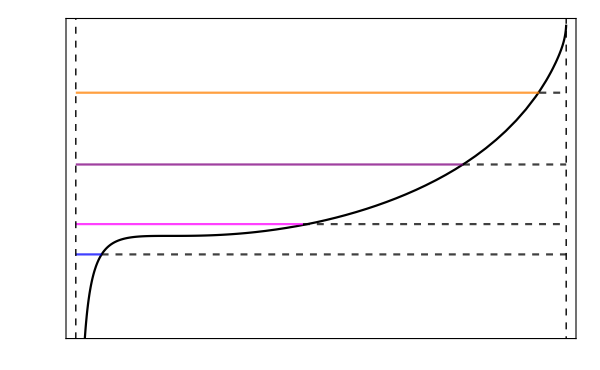

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.005Range[-5,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.025,0}}]
```

### Final Plot

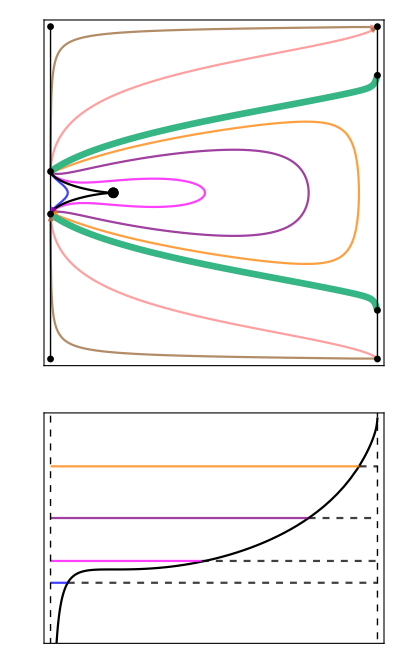

```mathematica
(*Plot the phase space and potential together*)
xYc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,0}]
```

## Three Einstein Points: c3

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajc3[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[3]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0,0.08]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.061,0.08]],{x,ℛ,xTwoEinsteinPointsc3[[1]]},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.061,0.08]],{x,xTwoEinsteinPointsc3[[1]],1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.1,0.08]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.15,0.08]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.28,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->300,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.28,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->300,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,ℛ,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,ℛ,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,9}];
```

```mathematica
(*Plot the FFS*)
FFSc3=Plot[{FFS[[3]],-FFS[[3]]},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotPoints->500];
```

```mathematica
(*Plot the CFS curves*)
CFSc3=Plot[{CFS[xTwoEinsteinPointsc3][[3]],-CFS[xTwoEinsteinPointsc3][[3]]},{x,ℛ,.8},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{xTwoEinsteinPointsc3[[1]],0},{xTwoEinsteinPointsc3[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{x,ℛ,1},{Y,-1,1},ContourStyle->{Gray, Thick,Opacity[0.5]},PlotPoints->200];
```

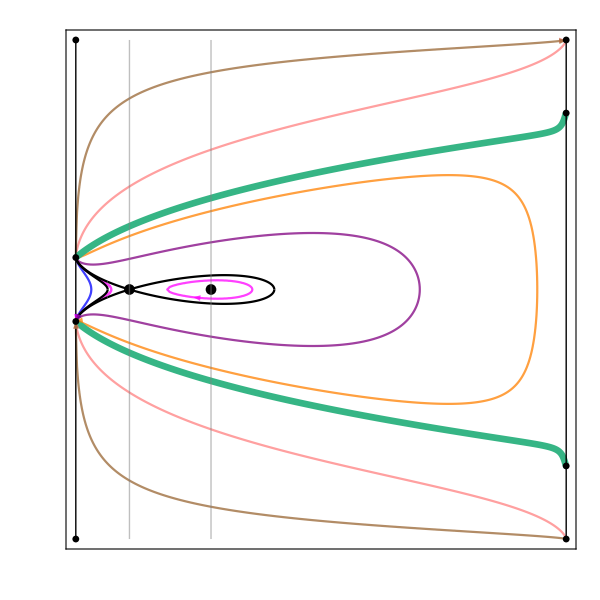

```mathematica
(*Show all components of the phase space*)
PhaseSpacec3=Show[Trajc3, FFSc3,CFSc3,Einsteinc3,Sep,FPShow,Accnc3,PhaseSpaceFormatxY]
```

```mathematica
(*Value of a at centre Einstein point*)
aMax=a[0.3119359520430131,0.08]
```

0.422214

```mathematica
(*Find maximum x needed for 60 e-folds of accelerated expansion*)
aMin=aMax/Exp[60]
xMax=(aMin^(-3(1-ℛ))+ca[0.08]*ℛ)/(aMin^(-3(1-ℛ))+ca[0.08])
```

3.69712×10^-27

1.

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
d2Udx2[xTwoEinsteinPointsc3[[1]],0.08][[3]]
```

-0.152889

```mathematica
d2Udx2[xTwoEinsteinPointsc3[[2]],0.08][[3]]
```

0.0362945

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[x,0.08][[3]]},{x,ℛ,1},PlotStyle->{Black},PlotRange->{-0.04,0}];
```

```mathematica
(*Plot the energies of the trajectories in the phase*)
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0][[3]]},{x,ℛ,0.08},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.061][[3]]},{x,ℛ,0.118},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.061][[3]]},{x,0.23,0.39},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.1][[3]]},{x,ℛ,0.715},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.15][[3]]},{x,ℛ,0.945},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0][[3]]},{x,0.08,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.061][[3]]},{x,0.118,0.23},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.061][[3]]},{x,0.39,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.1][[3]]},{x,0.715,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.15][[3]]},{x,0.945,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,10}];
```

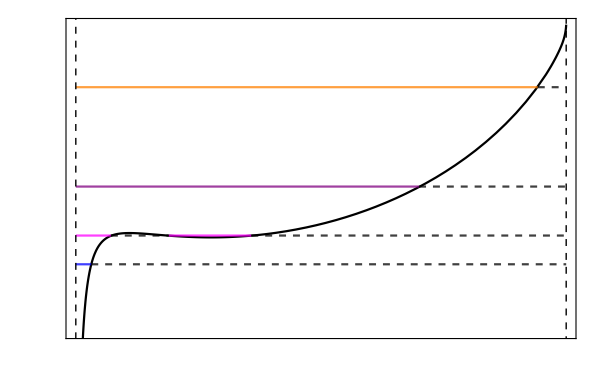

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,xℛx1,FormatUx,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.005Range[-4,0]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}},PlotRange->{{0.05,1},{-0.02,0}}]
```

### Final Plot

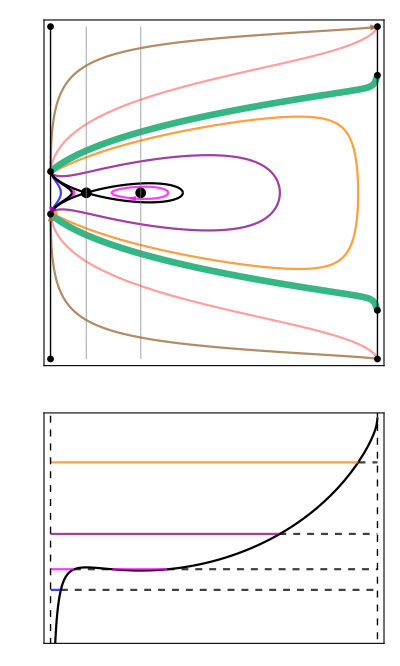

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,0}]
```

## Upper Limits to Matter and Radiation: c3 3-D Phase Space

## Set-up for x-Y-Z Phase Spaces

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajxYz[Y0_,x0_]:=x/3+z[x,c][[3]]/3+r[x,cr]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+r[x0,cr]/3-Y0^2/(1-Y0^2))
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajxYZ and -trajxYZ needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajxYz[Y0_,x0_]=Sqrt[trajxYz[Y0,x0]/(1+trajxYz[Y0,x0])];
```

```mathematica
(*Plot the the common fixed points which exist in all of the phase spaces*)
FPShowxYz=ListPointPlot3D[{{ℛ,-Sqrt[ℛ/(3+ℛ)],0},{ℛ,Sqrt[ℛ/(3+ℛ)],0},{ℛ,1,0},{ℛ,-1,0},{1,1,1},{1,-1,1},{1,1/Sqrt[2],1},{1,-1/Sqrt[2],1}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the surface where acceleration is zero*)
AccnxYz=ContourPlot3D[z*(1-3*z)+x+2*r[x,cr]*(1-2*r[x,cr])-3*ℛ+3*ℛ*x-3*x^2==0,{x,ℛ,1},{Y,-1,1},{z,0,1}, ContourStyle->{Red,Opacity[0.3], Thick}];
```

## Two Einstein Points: c3

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c3trajxYz[1]=ParametricPlot3D[{x,trajxYz[0,0.08],z[x,c][[3]]},{x,ℛ,0.2},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[2]=ParametricPlot3D[{x,-trajxYz[0,0.08],z[x,c][[3]]},{x,ℛ,0.2},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[3]=ParametricPlot3D[{x,trajxYz[0.061,0.08],z[x,c][[3]]},{x,ℛ,xTwoEinsteinPointsc3[[1]]},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[4]=ParametricPlot3D[{x,-trajxYz[0.061,0.08],z[x,c][[3]]},{x,ℛ,xTwoEinsteinPointsc3[[1]]},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[5]=ParametricPlot3D[{x,trajxYz[0.061,0.08],z[x,c][[3]]},{x,xTwoEinsteinPointsc3[[1]],.9},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[6]=ParametricPlot3D[{x,-trajxYz[0.061,0.08],z[x,c][[3]]},{x,xTwoEinsteinPointsc3[[1]],.9},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[7]=ParametricPlot3D[{x,trajxYz[0.1,0.08],z[x,c][[3]]},{x,ℛ,.99},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[8]=ParametricPlot3D[{x,-trajxYz[0.1,0.08],z[x,c][[3]]},{x,ℛ,.99},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[9]=ParametricPlot3D[{x,trajxYz[0.15,0.08],z[x,c][[3]]},{x,ℛ,.99},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->8000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[10]=ParametricPlot3D[{x,-trajxYz[0.15,0.08],z[x,c][[3]]},{x,ℛ,.99},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->8000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[11]=ParametricPlot3D[{x,trajxYz[0.28,0.08],z[x,c][[3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[12]=ParametricPlot3D[{x,-trajxYz[0.28,0.08],z[x,c][[3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[13]=ParametricPlot3D[{x,trajxYz[0.6,0.08],z[x,c][[3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3trajxYz[14]=ParametricPlot3D[{x,-trajxYz[0.6,0.08],z[x,c][[3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
xYztrajc3=Table[c3trajxYz[i],{i,1,14}];
```

```mathematica
(*Plot the Einstein fixed points of the system*)
xYzEinsteinc3=ListPointPlot3D[{{xTwoEinsteinPointsc3[[1]],0,z[xTwoEinsteinPointsc3[[1]],c][[3]]},{xTwoEinsteinPointsc3[[2]],0,z[xTwoEinsteinPointsc3[[2]],c][[3]]}},PlotStyle->{Black,PointSize[0.014]}];
```

```mathematica
(*Plot the CFS*)
xYzCFSc3=ParametricPlot3D[{{x,CFS[xTwoEinsteinPointsc3[[1]]][[3]],z[x,c][[3]]},{x,-CFS[xTwoEinsteinPointsc3[[1]]][[3]],z[x,c][[3]]}},{x,ℛ,.9},PlotStyle->Black,PlotRange->{{ℛ,1},{-1,1},{0,1}},PlotPoints->500];
```

```mathematica
(*Plot the FFS*)
xYzFFSc3=ParametricPlot3D[{{x,FFS[[1]],z[x,c][[3]]},{x,-FFS[[1]],z[x,c][[3]]}},{x,ℛ,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the first integral (c) surface*)
xYzSurfacec3=ParametricPlot3D[{x,Y,z[x,c][[3]]},{x,ℛ,1},{Y,-1,1},PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None];
```

```mathematica
(*Show all components of the phase space*)
xYzc3=Show[xYztrajc3,FPShowxYz,xYzFFSc3,xYzCFSc3, xYzEinsteinc3,xYzSurfacec3,AccnxYz,AxesLabel->{MaTeX["x",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["z",FontSize->20]},PlotRange->{{ℛ,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}];
```

## Upper Limits to Matter and Radiation: a-y Phase Space and Potential for c3 case

## Set-up

### Variables in terms of a

```mathematica
(*Express the dark matter (z), radiation (r) and dark energy (x) in terms of the scale factor (a)*)
xa[a_,x0_]=(a^(-3*(1-ℛ))+ca[x0]*ℛ)/(a^(-3*(1-ℛ))+ca[x0]);

ra[a_,x0_,cr_]=cr*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(4/(3*(1-ℛ)))/(1+cr*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(4/(3*(1-ℛ))));

za[a_,x0_,c_]=c*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(1/(1-ℛ))/(1+c*((xa[a,x0]-ℛ)/(1-xa[a,x0]))^(1/(1-ℛ)));
```

```mathematica
(*Define f(a), the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When f = 0, there is an Einstein fixed point*)
fa[a_,x0_,c_,cr_]=za[a,x0,c]*(1-3*za[a,x0,c])+2*ra[a,x0,cr]*(1-2*ra[a,x0,cr])-3*ℛ+xa[a,x0]*(1+3*ℛ)-3*xa[a,x0]^2;
```

### Set up for plots of the phase space

```mathematica
(*Define the equation for the Flat Friedmann Separatrix (FFS) in terms of y^2, which is found from the Friedmann equation*)
ffsay[a_,x0_]=(1/3)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Take the square root of ffsay for y*)
(*Note that when plotting the FFS, +FFSay and -FFSay needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSay[a_,x0_]=Sqrt[ffsay[a,x0]];
```

```mathematica
(*Define the equation for the Closed Friedmann Separatrix (CFS) in terms of y^2, which is found from th Friedmann equation*)
(*aE denotes the value of a at an Einstein fixed point*)
cfsay[a_,aE_,x0_]= xa[a,x0]/3+za[a,x0,c]/3+ra[a,x0,cr]/3-((aE/a)^2)*(xa[aE,x0]/3+za[aE,x0,c]/3+ra[aE,x0,cr]/3);
```

```mathematica
(*Take the square root of cfsay for y*)
(*Note that when plotting the CFS, +CFSay and -CFSay needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFSay[a_,aE_,x0_]=Sqrt[cfsay[a,aE,x0]];
```

```mathematica
(*Define the acceleration equation*)
Accnay[a_,x0_]=za[a,x0,c]*(1-3*za[a,x0,c])+xa[a,x0]+2*ra[a,x0,cr]*(1-2*ra[a,x0,cr])-3*ℛ+3*ℛ*xa[a,x0]-3*xa[a,x0]^2;
```

```mathematica
(*Define the format of phase spaces*)
PhaseSpaceFormatay={FrameLabel->{MaTeX["a",FontSize->18],Rotate[MaTeX["y",FontSize->18],300]},PlotRange->{{0,1},{-1.5,1.5}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{y,MaTeX[y,"DisplayStyle"->False,FontSize->18]},{y,0.5Range[-3,3]}],None},{Table[{a,MaTeX[a,"DisplayStyle"->False,FontSize->18]},{a,0.2Range[0,5]}],None}}};
```

### Set up for the plots of the potential

```mathematica
(*Define a0 = 1 today*)
a0=1;
```

```mathematica
(*Define the potential term Ua^2*)
Uay[a_,x0_]=-(a^2/6)*(xa[a,x0]+za[a,x0,c]+ra[a,x0,cr]);
```

```mathematica
(*Define the energy of the trajectories*)
Energyay[x0_,y0_]=-(xa[a0,x0]/6+za[a0,x0,c]/6+ra[a0,x0,cr]/6-y0^2/2);
```

```mathematica
(*Define the format of the potential plot*)
FormatUa={ImageSize->{600,400},PlotRangePadding->{0.04,0},BaseStyle->{FontSize->18},Frame->True,FrameLabel->{MaTeX["a",FontSize->18],Rotate[MaTeX["U",FontSize->18],270Degree]}};
```

## Find the Einstein Points in Each Case

### Two Einstein Points: c2

```mathematica
(*Numerically solve f = 0 to find the Einstein fixed points*)
aTwoEinsteinPointsc3i=FindRoot[fa[a,0.08,c,cr][[3]]==0,{a,0.4}];
aTwoEinsteinPointsc3ii=FindRoot[fa[a,0.08,c,cr][[3]]==0,{a,0.7}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc3={a/.aTwoEinsteinPointsc3i,a/.aTwoEinsteinPointsc3ii}
```

{0.422214,0.627896}

### Phase Space

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajayc3[y0_,x0_]:=y^2==xa[a,x0]/3+za[a,x0,c][[3]]/3+ra[a,x0,cr]/3-(1/a^2)*(xa[a0,x0]/3+za[a0,x0,c][[3]]/3+ra[a0,x0,cr]/3-y0^2);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
c3aytraj[1]=ContourPlot[Evaluate[trajayc3[0,0.08]],{a,0,1.1},{y,-2,2},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,0,0,0,0,.02,0,0,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[2]=ContourPlot[Evaluate[trajayc3[0.061,0.08]],{a,0,aTwoEinsteinPointsc3[[2]]},{y,-2,2},PlotPoints->200,PlotRange->Full,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02},1]]],Arrow[x]};
```

```mathematica
c3aytraj[3]=ContourPlot[Evaluate[trajayc3[0.061,0.08]],{a,aTwoEinsteinPointsc3[[2]],1.1},{y,-2,2},PlotRange->Full,PlotPoints->200,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[4]=ContourPlot[Evaluate[trajayc3[0.1,0.08]],{a,0,1.5},{y,-2,2},PlotPoints->100,PlotRange->Full,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[5]=ContourPlot[Evaluate[trajayc3[0.15,0.08]],{a,0,1.5},{y,-2,2},PlotPoints->100,PlotRange->Full,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[6]=ContourPlot[Evaluate[trajayc3[0.28,0.08]],{a,0,1.5},{y,0,2},PlotPoints->300,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[7]=ContourPlot[Evaluate[trajayc3[0.28,0.08]],{a,0,1.5},{y,-2,0},PlotPoints->300,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[8]=ContourPlot[Evaluate[trajayc3[0.6,0.08]],{a,0,1.5},{y,0,2},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3aytraj[9]=ContourPlot[Evaluate[trajayc3[0.6,0.08]],{a,0,1.5},{y,-2,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add the trajectories into a table*)
Trajc3ay=Table[c3aytraj[i],{i,1,9}];
```

```mathematica
(*Plot the FFS*)
FFSayc3=Plot[{FFSay[a,0.08][[3]],-FFSay[a,0.08][[3]]},{a,0,5},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotPoints->1000,PlotRange->Full];
```

```mathematica
(*Plot the CFS curves*)
CFSayc3=Plot[{CFSay[a,aTwoEinsteinPointsc3,0.08][[3]],-CFSay[a,aTwoEinsteinPointsc3,0.08][[3]]},{a,0,5},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinayc3=ListPlot[{{aTwoEinsteinPointsc3[[1]],0},{aTwoEinsteinPointsc3[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the boundaries between accelerating and decelerating regions for this case*)
Accnayc3=ContourPlot[Accnay[a,0.08][[3]]==0,{a,0,5},{y,-2,2},ContourStyle->{Red, Thick},PlotPoints->100,PlotRange->Full];
```

```mathematica
(*Set up the plot for the a = 0 (x = 1) separatrix*)
Sepay=ContourPlot[{a==0},{a,-0.1,0.1},{y,-2,2},ContourStyle->{{Thick,Black}}];
```

```mathematica
(*Set up the plot for the de Sitter fixed points*)
dSFPs=ListPlot[{{0,1},{0,-1}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

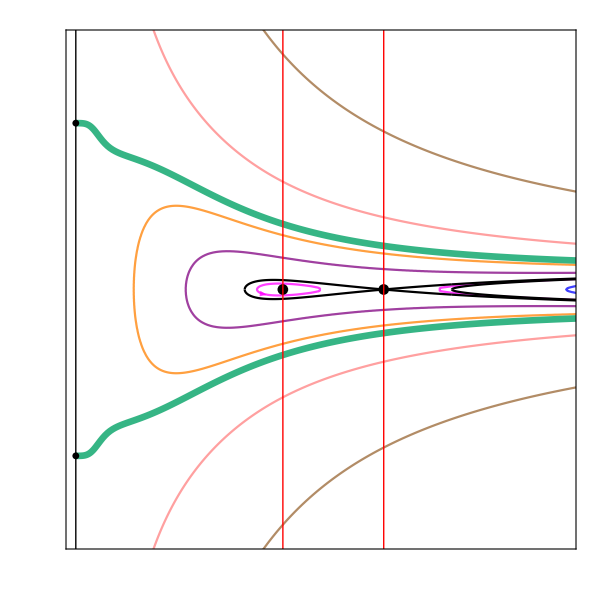

```mathematica
(*Show all components of the phase space*)
PhaseSpaceayc3=Show[Trajc3ay,FFSayc3,CFSayc3,Einsteinayc3,Accnayc3,Sepay,dSFPs,PhaseSpaceFormatay]
```

### Potential

```mathematica
(*Plot the potential for this case*)
Uayc3=Plot[{U[xa[a,0.08],0.08][[3]]},{a,0,1.5},PlotStyle->{Black},PlotRange->{-0.04,0}];
```

```mathematica
(*Plot the energies of the trajectories in the phase*)
```

```mathematica
c3ayEnergy[1]=Plot[{Energyay[0.08,0][[3]]},{a,1,1.5},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[2]=Plot[{Energyay[0.08,0.061][[3]]},{a,0.37,0.495},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[3]=Plot[{Energyay[0.08,0.061][[3]]},{a,0.74,1.5},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[4]=Plot[{Energyay[0.08,0.1][[3]]},{a,0.225,1.5},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[5]=Plot[{Energyay[0.08,0.15][[3]]},{a,0.12,1.5},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3ayEnergy[6]=Plot[{Energyay[0.08,0][[3]]},{a,0,1},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[7]=Plot[{Energyay[0.08,0.061][[3]]},{a,0,0.37},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[8]=Plot[{Energyay[0.08,0.061][[3]]},{a,0.495,0.74},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[9]=Plot[{Energyay[0.08,0.1][[3]]},{a,0,0.225},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3ayEnergy[10]=Plot[{Energyay[0.08,0.15][[3]]},{a,0,0.12},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add the energies into a table*)
Energyayc3=Table[c3ayEnergy[i],{i,1,10}];
```

```mathematica
(*Plot the a = 0 (x = 1) separatrix*)
SepUa=ContourPlot[{a==0},{a,-0.1,0.1},{U,-1,.1},ContourStyle->{{Black,Thick,Dashed}}];
```

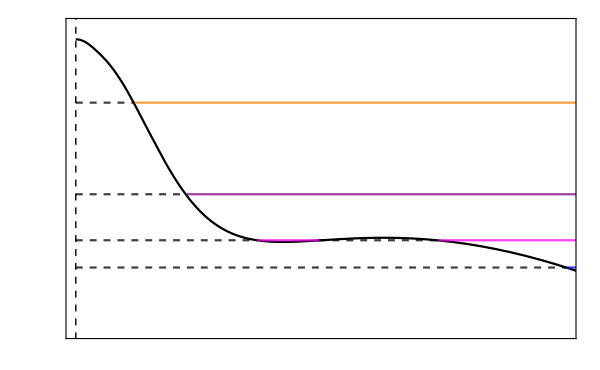

```mathematica
(*Show the potential and energies of the trajectories together*)
Potentialayc3=Show[Uayc3,Energyayc3,SepUa,FormatUa,FrameTicks->{{Table[{U,MaTeX[U,"DisplayStyle"->False,FontSize->18]},{U,0.005Range[-4,0]}],None},{Table[{a,MaTeX[a,"DisplayStyle"->False,FontSize->18]},{a,0.2Range[0,5]}],None}},PlotRange->{{0,1},{-0.02,0.001}}]
```

### Final Plot

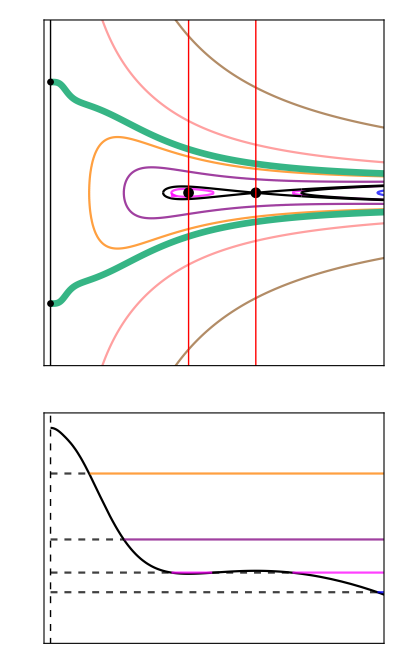

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpaceayc3,Potentialayc3},Spacings->{0,0}]
```

## Constant Curvature Hypersurface: Dark Energy and Matter only

## Find the Limiting Cases

```mathematica
(*Clear the value of K*)
(*K = k/ρ* *)
Clear[K]
```

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the compactified Hubble expansion variable, Y, dark matter, z, and  radiation, r*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/(1-Y^2)^(1/2)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(z*(1-3z)+2*r*(1-2r)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*Y*z*(1-z)/((1-Y^2)^(1/2))
de4:=r'=-4*Y*r*(1-r)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,z,r}];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
}
```

```mathematica
(*Remove arrows from fixed points and put them into a common variable name*)
FP[1]={x,Y/.FPs[[1,1]],z,r/.FPs[[1,2]]};
FP[2]={x,Y/.FPs[[2,1]],z,r/.FPs[[2,2]]};
FP[3]={x/.FPs[[15,1]],Y/.FPs[[15,2]],z/.FPs[[15,3]]};
FP[4]={x/.FPs[[16,1]],Y/.FPs[[16,2]],z/.FPs[[16,3]]};
FP[5]={x/.FPs[[17,1]],Y/.FPs[[17,2]],z/.FPs[[17,3]]};
FP[6]={x/.FPs[[18,1]],Y/.FPs[[18,2]],z/.FPs[[18,3]]};
FP[7]={x/.FPs[[21,1]],Y/.FPs[[21,2]],z/.FPs[[21,3]]};
FP[8]={x/.FPs[[22,1]],Y/.FPs[[22,2]],z/.FPs[[22,3]]};
```

```mathematica
(*Plot the fixed points of the system*)
FPShowConstantKXYZ=ListPointPlot3D[Table[FP[i],{i,3,8}], PlotStyle->{Black}];
```

```mathematica
(*Plot the fixed points that result from compactification*)
FPShowConstantKCompactXYZ=ListPointPlot3D[{{ℛ,1,0},{ℛ,-1,0},{ℛ,1,1},{ℛ,-1,1},{1,1,0},{1,-1,0},{1,1,1},{1,-1,1}},PlotStyle->Black];
```

```mathematica
(*Define z0 using the Planck 2018 density parameters*)
z0ConstantK=(Ωm/ΩΛ)*(ℛ/α);
```

```mathematica
(*Define a(z)*)
caz=z0ConstantK/(1-z0ConstantK);

aKz[z_]=(caz*(1-z)/z)^(1/3);
```

```mathematica
(*Define x at the Einstein fixed point from the Friedmann equation*)
xE[z_,K_]=3*K/(aKz[z]^2)-z;
```

```mathematica
(*Define the term left when y' = y = 0*)
fConstantK[z_,K_]=z*(1-3*z)-3*ℛ+xE[z,K]*(1+3*ℛ)-3*xE[z,K]^2;
```

```mathematica
(*Find the first derivative of fConstantK with respect to z*)
DfConstantK=D[fConstantK[z,K],z]
```

1+1.15 (-1-(15.2928 K (-(1-z)/z^2-1/z))/((1-z)/z)^(5/3))-6 (-1-(15.2928 K (-(1-z)/z^2-1/z))/((1-z)/z)^(5/3)) ((22.9393 K)/((1-z)/z)^(2/3)-z)-6 z

```mathematica
(*Solve DfConstantK = 0 for K*)
DfK=Solve[DfConstantK==0,K]
```

{{K→1/((-1.+1./z)^(2/3) z)0.000237548 (1.-1. z)^3 (-(1. (-1.+1./z)^(1/3) (-17.5868/(1.-1. z)-137.636 z-(91.757 z)/(1.-1. z)))/(1.-1. z)-1. √(-(8419.36 (-1.+1./z)^(2/3) z (0.15+12. z))/(1.-1. z)^3+((-1.+1./z)^(2/3) (-17.5868/(1.-1. z)-137.636 z-(91.757 z)/(1.-1. z))^2)/(1.-1. z)^2))},{K→1/((-1.+1./z)^(2/3) z)0.000237548 (1.-1. z)^3 (-(1. (-1.+1./z)^(1/3) (-17.5868/(1.-1. z)-137.636 z-(91.757 z)/(1.-1. z)))/(1.-1. z)+√(-(8419.36 (-1.+1./z)^(2/3) z (0.15+12. z))/(1.-1. z)^3+((-1.+1./z)^(2/3) (-17.5868/(1.-1. z)-137.636 z-(91.757 z)/(1.-1. z))^2)/(1.-1. z)^2))}}

```mathematica
(*Separate the solutions into variable names*)
KSol1=K/.DfK[[1]];
KSol2=K/.DfK[[2]];
```

```mathematica
(*Substitute the K terms found from df/dz = 0 back into fConstantK*)
fConstantKi=fConstantK[z,K]/.K->KSol1;
fConstantKii=fConstantK[z,K]/.K->KSol2;
```

```mathematica
(*Solve for z when fConstantK = 0*)
(*The limiting cases exist when f = df/dz = 0*)
zLim1=z/.FindRoot[fConstantKi==0,{z,0.18}]
zLim2=z/.FindRoot[fConstantKii==0,{z,0.05}]
```

0.183188

0.0533294

```mathematica
(*Find the corresponding K values in the limiting cases*)
KSolution1=KSol1/.z->zLim1
KSolution2=KSol2/.z->zLim2
```

0.030176

0.0847952

```mathematica
(*ℛ < RangeOfValidity < 1 must be satisfied in order for ℛ < x < 1 to be satisfied*)
(*Therefore KSolution1[[1]] is not a solution in the range ℛ < x < 1*)
RangeOfValidity[K_,z_]=3*K/(aKz[z]^2)-z;

RangeOfValidity[KSolution1,zLim1]

RangeOfValidity[KSolution2,zLim2]
```

0.0723313

0.232515

```mathematica
(*Redefine a compactified fConstantK*)
fConstantKCompact[z_,K_]=(z*(1-3*z)-3*ℛ+xE[z,K]*(1+3*ℛ)-3*xE[z,K]^2)/(Sqrt[1+(z*(1-3*z)-3*ℛ+xE[z,K]*(1+3*ℛ)-3*xE[z,K]^2)^2]);
```

```mathematica
(*Plot a dashed line representing the maximum value of Z when x = 1 in fConstantKCompact[Z,K]*)
ZMax=ContourPlot[{Z==2/3},{Z,0,1},{y,-1,1},Axes->True,Frame->False,ContourStyle->{Black,Dashed}];
```

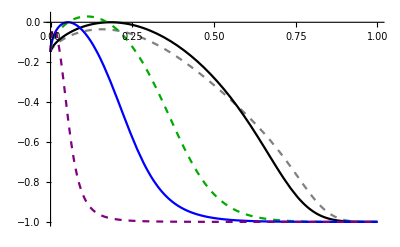

```mathematica
(*Plot the limiting cases as solid lines and the cases in between  as dashed lines*)
fPlots=Plot[{fConstantKCompact[z,0.025],fConstantKCompact[z,KSolution1],fConstantKCompact[z,0.06],fConstantKCompact[z,KSolution2],fConstantKCompact[z,0.2]},{z,0,1},PlotStyle->{{Gray,Dashed},Black,{Darker[Green],Dashed},Blue,{Purple,Dashed}}]
```

```mathematica
(*Calculate the values of k based on the Planck 2018 parameters*)
Ωk0Open=0.003;
Ωk0Closed=-0.001;

kOpen=-Ωk0Open*H0^2
kClosed=-Ωk0Closed*H0^2
```

-13.7336

4.57788

```mathematica
(*Define an array of K values*)
KValues={0.025,KSolution1,0.06,KSolution2,0.2}
```

{0.025,0.030176,0.06,0.0847952,0.2}

## Calculate the Einstein Fixed Points

### One Einstein Point: K2 (1st Limiting Case)

```mathematica
(*Numerically solve f(z) = 0 using FindRoot to find the z value of the Einstein fixed point*)
zOneEinsteinPointK2=FindRoot[fConstantKCompact[z,KValues[[2]]]==0,{z,0.2}];
```

```mathematica
(*Remove the arrow from the solution above*)
zOneEinsteinPointK2=z/.zOneEinsteinPointK2
```

0.183188

```mathematica
(*Calculate the x value of the Einstein point*)
xOneEinsteinPointK2=xE[zOneEinsteinPointK2,KValues[[2]]]
```

0.0723313

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFPConstantK[1]={xOneEinsteinPointK2,0,zOneEinsteinPointK2}
```

{0.0723313,0,0.183188}

```mathematica
(*Calculate the value of a at the Einstein fixed point*)
aOneEinsteinPointK2=aKz[zOneEinsteinPointK2]
```

0.595222

### Two Einstein Points: K3

```mathematica
(*Numerically solve f(z) = 0 using FindRoot to find the z values of the Einstein fixed points*)
zTwoEinsteinPointsK3i=FindRoot[fConstantKCompact[z,KValues[[3]]]==0,{z,0.05}];
zTwoEinsteinPointsK3ii=FindRoot[fConstantKCompact[z,KValues[[3]]]==0,{z,0.15}];
```

```mathematica
(*Put the z values of the Einstein points into one variable name for this case*)
zTwoEinsteinPointsK3={z/.zTwoEinsteinPointsK3i,z/.zTwoEinsteinPointsK3ii}
```

{0.0537588,0.172966}

```mathematica
(*Calculate the x values of the Einstein points*)
xTwoEinsteinPointsK3=xE[zTwoEinsteinPointsK3,KValues[[3]]]
```

{0.149647,0.311975}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPConstantK[2]={xTwoEinsteinPointsK3[[1]],0,zTwoEinsteinPointsK3[[1]]}
EinsteinFPConstantK[3]={xTwoEinsteinPointsK3[[2]],0,zTwoEinsteinPointsK3[[2]]}
```

{0.149647,0,0.0537588}

{0.311975,0,0.172966}

```mathematica
(*Calculate the values of a at the Einstein fixed points*)
aTwoEinsteinPointsK3=aKz[zTwoEinsteinPointsK3]
```

{0.940709,0.609244}

### One Einstein Point: K4 (2nd Limiting Case)

```mathematica
(*Numerically solve f(z) = 0 using FindRoot to find the z value of the Einstein fixed point*)
zOneEinsteinPointK4=FindRoot[fConstantKCompact[z,KValues[[4]]]==0,{z,0.05}];
```

```mathematica
(*Remove the arrow from the solution above*)
zOneEinsteinPointK4=z/.zOneEinsteinPointK4
```

0.0533294

```mathematica
(*Calculate the x value of the Einstein point*)
xOneEinsteinPointK4=xE[zOneEinsteinPointK4,KValues[[4]]]
```

0.232515

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFPConstantK[4]={xOneEinsteinPointK4,0,zOneEinsteinPointK4}
```

{0.232515,0,0.0533294}

```mathematica
(*Calculate the value of a at the Einstein fixed point*)
aOneEinsteinPointK4=aKz[zOneEinsteinPointK4]
```

0.943369

### Table of Einstein Fixed Points and their Eigenvalues/Eigenvectors

```mathematica
(*System of dimensionless differential equations describing dark energy, x, the compact Hubble expansion, Y, and dark matter with an upper bound, z*)
de1:=x'=-3*Y*(x-ℛ)*(1-x)/(1-Y^2)^(1/2)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*(z*(1-3z)+2*r*(1-2r)-3*ℛ+x*(1+3*ℛ)-3*x^2)
de3:=z'=-3*Y*z*(1-z)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the 3D Jacobian matrix for the x-Y-Z system. D[] differentiates each expression*)
JConstantK=Simplify[{{D[de1,x],D[de1,Y],D[de1,z]}, {D[de2,x],D[de2,Y],D[de2,z]}, {D[de3,x],D[de3,Y],D[de3,z]}}];
JConstantK//MatrixForm
```

(((-3.15+6. x) Y)/(√(1-Y^2)) | -(3. (0.05-1.05 x+x^2))/(√(1-Y^2) (-1.+Y^2)) | 0
1/6 (-1.15+6 x) (1-Y^2)^(3/2) | (Y (2 Y^2+4 (-1+Y^2)+4. (-1.+Y^2) (0.0375-0.5 r+r^2-0.2875 x+0.75 x^2-0.25 z+0.75 z^2)))/(2 √(1-Y^2)) | 1/6 (1-Y^2)^(3/2) (-1+6 z)
0 | (3 (-1+z) z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 z))/(√(1-Y^2)))

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPsConstantK=Table[EinsteinFPConstantK[i],{i,1,4}];
```

```mathematica
(*Find the Jacobian, eigenvalues and eigenvectors for each Einstein fixed point*)
TableForm[Table[{EinsteinFPsConstantK[[i]]//MatrixForm,Simplify[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],z->EinsteinFPsConstantK[[i,3]]}]//MatrixForm,Simplify[Eigenvalues[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],z->EinsteinFPsConstantK[[i,3]]}]]//MatrixForm,Simplify[Eigenvectors[JConstantK/.{x->EinsteinFPsConstantK[[i,1]],Y->EinsteinFPsConstantK[[i,2]],z->EinsteinFPsConstantK[[i,3]]}]]//MatrixForm},{i,1,4}],TableHeadings->{{"K2","K3","","K4"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues | 
K2 | (0.0723313
0
0.183188) | (0. | -0.0621483 | 0
-0.119335 | 0 | 0.0165218
0 | -0.448891 | 0.) | (2.64505×10^-18+0.0000387009 ⅈ
2.64505×10^-18-0.0000387009 ⅈ
-5.11697×10^-18+0. ⅈ) | (-0.13714-3.64595×10^-21 ⅈ | 5.5858×10^-18+0.0000853998 ⅈ | -0.990552+0. ⅈ
-0.13714+3.64595×10^-21 ⅈ | 5.5858×10^-18-0.0000853998 ⅈ | -0.990552+0. ⅈ
-0.13714+0. ⅈ | -1.15424×10^-17+0. ⅈ | -0.990552+0. ⅈ)
K3 | (0.149647
0
0.0537588) | (0. | -0.254204 | 0
-0.0420201 | 0 | -0.112908
0 | -0.152606 | 0.) | (0.167069
-0.167069
1.39338×10^-17) | (0.746947 | -0.490912 | 0.448414
0.746947 | 0.490912 | 0.448414
-0.9372 | -2.95295×10^-17 | 0.348791)
 | (0.311975
0
0.172966) | (0. | -0.540737 | 0
0.120309 | 0 | 0.00629967
0 | -0.429147 | 0.) | (-4.41225×10^-20+0.260305 ⅈ
-4.41225×10^-20-0.260305 ⅈ
1.21781×10^-23+0. ⅈ) | (-0.732922+0. ⅈ | -1.19615×10^-18+0.352822 ⅈ | -0.581672-4.46811×10^-19 ⅈ
-0.732922+0. ⅈ | -1.19615×10^-18-0.352822 ⅈ | -0.581672+4.46811×10^-19 ⅈ
-0.0522909+0. ⅈ | -3.53433×10^-21+0. ⅈ | 0.998632+0. ⅈ)
K4 | (0.232515
0
0.0533294) | (0. | -0.420232 | 0
0.040848 | 0 | -0.113337
0 | -0.151456 | 0.) | (-0.0000890192
0.0000890191
4.09969×10^-11) | (-0.940764 | -0.000199285 | -0.339062
0.940764 | -0.000199285 | 0.339062
0.940764 | -9.17788×10^-11 | 0.339062)

## Set-up for the Phase Spaces

```mathematica
(*Define the first integral of z(x), c, for the constant curvature case*)
cConstantK[x0_]=(z0ConstantK/(1-z0ConstantK))*((1-x0)/(x0-ℛ))^(1/(1-ℛ));
```

```mathematica
(*Define the first integral of z(x), c, for plotting the CFS*)
cConstantKCFS[xE_,zE_]=(zE/(1-zE))*((1-xE)/(xE-ℛ))^(1/(1-ℛ));
```

```mathematica
(*Plot the surface where acceleration is zero*)
AccnxYz=ContourPlot3D[-(1/6)*(z*(1-3*z)+x-3*ℛ+3*ℛ*x-3*x^2)==0,{x,ℛ,1},{Y,-1,1},{z,0,1}, ContourStyle->{Red,Opacity[0.3], Thick},PlotPoints->20];
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
ffsConstantK[x_,z_]=x/3+z/3;
```

```mathematica
(*Rearrange the FFS for Y*)
(*Note that when plotting the FFS, +FFSSubMan and -FFSSubMan needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
FFSConstantK[x_,z_]=ffsConstantK[x,z]/Sqrt[(1+ffsConstantK[x,z]^2)];
```

```mathematica
(*Plot the FFS*)
ConstantKFFS=ParametricPlot3D[{{x,FFSConstantK[x,z],z},{x,-FFSConstantK[x,z],z}},{x,ℛ,1},{z,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008],Opacity[0.3]}},PlotPoints->100,PlotRange->All,Mesh->None];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS) in terms of Y^2/(1-Y^2)*)
cfs[xE_,zE_]= x/3+z[x,cConstantKCFS[xE,zE]]/3-(xE/3+zE/3)/(a[x,xE]^2);
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the CFS, +CFS and -CFS needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
CFS[xE_,zE_]=Sqrt[cfs[xE,zE]]/Sqrt[(1+cfs[xE,zE])];
```

```mathematica
(*Define the format of phase spaces*)
PhaseSpaceFormatxY={FrameLabel->{MaTeX["x",FontSize->18],Rotate[MaTeX["Y",FontSize->18],300]},PlotRange->{{ℛ,1},{-1,1}},ImageSize->{600,600},PlotRangePadding->{0.04,0.04},BaseStyle->{FontSize->18},FrameTicks->{{Table[{Y,MaTeX[Y,"DisplayStyle"->False,FontSize->18]},{Y,0.5Range[-2,3]}],None},{Table[{x,MaTeX[x,"DisplayStyle"->False,FontSize->18]},{x,0.2Range[0,5]}],None}}};
```

```mathematica
PhaseSpaceFormatxYz={AxesLabel->{MaTeX["x",FontSize->20],MaTeX["Y",FontSize->20],MaTeX["z",FontSize->20]},PlotRange->{{ℛ,1},{-1,1},{0,1}},Ticks->{{0.,0.5,1.},{-1.,-0.5,0.,0.5,1.},{0.,0.5,1.}},ImageSize->{600,400},PlotRangePadding->{0.08,0.08,0.08},BaseStyle->{FontFamily->"CMU Serif",FontSize->20}};
```

## Case 1: 0 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[1]]
```

0.025

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK1[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK1[x0_]=Sqrt[trajConstantK1[x0]/(1+trajConstantK1[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK1[1]=ParametricPlot3D[{x,trajConstantK1[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[2]=ParametricPlot3D[{x,-trajConstantK1[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[3]=ParametricPlot3D[{x,trajConstantK1[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[4]=ParametricPlot3D[{x,-trajConstantK1[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[5]=ParametricPlot3D[{x,trajConstantK1[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[6]=ParametricPlot3D[{x,-trajConstantK1[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[7]=ParametricPlot3D[{x,trajConstantK1[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK1[8]=ParametricPlot3D[{x,-trajConstantK1[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK1Plots=Table[trajConstantK1[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK1Surface=x/3+z/3-K/(aKz[z]^2);
YK1Surface=Sqrt[yK1Surface/(1+yK1Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK1Surface=ParametricPlot3D[{{x,YK1Surface,z},{x,-YK1Surface,z}},{x,ℛ,1},{z,0,.9},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK1=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK1=Show[trajConstantK1Plots,ConstantK1Surface,AccnxYz,EinsteinPointsK1,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK1Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK1Proj[1]=ContourPlot[Evaluate[trajConstantK1Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK1Proj[2]=ContourPlot[Evaluate[trajConstantK1Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK1Proj[3]=ContourPlot[Evaluate[trajConstantK1Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK1Proj[4]=ContourPlot[Evaluate[trajConstantK1Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK1ProjectionPlots=Table[trajConstantK1Proj[i],{i,1,4}];
```

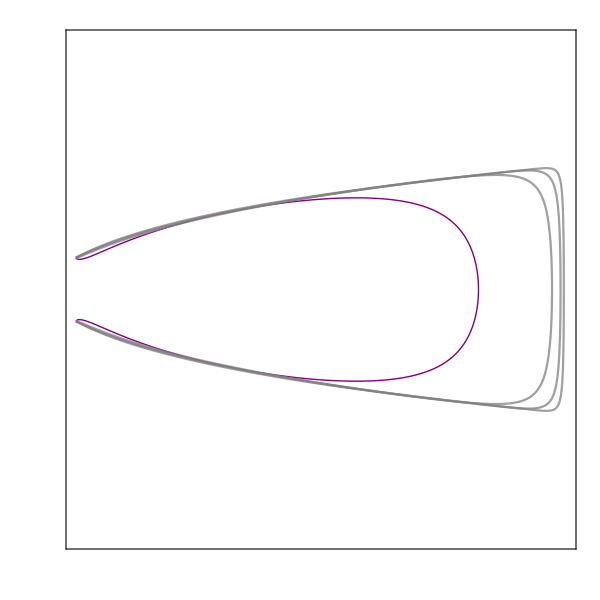

```mathematica
(*Show the trajectories*)
Show[trajConstantK1ProjectionPlots,PhaseSpaceFormatxY]
```

## Limiting Case 2: 1 Einstein Fixed Point

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[2]]
```

0.030176

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK2[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK2[x0_]=Sqrt[trajConstantK2[x0]/(1+trajConstantK2[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK2[1]=ParametricPlot3D[{x,trajConstantK2[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[2]=ParametricPlot3D[{x,-trajConstantK2[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[3]=ParametricPlot3D[{x,trajConstantK2[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[4]=ParametricPlot3D[{x,-trajConstantK2[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[5]=ParametricPlot3D[{x,trajConstantK2[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[6]=ParametricPlot3D[{x,-trajConstantK2[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[7]=ParametricPlot3D[{x,trajConstantK2[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK2[8]=ParametricPlot3D[{x,-trajConstantK2[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK2Plots=Table[trajConstantK2[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK2Surface=x/3+z/3-K/(aKz[z]^2);
YK2Surface=Sqrt[yK2Surface/(1+yK2Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK2Surface=ParametricPlot3D[{{x,YK2Surface,z},{x,-YK2Surface,z}},{x,ℛ,1},{z,0,.9},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK2=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsK2=ListPointPlot3D[{EinsteinFPConstantK[1]},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK2=ParametricPlot3D[{{x,CFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2],z[x,cConstantKCFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2]]},{x,-CFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2],z[x,cConstantKCFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2]]}},{x,ℛ,1},PlotStyle->Black];
```

```mathematica
(*Show all components of the phase space*)
xYZK2=Show[trajConstantK2Plots,ConstantK2Surface,AccnxYz,EinsteinPointsK2,EinsteinFixedPointsK2,CFSK2,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK2Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK2Proj[1]=ContourPlot[Evaluate[trajConstantK2Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK2Proj[2]=ContourPlot[Evaluate[trajConstantK2Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK2Proj[3]=ContourPlot[Evaluate[trajConstantK2Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK2Proj[4]=ContourPlot[Evaluate[trajConstantK2Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK2ProjectionPlots=Table[trajConstantK2Proj[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsK2Projection=ListPlot[{{EinsteinFPConstantK[1][[1]],EinsteinFPConstantK[1][[2]]}},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK2Projection=ParametricPlot[{{x,CFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2]},{x,-CFS[EinsteinFPConstantK[1][[1]],zOneEinsteinPointK2]}},{x,ℛ,1},PlotStyle->Black];
```

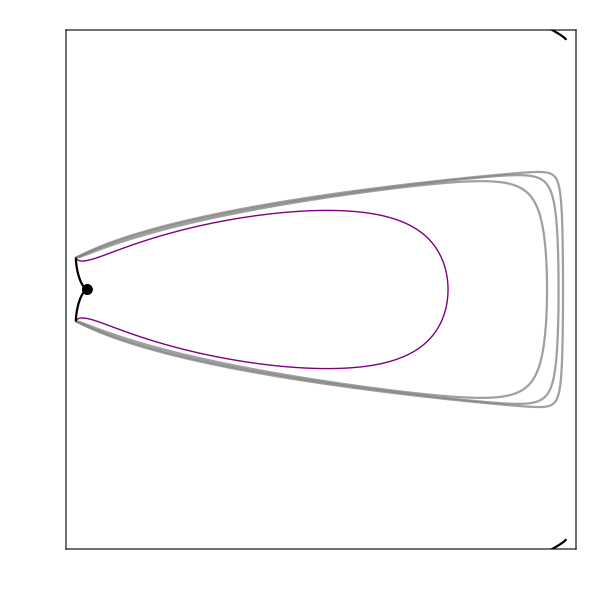

```mathematica
(*Show the trajectories*)
Show[trajConstantK2ProjectionPlots,EinsteinFixedPointsK2Projection,CFSK2Projection,PhaseSpaceFormatxY]
```

## Case 3: 2 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[3]]
```

0.06

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK3[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK3[x0_]=Sqrt[trajConstantK3[x0]/(1+trajConstantK3[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK3[1]=ParametricPlot3D[{x,trajConstantK3[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[2]=ParametricPlot3D[{x,-trajConstantK3[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[3]=ParametricPlot3D[{x,trajConstantK3[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[4]=ParametricPlot3D[{x,-trajConstantK3[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[5]=ParametricPlot3D[{x,trajConstantK3[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[6]=ParametricPlot3D[{x,-trajConstantK3[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[7]=ParametricPlot3D[{x,trajConstantK3[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK3[8]=ParametricPlot3D[{x,-trajConstantK3[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK3Plots=Table[trajConstantK3[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK3Surface=x/3+z/3-K/(aKz[z]^2);
YK3Surface=Sqrt[yK3Surface/(1+yK3Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK3Surface=ParametricPlot3D[{{x,YK3Surface,z},{x,-YK3Surface,z}},{x,ℛ,1},{z,0,.75},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK3=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsK3=ListPointPlot3D[{EinsteinFPConstantK[2],EinsteinFPConstantK[3]},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK3=ParametricPlot3D[{{x,CFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]],z[x,cConstantKCFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]]]},{x,-CFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]],z[x,cConstantKCFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]]]}},{x,ℛ,1},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK3=ParametricPlot3D[{{x,CFS[EinsteinFPConstantK[2][[1]]],z[x,cConstantK[EinsteinFPConstantK[2][[1]]]]},{x,-CFS[EinsteinFPConstantK[2][[1]]],z[x,cConstantK[EinsteinFPConstantK[2][[1]]]]}},{x,ℛ,1},PlotStyle->Black];
```

```mathematica
(*Show all components of the phase space*)
xYZK3=Show[trajConstantK3Plots,ConstantK3Surface,AccnxYz,EinsteinPointsK3,EinsteinFixedPointsK3,CFSK3,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK3Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK3Proj[1]=ContourPlot[Evaluate[trajConstantK3Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK3Proj[2]=ContourPlot[Evaluate[trajConstantK3Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK3Proj[3]=ContourPlot[Evaluate[trajConstantK3Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK3Proj[4]=ContourPlot[Evaluate[trajConstantK3Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK3ProjectionPlots=Table[trajConstantK3Proj[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed points*)
EinsteinFixedPointsK3Projection=ListPlot[{{EinsteinFPConstantK[2][[1]],EinsteinFPConstantK[2][[2]]},{EinsteinFPConstantK[3][[1]],EinsteinFPConstantK[3][[2]]}},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK3Projection=ParametricPlot[{{x,CFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]]},{x,-CFS[EinsteinFPConstantK[2][[1]],zTwoEinsteinPointsK3[[1]]]}},{x,ℛ,1},PlotStyle->Black];
```

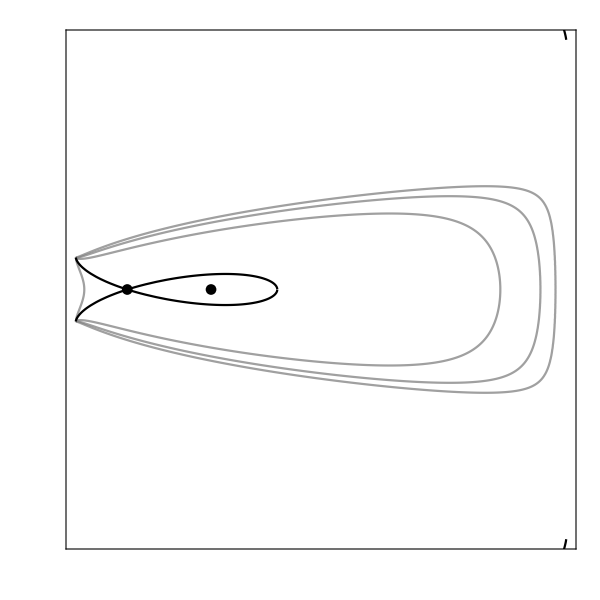

```mathematica
(*Show the trajectories*)
Show[trajConstantK3ProjectionPlots,EinsteinFixedPointsK3Projection,CFSK3Projection,PhaseSpaceFormatxY]
```

## Limiting Case 4: 1 Einstein Fixed Point

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=KValues[[4]]
```

0.0847952

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK4[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK4[x0_]=Sqrt[trajConstantK4[x0]/(1+trajConstantK4[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK4[1]=ParametricPlot3D[{x,trajConstantK4[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[2]=ParametricPlot3D[{x,-trajConstantK4[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[3]=ParametricPlot3D[{x,trajConstantK4[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[4]=ParametricPlot3D[{x,-trajConstantK4[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[5]=ParametricPlot3D[{x,trajConstantK4[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[6]=ParametricPlot3D[{x,-trajConstantK4[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[7]=ParametricPlot3D[{x,trajConstantK4[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK4[8]=ParametricPlot3D[{x,-trajConstantK4[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK4Plots=Table[trajConstantK4[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK4Surface=x/3+z/3-K/(aKz[z]^2);
YK4Surface=Sqrt[yK4Surface/(1+yK4Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK4Surface=ParametricPlot3D[{{x,YK4Surface,z},{x,-YK4Surface,z}},{x,ℛ,1},{z,0,.7},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK4=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsK4=ListPointPlot3D[{EinsteinFPConstantK[4]},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK4=ParametricPlot3D[{{x,CFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4],z[x,cConstantKCFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4]]},{x,-CFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4],z[x,cConstantKCFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4]]}},{x,ℛ,1},PlotStyle->Black];
```

```mathematica
(*Show all components of the phase space*)
xYZK4=Show[trajConstantK4Plots,ConstantK4Surface,CFSK4,AccnxYz,EinsteinPointsK4,EinsteinFixedPointsK4,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK4Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK4Proj[1]=ContourPlot[Evaluate[trajConstantK4Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK4Proj[2]=ContourPlot[Evaluate[trajConstantK4Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK4Proj[3]=ContourPlot[Evaluate[trajConstantK4Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK4Proj[4]=ContourPlot[Evaluate[trajConstantK4Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK4ProjectionPlots=Table[trajConstantK4Proj[i],{i,1,4}];
```

```mathematica
(*Plot the Einstein fixed point*)
EinsteinFixedPointsK4Projection=ListPlot[{{EinsteinFPConstantK[4][[1]],EinsteinFPConstantK[4][[2]]}},PlotStyle->Black];
```

```mathematica
(*Plot the CFS*)
CFSK4Projection=ParametricPlot[{{x,CFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4]},{x,-CFS[EinsteinFPConstantK[4][[1]],zOneEinsteinPointK4]}},{x,ℛ,1},PlotStyle->Black];
```

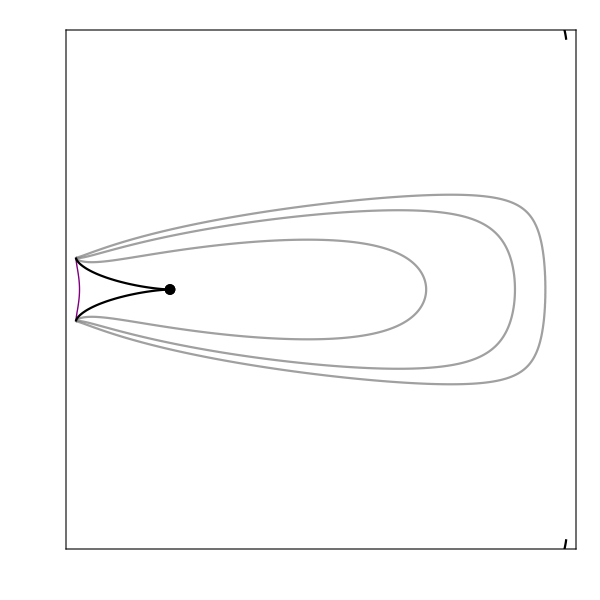

```mathematica
(*Show the trajectories*)
Show[trajConstantK4ProjectionPlots,EinsteinFixedPointsK4Projection,CFSK4Projection,PhaseSpaceFormatxY]
```

## Case 5: 0 Einstein Fixed Points

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
(*This is the dynamical case obtained when K = kClosed*)
K=KValues[[5]]
```

0.2

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK5[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK5[x0_]=Sqrt[trajConstantK5[x0]/(1+trajConstantK5[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK5[1]=ParametricPlot3D[{x,trajConstantK5[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[2]=ParametricPlot3D[{x,-trajConstantK5[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[3]=ParametricPlot3D[{x,trajConstantK5[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[4]=ParametricPlot3D[{x,-trajConstantK5[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[5]=ParametricPlot3D[{x,trajConstantK5[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[6]=ParametricPlot3D[{x,-trajConstantK5[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[7]=ParametricPlot3D[{x,trajConstantK5[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK5[8]=ParametricPlot3D[{x,-trajConstantK5[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK5Plots=Table[trajConstantK5[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK5Surface=x/3+z/3-K/(aKz[z]^2);
YK5Surface=Sqrt[yK5Surface/(1+yK5Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK5Surface=ParametricPlot3D[{{x,YK5Surface,z},{x,-YK5Surface,z}},{x,ℛ,1},{z,0,.6},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK5=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK5=Show[trajConstantK5Plots,ConstantK5Surface,AccnxYz,EinsteinPointsK5,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK5Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK5Proj[1]=ContourPlot[Evaluate[trajConstantK5Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK5Proj[2]=ContourPlot[Evaluate[trajConstantK5Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK5Proj[3]=ContourPlot[Evaluate[trajConstantK5Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK5Proj[4]=ContourPlot[Evaluate[trajConstantK5Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK5ProjectionPlots=Table[trajConstantK5Proj[i],{i,1,4}];
```

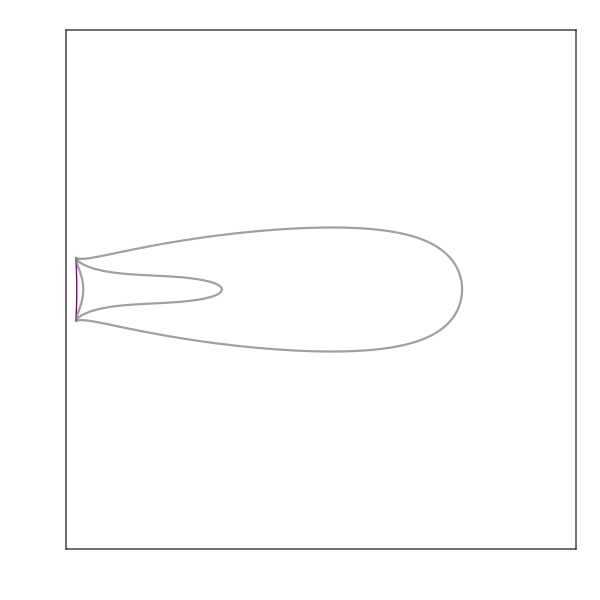

```mathematica
(*Show the trajectories*)
Show[trajConstantK5ProjectionPlots,PhaseSpaceFormatxY]
```

## Open Models

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=kOpen
```

-13.7336

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK6[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK6[x0_]=Sqrt[trajConstantK6[x0]/(1+trajConstantK6[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK6[1]=ParametricPlot3D[{x,trajConstantK6[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[2]=ParametricPlot3D[{x,-trajConstantK6[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[3]=ParametricPlot3D[{x,trajConstantK6[0.4],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[4]=ParametricPlot3D[{x,-trajConstantK6[0.4],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[5]=ParametricPlot3D[{x,trajConstantK6[0.7],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[6]=ParametricPlot3D[{x,-trajConstantK6[0.7],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[7]=ParametricPlot3D[{x,trajConstantK6[0.95],z[x,cConstantK[0.95]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK6[8]=ParametricPlot3D[{x,-trajConstantK6[0.95],z[x,cConstantK[0.95]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK6Plots=Table[trajConstantK6[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK6Surface=x/3+z/3-K/(aKz[z]^2);
YK6Surface=Sqrt[yK6Surface/(1+yK6Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK6Surface=ParametricPlot3D[{{x,YK6Surface,z},{x,-YK6Surface,z}},{x,ℛ,1},{z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK6=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK6=Show[trajConstantK6Plots,ConstantK6Surface,AccnxYz,EinsteinPointsK6,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK6Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK6Proj[1]=ContourPlot[Evaluate[trajConstantK6Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK6Proj[2]=ContourPlot[Evaluate[trajConstantK6Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK6Proj[3]=ContourPlot[Evaluate[trajConstantK6Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK6Proj[4]=ContourPlot[Evaluate[trajConstantK6Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK6ProjectionPlots=Table[trajConstantK6Proj[i],{i,1,4}];
```

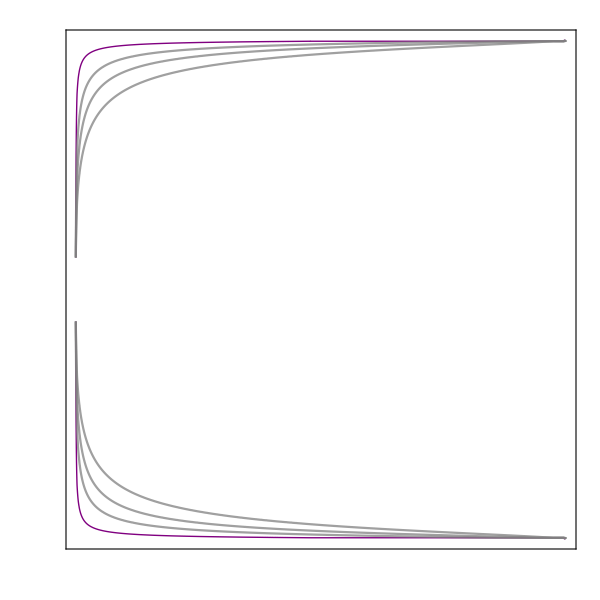

```mathematica
(*Show the trajectories*)
Show[trajConstantK6ProjectionPlots,PhaseSpaceFormatxY]
```

## Flat Models

### 3-D x - Y - Z Phase Space

```mathematica
(*Define K*)
K=0;
```

```mathematica
(*Define the Friedmann equation in terms of Y^2/(1-Y^2), which is used to plot the trajectories for the phase space*)
trajConstantK7[x0_]:=x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K)
```

```mathematica
(*Rearrange the above equation for Y*)
(*Note that when plotting the trajectories, +trajConstantK and -trajConstantK needs to be plotted as a Sqrt is taken and Mathematica outputs the + solution only*)
trajConstantK7[x0_]=Sqrt[trajConstantK7[x0]/(1+trajConstantK7[x0])];
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK7[1]=ParametricPlot3D[{x,trajConstantK7[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[2]=ParametricPlot3D[{x,-trajConstantK7[0.1],z[x,cConstantK[0.1]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Thick,Purple}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[3]=ParametricPlot3D[{x,trajConstantK7[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[4]=ParametricPlot3D[{x,-trajConstantK7[0.3],z[x,cConstantK[0.3]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[5]=ParametricPlot3D[{x,trajConstantK7[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[6]=ParametricPlot3D[{x,-trajConstantK7[0.5],z[x,cConstantK[0.5]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->500,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[7]=ParametricPlot3D[{x,trajConstantK7[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->1000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0},1]]],Arrow[x]};
```

```mathematica
trajConstantK7[8]=ParametricPlot3D[{x,-trajConstantK7[0.7],z[x,cConstantK[0.7]]},{x,ℛ,1},AxesLabel->{"x","Y","z"},PlotStyle -> {{Gray}},PlotPoints->10000,PlotRange->{{ℛ,1},{-1,1},{0,1}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK7Plots=Table[trajConstantK7[i],{i,1,8}];
```

```mathematica
(*Define the first integral surface with constant curvature*)
yK7Surface=x/3+z/3-K/(aKz[z]^2);
YK7Surface=Sqrt[yK7Surface/(1+yK7Surface)];
```

```mathematica
(*Plot the constant curvature first integral surface*)
ConstantK7Surface=ParametricPlot3D[{{x,YK7Surface,z},{x,-YK7Surface,z}},{x,ℛ,1},{z,0,1},
PlotStyle -> {{Yellow, Opacity[0.25]}},Mesh->None,PlotPoints->100,PlotRange->{{ℛ,1},{-1,1},{0,1}}];
```

```mathematica
(*Plot the line of possible Einstein fixed points*)
EinsteinPointsK7=ParametricPlot3D[{3*K/(aKz[z]^2)-z,0,z},{z,0,1},AxesLabel->{"x","Y","Z"}];
```

```mathematica
(*Show all components of the phase space*)
xYZK7=Show[trajConstantK7Plots,ConstantK7Surface,AccnxYz,EinsteinPointsK7,FPShowConstantKXYZ,FPShowConstantKCompactXYZ,PhaseSpaceFormatxYz]
```

-Graphics3D-

### 2-D x-Y Projection

```mathematica
(*Define the Friedmann equation for this case, which is used to plot the trajectories for the phase space*)
trajConstantK7Projection[x0_]:=Y^2/(1-Y^2)==x/3+z[x,cConstantK[x0]]/3-(1/a[x,x0]^2)*(K);
```

```mathematica
(*Plot trajectories with different initial conditions*)
```

```mathematica
trajConstantK7Proj[1]=ContourPlot[Evaluate[trajConstantK7Projection[0.1]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Thick,Purple}}];
```

```mathematica
trajConstantK7Proj[2]=ContourPlot[Evaluate[trajConstantK7Projection[0.3]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK7Proj[3]=ContourPlot[Evaluate[trajConstantK7Projection[0.5]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
trajConstantK7Proj[4]=ContourPlot[Evaluate[trajConstantK7Projection[0.7]],{x,ℛ,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Gray, Opacity[0.75]}}];
```

```mathematica
(*Put the trajectories into a table*)
trajConstantK7ProjectionPlots=Table[trajConstantK7Proj[i],{i,1,4}];
```

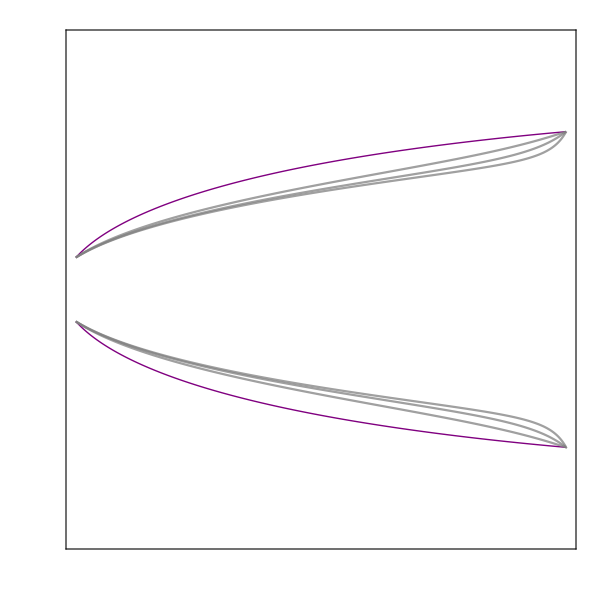

```mathematica
(*Show the trajectories*)
Show[trajConstantK7ProjectionPlots,PhaseSpaceFormatxY]
```